#### PREPARATION

Specify here the path of the directory where you stored the data files

```mathematica
SetDirectory[NotebookDirectory[]];
WorkDirNum=StringJoin[NotebookDirectory[],"Functions-TMD/"];(*"C:\\Documents and Settings\\barbara\\My Documents\\mathematica\\Varenna\\Functions-TMD";*)
```

```mathematica
unitconv=1./0.19732^2;
Mn:=0.93827231
```

## WF WITH SU(6)-BREAKING

### functions A and B: reading from files Results with SU(6) symmetry from: B. Pasquini, S. Cazzaniga, S. Boffi, Phys. Rev. D78, 034025 (2008)

```mathematica
unitconv=1./0.19732^2;
```

Function A: SU(6)-symmetric, SU(6)-breaking terms and interference terms

```mathematica
list0=ReadList[StringJoin[WorkDirNum,"tmd_f1_up_schlumpf.dat"],{Number,Number,Number}];listf1up=Table[{list0[[n,1]],list0[[n,2]],list0[[n,3]]*unitconv},{n,Length[list0]}];
Au:=Interpolation[listf1up]
Ad[x_,y_]=Au[x,y]/2.;
list0b=ReadList[StringJoin[WorkDirNum,"function_A_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listf1upb=Table[{list0b[[n,1]],list0b[[n,2]],list0b[[n,3]]*unitconv},{n,Length[list0b]}];
Abreaku=Interpolation[listf1upb];
Abreakd[x_,y_]=Abreaku[x,y]/2.;
list0i=ReadList[StringJoin[WorkDirNum,"function_A_int_su6_symm_break_up_schlumpf_new_sign.dat"],{Number,Number,Number}];listf1upi=Table[{list0i[[n,1]],list0i[[n,2]],list0i[[n,3]]*unitconv},{n,Length[list0i]}];
Aintu=Interpolation[listf1upi];
Aintd[x_,y_]=-Aintu[x,y];
```

```mathematica
list0i=ReadList["function_A_int_su6_symm_break_up_schlumpf_new_sign.dat",{Number,Number,Number}];
```

ReadList::noopen: Cannot open function_A_int_su6_symm_break_up_schlumpf_new_sign.dat.

Functions B: contribution from SU(6) symmetric term

```mathematica
Bu[x_,y_]:=2./3.*Au[x,y]
Bd[x_,y_]:=-1./4.*Bu[x,y]
listBtu=ReadList[StringJoin[WorkDirNum,"function_Btilde_su6_symm_up_schlumpf.dat"],{Number,Number,Number}];listBtildeu=Table[{listBtu[[n,1]],listBtu[[n,2]],listBtu[[n,3]]*unitconv^2},{n,Length[listBtu]}];
Btildeu=Interpolation[listBtildeu];
Btilded[x_,y_]=-1./4.*Btildeu[x,y];
listBhu=ReadList[StringJoin[WorkDirNum,"function_Bbar_su6_symm_up_schlumpf.dat"],{Number,Number,Number}];listBhatup=Table[{listBhu[[n,1]],listBhu[[n,2]],listBhu[[n,3]]*unitconv^(3./2.)},{n,Length[listBhu]}];
Bhatu=Interpolation[listBhatup];
Bhatd[x_,y_]:=-1./4.*Bhatu[x,y]
```

Functions B: contribution from SU(6) breaking terms

```mathematica
listBbreaku=ReadList[StringJoin[WorkDirNum,"function_B_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listBbreaku=Table[{listBbreaku[[n,1]],listBbreaku[[n,2]],listBbreaku[[n,3]]*unitconv},{n,Length[listBbreaku]}];
Bbreaku=Interpolation[listBbreaku];

listBtbreaku=ReadList[StringJoin[WorkDirNum,"function_Btilde_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listBtildebreaku=Table[{listBtbreaku[[n,1]],listBtbreaku[[n,2]],listBtbreaku[[n,3]]*unitconv^2},{n,Length[listBtbreaku]}];
Btildebreaku=Interpolation[listBtildebreaku];

listBhbreaku=ReadList[StringJoin[WorkDirNum,"function_Bbar_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listBhatbreaku=Table[{listBhbreaku[[n,1]],listBhbreaku[[n,2]],listBhbreaku[[n,3]]*unitconv^(3/2)},{n,Length[listBhbreaku]}];
Bhatbreaku=Interpolation[listBhatbreaku];


listBbreakd=ReadList[StringJoin[WorkDirNum,"function_B_su6_break_down_schlumpf.dat"],{Number,Number,Number}];listBbreakd=Table[{listBbreakd[[n,1]],listBbreakd[[n,2]],listBbreakd[[n,3]]*unitconv},{n,Length[listBbreakd]}];
Bbreakd=Interpolation[listBbreakd];

listBtbreakd=ReadList[StringJoin[WorkDirNum,"function_Btilde_su6_break_down_schlumpf.dat"],{Number,Number,Number}];listBtildebreakd=Table[{listBtbreakd[[n,1]],listBtbreakd[[n,2]],listBtbreakd[[n,3]]*unitconv^2},{n,Length[listBtbreakd]}];
Btildebreakd=Interpolation[listBtildebreakd];

listBhbreakd=ReadList[StringJoin[WorkDirNum,"function_Bbar_su6_break_down_schlumpf.dat"],{Number,Number,Number}];listBhatbreakd=Table[{listBhbreakd[[n,1]],listBhbreakd[[n,2]],listBhbreakd[[n,3]]*unitconv^(3./2.)},{n,Length[listBhbreakd]}];
Bhatbreakd=Interpolation[listBhatbreakd];
```

Functions B: contribution from interference between  SU(6)-breaking and SU(6) symmetric terms

```mathematica
Bintu[x_,y_]:=5./3.*Aintu[x,y]
Bintd[x_,y_]:=1./5.*Bintu[x,y]

listBtintu=ReadList[StringJoin[WorkDirNum,"function_Btilde_int_su6_symm_break_up_schlumpf_new_sign.dat"],{Number,Number,Number}];listBtildeintu=Table[{listBtintu[[n,1]],listBtintu[[n,2]],listBtintu[[n,3]]*unitconv^2},{n,Length[listBtintu]}];
Btildeintu=Interpolation[listBtildeintu];
Btildeintd[x_,y_]=1./5.*Btildeintu[x,y];

listBhintu=ReadList[StringJoin[WorkDirNum,"function_Bbar_int_su6_symm_break_up_schlumpf_new_sign.dat"],{Number,Number,Number}];listBhatintu=Table[{listBhintu[[n,1]],listBhintu[[n,2]],listBhintu[[n,3]]*unitconv^(3./2.)},{n,Length[listBhintu]}];
Bhatintu=Interpolation[listBhatintu];
Bhatintd[x_,y_]=1./5.*Bhatintu[x,y];
```

### TMD f_1

```mathematica
f1u[x_,y_]:=Cos[delta]^2*Au[x,y]+Sin[delta]*Cos[delta]*Aintu[x,y]+Sin[delta]^2*Abreaku[x,y]
```

```mathematica
f1d[x_,y_]:=Cos[delta]^2*Ad[x,y]+Sin[delta]*Cos[delta]*Aintd[x,y]+Sin[delta]^2*Abreakd[x,y]
```

```mathematica
plotf1u=Manipulate[Plot3D[f1u[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","f_1^u"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
plotf1d=Manipulate[Plot3D[f1d[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","f_1^d"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{plotf1u,plotf1d},TableDirections->Row]
```

|

### TMD g_(1L)

```mathematica
g1Lu[x_,y_]:=Cos[delta]^2*Bu[x,y]+Sin[delta]*Cos[delta]*Bintu[x,y]+Sin[delta]^2*Bbreaku[x,y]-2.*y(Cos[delta]^2*Btildeu[x,y]+Sin[delta]*Cos[delta]*Btildeintu[x,y]+Sin[delta]^2*Btildebreaku[x,y])
```

```mathematica
g1Ld[x_,y_]:=Cos[delta]^2*Bd[x,y]+Sin[delta]*Cos[delta]*Bintd[x,y]+Sin[delta]^2*Bbreakd[x,y]-2.*y(Cos[delta]^2*Btilded[x,y]+Sin[delta]*Cos[delta]*Btildeintd[x,y]+Sin[delta]^2*Btildebreakd[x,y])
```

```mathematica
plotg1Lu=Manipulate[Plot3D[g1Lu[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","g_(1  L)^u"}],{δ,0,180.,Appearance->"Labeled"}];
```

```mathematica
plotg1Ld=Manipulate[Plot3D[g1Ld[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","g_(1  L)^d"}],{δ,0,180.,Appearance->"Labeled"}];
```

```mathematica
TableForm[{plotg1Lu,plotg1Ld},TableDirections->Row]
```

|

### TMD h_1

```mathematica
h1u[x_,y_]:=Cos[delta]^2*Bu[x,y]+Sin[delta]*Cos[delta]*Bintu[x,y]+Sin[delta]^2*Bbreaku[x,y]-y*(Cos[delta]^2*Btildeu[x,y]+Sin[delta]*Cos[delta]*Btildeintu[x,y]+Sin[delta]^2*Btildebreaku[x,y])
```

```mathematica
h1d[x_,y_]:=Cos[delta]^2*Bd[x,y]+Sin[delta]*Cos[delta]*Bintd[x,y]+Sin[delta]^2*Bbreakd[x,y]-y(Cos[delta]^2*Btilded[x,y]+Sin[delta]*Cos[delta]*Btildeintd[x,y]+Sin[delta]^2*Btildebreakd[x,y])
```

```mathematica
ploth1u=Manipulate[Plot3D[h1u[x,ksq]/.{delta->δ/180*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","h_1^u"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
ploth1d=Manipulate[Plot3D[h1d[x,ksq]/.{delta->δ/180*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","h_1^d"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{ploth1u,ploth1d},TableDirections->Row]
```

|

### TMD h_(1L) - -g_(1T)

```mathematica
h1Lu[x_,y_]=-2.*Mn*(Cos[delta]^2*Bhatu[x,y]+Sin[delta]*Cos[delta]*Bhatintu[x,y]+Sin[delta]^2*Bhatbreaku[x,y]);
h1Ld[x_,y_]=-2.*Mn*(Cos[delta]^2*Bhatd[x,y]+Sin[delta]*Cos[delta]*Bhatintd[x,y]+Sin[delta]^2*Bhatbreakd[x,y]);
```

```mathematica
ploth1Lu=Manipulate[Plot3D[h1Lu[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","h_(1  L)^(⊥u)"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
ploth1Ld=Manipulate[Plot3D[h1Ld[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","h_(1  L)^(⊥d)"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{ploth1Lu,ploth1Ld},TableDirections->Row]
```

|

### TMD h_(1T)^⊥

```mathematica
h1tperpu[x_,y_]:=-2.*Mn^2*(Cos[delta]^2*Btildeu[x,y]+Sin[delta]*Cos[delta]*Btildeintu[x,y]+Sin[delta]^2*Btildebreaku[x,y])
h1tperpd[x_,y_]:=-2.*Mn^2*(Cos[delta]^2*Btilded[x,y]+Sin[delta]*Cos[delta]*Btildeintd[x,y]+Sin[delta]^2*Btildebreakd[x,y])
```

```mathematica
ploth1tperpu=Manipulate[Plot3D[h1tperpu[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","h_(1  T)^(⊥u)"}],{δ,0,Pi,Appearance->"Labeled"}];
```

```mathematica
ploth1tperpd=Manipulate[Plot3D[h1tperpd[x,ksq]/.{delta->δ/180.*Pi},{x,0,1},{ksq,0.,0.15},PlotRange->All,AxesLabel->{"x","k_⊥^2","h_(1  T)^(⊥d)"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{ploth1tperpu,ploth1tperpd},TableDirections->Row]
```

|

## DENSITY PLOTS

### functions A and B: reading from files

```mathematica
unitconv=1./0.19732^2;
```

Function A: SU(6)-symmetric and SU(6)-breaking terms

```mathematica
list0=ReadList[StringJoin[WorkDirNum,"\\x_function_A_su6_symm_up_schlumpf.dat"],{Number,Number,Number}];listf1up=Table[{list0[[n,1]],list0[[n,2]],list0[[n,3]]*unitconv},{n,Length[list0]}];
xAu:=Interpolation[listf1up]
xAd[x_,y_]=xAu[x,y]/2.;
list0b=ReadList[StringJoin[WorkDirNum,"\\x_function_A_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listf1upb=Table[{list0b[[n,1]],list0b[[n,2]],list0b[[n,3]]*unitconv},{n,Length[list0b]}];
xAbreaku=Interpolation[listf1upb];
xAbreakd[x_,y_]=xAbreaku[x,y]/2.;
list0i=ReadList[StringJoin[WorkDirNum,"\\x_function_A_int_su6_symm_break_up_schlumpf.dat"],{Number,Number,Number}];listf1upi=Table[{list0i[[n,1]],list0i[[n,2]],list0i[[n,3]]*unitconv},{n,Length[list0i]}];
xAintu=Interpolation[listf1upi];
xAintd[x_,y_]=-xAintu[x,y];
```

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_A_su6_symm_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_A_su6_break_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_A_int_su6_symm_break_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Functions B: contribution from SU(6) symmetric term

```mathematica
xBu[x_,y_]:=2./3.*xAu[x,y]
xBd[x_,y_]:=-1./4.*xBu[x,y]
listBtu=ReadList[StringJoin[WorkDirNum,"\\x_function_Btilde_su6_symm_up_schlumpf.dat"],{Number,Number,Number}];listBtildeu=Table[{listBtu[[n,1]],listBtu[[n,2]],listBtu[[n,3]]*unitconv^2},{n,Length[listBtu]}];
xBtildeu=Interpolation[listBtildeu];
xBtilded[x_,y_]=-1./4.*xBtildeu[x,y];
listBhu=ReadList[StringJoin[WorkDirNum,"\\x_function_Bbar_su6_symm_up_schlumpf.dat"],{Number,Number,Number}];listBhatup=Table[{listBhu[[n,1]],listBhu[[n,2]],listBhu[[n,3]]*unitconv^(3./2.)},{n,Length[listBhu]}];
xBhatu=Interpolation[listBhatup];
xBhatd[x_,y_]:=-1./4.*xBhatu[x,y]
```

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Btilde_su6_symm_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Bbar_su6_symm_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Functions B: contribution from SU(6) breaking terms

```mathematica
listBbreaku=ReadList[StringJoin[WorkDirNum,"\\x_function_B_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listBbreaku=Table[{listBbreaku[[n,1]],listBbreaku[[n,2]],listBbreaku[[n,3]]*unitconv},{n,Length[listBbreaku]}];
xBbreaku=Interpolation[listBbreaku];

listBtbreaku=ReadList[StringJoin[WorkDirNum,"\\x_function_Btilde_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listBtildebreaku=Table[{listBtbreaku[[n,1]],listBtbreaku[[n,2]],listBtbreaku[[n,3]]*unitconv^2},{n,Length[listBtbreaku]}];
xBtildebreaku=Interpolation[listBtildebreaku];

listBhbreaku=ReadList[StringJoin[WorkDirNum,"\\x_function_Bbar_su6_break_up_schlumpf.dat"],{Number,Number,Number}];listBhatbreaku=Table[{listBhbreaku[[n,1]],listBhbreaku[[n,2]],listBhbreaku[[n,3]]*unitconv^(3/2)},{n,Length[listBhbreaku]}];
xBhatbreaku=Interpolation[listBhatbreaku];


listBbreakd=ReadList[StringJoin[WorkDirNum,"\\x_function_B_su6_break_down_schlumpf.dat"],{Number,Number,Number}];listBbreakd=Table[{listBbreakd[[n,1]],listBbreakd[[n,2]],listBbreakd[[n,3]]*unitconv},{n,Length[listBbreakd]}];
xBbreakd=Interpolation[listBbreakd];

listBtbreakd=ReadList[StringJoin[WorkDirNum,"\\x_function_Btilde_su6_break_down_schlumpf.dat"],{Number,Number,Number}];listBtildebreakd=Table[{listBtbreakd[[n,1]],listBtbreakd[[n,2]],listBtbreakd[[n,3]]*unitconv^2},{n,Length[listBtbreakd]}];
xBtildebreakd=Interpolation[listBtildebreakd];

listBhbreakd=ReadList[StringJoin[WorkDirNum,"\\x_function_Bbar_su6_break_down_schlumpf.dat"],{Number,Number,Number}];listBhatbreakd=Table[{listBhbreakd[[n,1]],listBhbreakd[[n,2]],listBhbreakd[[n,3]]*unitconv^(3./2.)},{n,Length[listBhbreakd]}];
xBhatbreakd=Interpolation[listBhatbreakd];
```

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_B_su6_break_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Btilde_su6_break_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Bbar_su6_break_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_B_su6_break_down_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Btilde_su6_break_down_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Bbar_su6_break_down_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Functions B: contribution from interference between  SU(6)-breaking and SU(6) symmetric terms

```mathematica
xBintu[x_,y_]:=5./3.*xAintu[x,y]
xBintd[x_,y_]:=1./5.*xBintu[x,y]

listBtintu=ReadList[StringJoin[WorkDirNum,"\\x_function_Btilde_int_su6_symm_break_up_schlumpf.dat"],{Number,Number,Number}];listBtildeintu=Table[{listBtintu[[n,1]],listBtintu[[n,2]],listBtintu[[n,3]]*unitconv^2},{n,Length[listBtintu]}];
xBtildeintu=Interpolation[listBtildeintu];
xBtildeintd[x_,y_]=1./5.*xBtildeintu[x,y];

listBhintu=ReadList[StringJoin[WorkDirNum,"\\x_function_Bbar_int_su6_symm_break_up_schlumpf.dat"],{Number,Number,Number}];listBhatintu=Table[{listBhintu[[n,1]],listBhintu[[n,2]],listBhintu[[n,3]]*unitconv^(3./2.)},{n,Length[listBhintu]}];
xBhatintu=Interpolation[listBhatintu];
xBhatintd[x_,y_]=1./5.*xBhatintu[x,y];
```

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Btilde_int_su6_symm_break_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

ReadList::noopen: Cannot open /Users/avp5627/GIT/DY/barbara/\x_function_Bbar_int_su6_symm_break_up_schlumpf.dat.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

## Net polarizations

### TMD f_1

```mathematica
f1u[kx_,ky_,delta_]:=Cos[delta]^2*xAu[kx,ky]+Sin[delta]*Cos[delta]*xAintu[kx,ky]+Sin[delta]^2*xAbreaku[kx,ky]
```

```mathematica
f1d[kx_,ky_,delta_]:=Cos[delta]^2*xAd[kx,ky]+Sin[delta]*Cos[delta]*xAintd[kx,ky]+Sin[delta]^2*xAbreakd[kx,ky]
```

```mathematica
plotf1u=Manipulate[ContourPlot[f1u[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","f_1^u"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
plotf1d=Manipulate[ContourPlot[f1d[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","f_1^d"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{plotf1u,plotf1d},TableDirections->Row]
```

|

### TMD g_(1L)

```mathematica
g1Lu[kx_,ky_,delta_]:=Cos[delta]^2*xBu[kx,ky]+Sin[delta]*Cos[delta]*xBintu[kx,ky]+Sin[delta]^2*xBbreaku[kx,ky]-2.*(kx^2+ky^2)*(Cos[delta]^2*xBtildeu[kx,ky]+Sin[delta]*Cos[delta]*xBtildeintu[kx,ky]+Sin[delta]^2*xBtildebreaku[kx,ky])
```

```mathematica
g1Ld[kx_,ky_,delta_]:=Cos[delta]^2*xBd[kx,ky]+Sin[delta]*Cos[delta]*xBintd[kx,ky]+Sin[delta]^2*xBbreakd[kx,ky]-2.*(kx^2+ky^2)*(Cos[delta]^2*xBtilded[kx,ky]+Sin[delta]*Cos[delta]*xBtildeintd[kx,ky]+Sin[delta]^2*xBtildebreakd[kx,ky])
```

```mathematica
plotg1Lu=Manipulate[ContourPlot[g1Lu[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","g_(1  L)^u"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
plotg1Ld=Manipulate[ContourPlot[g1Ld[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","g_(1  L)^d"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{plotg1Lu,plotg1Ld},TableDirections->Row]
```

|

### TMD h_1

```mathematica
h1u[kx_,ky_,delta_]:=Cos[delta]^2*xBu[kx,ky]+Sin[delta]*Cos[delta]*xBintu[kx,ky]+Sin[delta]^2*xBbreaku[kx,ky]-(kx^2+ky^2)*(Cos[delta]^2*xBtildeu[kx,ky]+Sin[delta]*Cos[delta]*xBtildeintu[kx,ky]+Sin[delta]^2*xBtildebreaku[kx,ky])
```

```mathematica
h1d[kx_,ky_,delta_]:=Cos[delta]^2*xBd[kx,ky]+Sin[delta]*Cos[delta]*xBintd[kx,ky]+Sin[delta]^2*xBbreakd[kx,ky]-(kx^2+ky^2)*(Cos[delta]^2*xBtilded[kx,ky]+Sin[delta]*Cos[delta]*xBtildeintd[kx,ky]+Sin[delta]^2*xBtildebreakd[kx,ky])
```

```mathematica
ploth1u=Manipulate[ContourPlot[h1u[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","h_1^u"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
ploth1d=Manipulate[ContourPlot[h1d[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","h_1^d"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{ploth1u,ploth1d},TableDirections->Row]
```

|

### TMD h_(1L) - -g_(1T)

```mathematica
h1Lu[kx_,ky_,delta_]=-2.*Mn*(Cos[delta]^2*xBhatu[kx,ky]+Sin[delta]*Cos[delta]*xBhatintu[kx,ky]+Sin[delta]^2*xBhatbreaku[kx,ky]);
h1Ld[kx_,ky_,delta_]=-2.*Mn*(Cos[delta]^2*xBhatd[kx,ky]+Sin[delta]*Cos[delta]*xBhatintd[kx,ky]+Sin[delta]^2*xBhatbreakd[kx,ky]);
```

```mathematica
g1Tu[kx_,ky_,delta_]:=-h1Lu[kx,ky,delta]
g1Td[kx_,ky_,delta_]:=-h1Ld[kx,ky,delta]
```

```mathematica
h1Lu[0.2,0.2,0]
```

-1.87654 Interpolation[{}][0.2,0.2]

```mathematica
ploth1Lu=Manipulate[ContourPlot[kx/Mn*h1Lu[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","h_(1  L)^u"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
ploth1Ld=Manipulate[ContourPlot[kx/Mn*h1Ld[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","h_(1  L)^d"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{ploth1Lu,ploth1Ld},TableDirections->Row]
```

|

### TMD h_(1T)^⊥

```mathematica
h1tperpu[kx_,ky_,delta_]:=-2.*Mn^2*(Cos[delta]^2*xBtildeu[kx,ky]+Sin[delta]*Cos[delta]*xBtildeintu[kx,ky]+Sin[delta]^2*xBtildebreaku[kx,ky])
h1tperpd[x_,y_,delta_]:=-2.*Mn^2*(Cos[delta]^2*xBtilded[kx,ky]+Sin[delta]*Cos[delta]*xBtildeintd[kx,ky]+Sin[delta]^2*xBtildebreakd[kx,ky])
```

```mathematica
ploth1tperpu=Manipulate[ContourPlot[kx*ky/2/Mn^2*h1tperpu[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","h_(1  T)^(⊥u)"}],{δ,0,180,Appearance->"Labeled"}]
```

```mathematica
ploth1tperpd=Manipulate[ContourPlot[kx*ky/2/Mn^2*h1tperpd[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","h_(1  T)^(⊥d)"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{ploth1tperpu,ploth1tperpd},TableDirections->Row]
```

|

## Long. polarized proton and Transv. pol. quark in x-direction

```mathematica
ρLTu[kx_,ky_,delta_]:=1./2.*(f1u[kx,ky,delta]+kx/Mn*h1Lu[kx,ky,delta])
```

```mathematica
ρLTd[kx_,ky_,delta_]:=1./2.*(f1d[kx,ky,delta]+kx/Mn*h1Ld[kx,ky,delta])
```

```mathematica
plotLTu:=Manipulate[ContourPlot[ρLTu[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All],{δ,0,180,Appearance->"Labeled"}]
```

```mathematica
plotLTd=Manipulate[ContourPlot[ρLTd[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{plotLTu,plotLTd},TableDirections->Row]
```

|

## Transversely polarized proton in x-direction and Long. pol. quark

```mathematica
ρTLu[kx_,ky_,delta_]:=1./2.*(f1u[kx,ky,delta]+kx/Mn*g1Tu[kx,ky,delta])
```

```mathematica
ρTLd[kx_,ky_,delta_]:=1./2.*(f1d[kx,ky,delta]+kx/Mn*g1Td[kx,ky,delta])
```

```mathematica
plotTLu=Manipulate[ContourPlot[ρTLu[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","ρ_TL^u"}],{δ,0,180,Appearance->"Labeled"}]
```

```mathematica
plotTLd=Manipulate[ContourPlot[ρTLd[kx,ky,δ/180.*Pi],{kx,-0.5,0.5},{ky,-0.5,0.5},PlotRange->All,AxesLabel->{"k_x","k_y","ρ_TL^d"}],{δ,0,180,Appearance->"Labeled"}];
```

```mathematica
TableForm[{plotTLu,plotTLd},TableDirections->Row]
```

|

## Long. polarized proton and Long. pol. quark

## Transversely polarized proton in x-direction and Transv. pol. quark in x-direction

## Transversely polarized proton in y-direction and Transv. pol. quark in x-direction

## TRANSVERSE MOMENTUM DEPENDENCE

## x-moments of TMDs

### Functions to build up x-moments of TMDs

### Function A

```mathematica
xmAu:=Interpolation[{{0.,11.14590458333238},{0.01,8.890623532214413},{0.02,7.187010867788978},{0.03,5.876204711799324},{0.04,4.852147958297058},{0.05,4.041998983216424},{0.06,3.3936377376112365},{0.07,2.869524624959339},{0.08,2.4419167721610173},{0.09,2.0902957580115813},{0.1,1.798965533219986},{0.11,1.5559916263966205},{0.12,1.3520551799977478},{0.13,1.1799566612150285},{0.14,1.0338725903916244},{0.15,0.9093064183320214},{0.16,0.8026153453368489},{0.17,0.7107783943678049},{0.18,0.6314176289962309},{0.19,0.5626010385300226},{0.2,0.5026927240537453},{0.21,0.45038812919944154},{0.22,0.40454004852455383},{0.23,0.3642439488220646},{0.24,0.32871541336180693},{0.25,0.29729140697641065},{0.26,0.26945860391171805},{0.27,0.244714545673671},{0.28,0.22267058363613854},{0.29,0.2029870326160227},{0.3,0.1853714111612952},{0.31,0.16956961986851188},{0.32,0.15537829685538704},{0.33,0.14259658390168922},{0.34,0.1310596416521637},{0.35,0.12063457242914026},{0.36,0.11119797835074494},{0.37,0.10264190254117712},{0.38,0.09486598344963931},{0.39,0.08778933581558328},{0.4,0.08134358825685774},{0.41,0.07545701087496175},{0.42,0.07008054536749249},{0.43,0.06515919720154145},{0.44,0.06064685921762142},{0.45,0.05651060391227406},{0.46,0.052707596461715876},{0.47,0.049208839562046754},{0.48,0.04598652166503233},{0.49,0.043016314226288356},{0.5,0.04027303624610095},{0.51,0.037738731522975175},{0.52,0.03539601133237108},{0.53,0.0332244151574368},{0.54,0.03121168994751522},{0.55,0.02934385760605708},{0.56,0.027610097810052928},{0.57,0.025998548954499066},{0.58,0.024497844547638946},{0.59,0.023101603694522594},{0.6,0.021799262758852758},{0.61,0.02058482287816167},{0.62,0.019450663605913725},{0.63,0.018391407643790846},{0.64,0.017399860335191576},{0.65,0.01647333527849033},{0.66,0.015604656771675584},{0.67,0.014790709377702844},{0.68,0.014027505374884943},{0.69,0.0133111080776436},{0.7,0.012639025545943858},{0.71,0.012006704451489242},{0.72,0.011412384763275302},{0.73,0.010852810939041935},{0.74,0.0103263753991311},{0.75,0.009830299864329251},{0.76,0.009362241238257957},{0.77,0.008920876383331786},{0.78,0.008504280495678387},{0.79,0.008111371560983974},{0.8,0.0077395887378738605},{0.81,0.007388406615904399},{0.82,0.007056046158454627},{0.83,0.0067417216358673345},{0.84,0.00644388963697373},{0.85,0.006161924303601275},{0.86,0.0058943131524193644},{0.87,0.005640952976124479},{0.88,0.005400350004115115},{0.89,0.0051720419423619485},{0.9,0.004955495076323531},{0.91,0.004749581583265557},{0.92,0.004553713475336453},{0.93,0.004367753011825715},{0.94,0.004190555163679015},{0.95,0.004022327071149048},{0.96,0.0038618856862010663},{0.97,0.003709161967654504},{0.98,0.0035635378416754935},{0.99,0.003424943292740835},{1.,0.0032927033545565245},{1.01,0.0031664141287733975},{1.02,0.0030460575793387957},{1.03,0.0029312539444493343},{1.04,0.0028214172557508503},{1.05,0.0027165791400808608},{1.06,0.002616239928506477},{1.07,0.0025204433265697064},{1.08,0.0024288987642077315},{1.09,0.0023412545168809444},{1.1,0.002257362941781162},{1.11,0.002177204455538374},{1.12,0.0021002963327878474},{1.13,0.002026662283146794},{1.14,0.0019560729884089793},{1.15,0.0018884811328651317},{1.16,0.0018237066225888136},{1.17,0.001761493773268332},{1.18,0.0017019018615603064},{1.19,0.0016446634845390094},{1.2,0.0015897581828036907},{1.21,0.0015370098273048904},{1.22,0.0014863857597482984},{1.23,0.0014376723117724944},{1.24,0.0013909883705912744},{1.25,0.0013460067710010925},{1.26,0.0013028010582595874},{1.27,0.0012612566379033897},{1.28,0.0012212782645640923},{1.29,0.001182885666223309},{1.3,0.0011458642547392448},{1.31,0.001110257692750391},{1.32,0.0010759377688516376},{1.33,0.0010429386504745783},{1.34,0.0010111359372341428},{1.35,0.0009804480939313656},{1.36,0.0009508777895463482},{1.37,0.0009223809561339706},{1.38,0.0008949507578021736},{1.39,0.0008684397155156584},{1.40,0.0008429002401423946},{1.41,0.000818235868481618},{1.42,0.0007944614523239557},{1.43,0.0007714855538528856},{1.44,0.0007493225863940398},{1.45,0.0007278761746863988},{1.46,0.0007072085432885275},{1.47,0.0006872182489114276},{1.48,0.0006679079125219628},{1.49,0.0006492769796082625},{1.5,0.0006312455255457687},{1.51,0.0006137916316151429},{1.52,0.0005969475249853017},{1.53,0.0005806097012482583},{1.54,0.0005648706023645197},{1.55,0.0005495995488770445},{1.56,0.0005348319721489442},{1.57,0.0005205265745120265},{1.58,0.0005067064256438634},{1.59,0.0004933148592600089},{1.6,0.00048032275398389706},{1.61,0.0004677611869938448},{1.62,0.00045561083618707895},{1.63,0.000443805230662774},{1.64,0.0004323780641639234},{1.65,0.00042127792206954817},{1.66,0.00041053961063942116},{1.67,0.00040013736091401195},{1.68,0.00039003993569060395},{1.69,0.00038025800288458007},{1.7,0.0003707573998461184},{1.71,0.00036153329917435037},{1.72,0.0003525993744165264},{1.73,0.00034391648072601167},{1.74,0.0003354842974700246},{1.75,0.00032732620554487503},{1.76,0.0003193822060144635},{1.77,0.0003116844931178174},{1.78,0.0003042142803030873},{1.79,0.0002969447938913901},{1.8,0.0002898848741213191},{1.81,0.0002830244701331598},{1.82,0.0002763499433329463},{1.83,0.0002698702630908208},{1.84,0.00026357423055690964},{1.85,0.00025745350218339235},{1.86,0.0002515003719597534},{1.87,0.00024571262648041245},{1.88,0.00024008191055597844},{1.89,0.00023462169599339046},{1.90,0.00022928008789792535},{1.91,0.0002241088352059128},{1.92,0.0002190730132010377},{1.93,0.00021416720250043295},{1.94,0.00020938931963166669},{1.95,0.00020475004499968244},{1.96,0.00020022286854856478},{1.97,0.00019582101175194682},{1.98,0.0001915336838788961},{1.99,0.00018735839215391326},{2.,0.00018329374997884325}}]
```

```mathematica
xmAbreaku := Interpolation[{{0., 14.516797518026518}, {0.01, 9.376623578532204}, {0.02, 6.975879546154602}, 
  {0.03, 5.494998371661246}, {0.04, 4.469764358384754}, {0.05, 3.71096760273022}, 
  {0.06, 3.1254651062849987}, {0.07, 2.6604505340270594}, 
  {0.08, 2.283573374645989}, {0.09, 1.9735579557480365}, 
  {0.1, 1.7155156078510947}, {0.11, 1.4988080460590292}, 
  {0.12, 1.3152868318467386}, {0.13, 1.158876199670979}, 
  {0.14, 1.024895276681636}, {0.15, 0.9094347276213962}, 
  {0.16, 0.8095341057218224}, {0.17, 0.7227311090472346}, 
  {0.18, 0.6470403632578405}, {0.19, 0.5807880130010968}, 
  {0.2, 0.5225810596830762}, {0.21, 0.4713287067926284}, 
  {0.22, 0.42604001346446807}, {0.23, 0.3859230021168468}, 
  {0.24, 0.35029495385023157}, {0.25, 0.31857225807128703}, 
  {0.26, 0.29025462246427275}, {0.27, 0.26493273281839297}, 
  {0.28, 0.24223294873420861}, {0.29, 0.22183520007943622}, 
  {0.3, 0.20347917460288031}, {0.31, 0.1869278584466173}, 
  {0.32, 0.17197130320483206}, {0.33, 0.158439426567962}, 
  {0.34, 0.14616959833586585}, {0.35, 0.13502896370634668}, 
  {0.36, 0.12489456938362356}, {0.37, 0.11566781966472192}, 
  {0.38, 0.1072475269553702}, {0.39, 0.09955508704352455}, 
  {0.4, 0.09251853851029058}, {0.41, 0.08607288005715223}, 
  {0.42, 0.08016230158593239}, {0.43, 0.0747334970880776}, 
  {0.44, 0.06974029436739915}, {0.45, 0.06514566115210052}, 
  {0.46, 0.060910489625471596}, {0.47, 0.05700214326237928}, 
  {0.48, 0.05339044630551701}, {0.49, 0.050054505836244496}, 
  {0.5, 0.04696356292270451}, {0.51, 0.04409970526416387}, 
  {0.52, 0.041444348152071375}, {0.53, 0.038979066836727944}, 
  {0.54, 0.03668761947290573}, {0.55, 0.034557463228879336}, 
  {0.56, 0.03257423080980292}, {0.57, 0.030726057504318827}, 
  {0.58, 0.02900301204317507}, {0.59, 0.02739543651366824}, 
  {0.6, 0.025892891188042638}, {0.61, 0.024489511538246776}, 
  {0.62, 0.023175160989566238}, {0.63, 0.021946379777902175}, 
  {0.64, 0.020794181906938176}, {0.65, 0.019714430736738613}, 
  {0.66, 0.018701345178734178}, {0.67, 0.017750597365502326}, 
  {0.68, 0.016856860135112037}, {0.69, 0.01601731136984478}, 
  {0.70, 0.015226946160240892}, {0.71, 0.014483359089703208}, 
  {0.72, 0.013783091600983717}, {0.73, 0.013122794084795844}, 
  {0.74, 0.01250063921438165}, {0.75, 0.011913547508929881}, 
  {0.76, 0.011359233202699739}, {0.77, 0.01083552679077087}, 
  {0.78, 0.010340549764516035}, {0.79, 0.00987307423017022}, 
  {0.8, 0.009430238211045352}, {0.81, 0.009011399399440305}, 
  {0.82, 0.008614676086248416}, {0.83, 0.008238582528692187}, {0.84, 0.007882107672062908}, 
  {0.85, 0.007544103401179273}, {0.86, 0.00722340988392449}, 
  {0.87, 0.006919066753827839}, {0.88, 0.006629757344865112}, 
  {0.89, 0.0063549817409619}, {0.9, 0.006093880124997187}, 
  {0.91, 0.005845375931292892}, {0.92, 0.005609048338411241}, 
  {0.93, 0.005384309003556046}, {0.94, 0.005170057291964388}, 
  {0.95, 0.00496621065799059}, {0.96, 0.004771785836252545}, 
  {0.97, 0.004586414925872743}, {0.98, 0.004409677889425299}, 
  {0.99, 0.004241110109224125}, {1., 0.004080169747277427}, 
  {1.01, 0.003926610156979454}, {1.02, 0.0037798491924218567}, 
  {1.03, 0.0036397519311999168}, {1.04, 0.003505696023394859}, 
  {1.05, 0.003377623888198997}, {1.06, 0.0032551090200122618}, 
  {1.07, 0.0031378432443360913}, {1.08, 0.0030257567464762533}, 
  {1.09, 0.002918265768334806}, {1.1, 0.002815575648545165}, 
  {1.11, 0.0027170702175660488}, {1.12, 0.002622616267566703}, 
  {1.13, 0.0025321603107454995}, {1.14, 0.0024454424938181586}, {1.15, 0.002362149875228166}, 
  {1.16, 0.0022823568602506434}, {1.17, 0.0022057632175350385}, 
  {1.18, 0.0021322592724121524}, {1.19, 0.0020617073419303992}, 
  {1.2, 0.0019938413102074852}, {1.21, 0.0019286704002733808}, 
  {1.22, 0.0018660919998637294}, {1.23, 0.0018059268193321753}, 
  {1.24, 0.00174799687985249}, {1.25, 0.0016923850831883928}, 
  {1.26, 0.0016388605769749156}, {1.27, 0.001587325963343676}, 
  {1.28, 0.0015377752498705835}, {1.29, 0.0014900350170232559}, 
  {1.3, 0.0014440890738834724}, {1.31, 0.0013998095108438068}, 
  {1.32, 0.0013571412247855143}, {1.33, 0.0013160758087518098}, 
  {1.34, 0.0012765025042952341}, {1.35, 0.0012382852693344744}, 
  {1.36, 0.0012014878763576835}, {1.37, 0.001165939331669752}, 
  {1.38, 0.0011316698091645735}, {1.39, 0.0010986457667895124}, 
  {1.40, 0.0010667158369758922},{1.41, 0.001035956191924763}, {1.42, 0.0010062105483313053}, {1.43, 0.0009775009480521499}, 
  {1.44, 0.000949782989405405}, {1.45, 0.0009229646950791403}, {1.46, 0.0008970846110899658}, {1.47, 0.000872076875061291}, 
  {1.48, 0.0008478723228614149}, {1.49, 0.0008244806561405556}, {1.5, 0.0008018586168563202}, {1.51, 0.0007799956732095071}, 
  {1.52, 0.0007588332621721698}, {1.53, 0.0007383691635464028}, {1.54, 0.0007185462324267623}, {1.55, 0.0006993629169982507}, 
  {1.56, 0.0006807915784970537}, {1.57, 0.0006628252611436128}, {1.58, 0.0006454056273412167}, {1.59, 0.0006285637481397809}, 
  {1.6, 0.0006121973030176759}, {1.61, 0.0005963826254602965}, {1.62, 0.000581040552077212}, {1.63, 0.0005661782057573379}, 
  {1.64, 0.0005517501748418678}, {1.65, 0.0005377779665267156}, {1.66, 0.0005242262811103785}, {1.67, 0.0005110849606713933}, 
  {1.68, 0.0004983311175986689}, {1.69, 0.00048595328745060077}, {1.7, 0.000473961544743742}, {1.71, 0.0004623071102811251}, 
  {1.72, 0.00045099848404947}, {1.73, 0.0004400248525638949}, {1.74, 0.00042937000680114156}, {1.75, 0.00041903293145759997}, 
  {1.76, 0.0004089693512265833}, {1.77, 0.0003992243023373299}, {1.78, 0.0003897180684844761}, {1.79, 0.0003805116761597715}, 
  {1.8, 0.00037156029047720864}, {1.81, 0.0003628654295125917}, {1.82, 0.00035440134776830017}, {1.83, 0.0003461841967548593}, 
  {1.84, 0.0003381888419297932}, {1.85, 0.0003304121023470005}, {1.86, 0.0003228548667914853}, {1.87, 0.0003155112677474473}, 
  {1.88, 0.00030836037705830616}, {1.89, 0.0003013895110962463}, {1.90, 0.0002946233346892687}, {1.91, 0.00028803165065076017}, 
  {1.92, 0.0002816212745511845}, {1.93, 0.0002753819170617912}, {1.94, 0.0002693011675293859}, {1.95, 0.00026338964553185653}, {1.96, 0.0002576242127274054}, {1.97, 0.0002520203686758212}, {1.98, 0.00024654275830339196}, {1.99, 0.00024122369025033588},{2., 0.00023604437323466676}}]
```

```mathematica
xmAintu:=Interpolation[{{0.,-7.920229173454988},{0.01,-3.7227448159366023},{0.02,-1.7442032074360485},{0.03,-0.6857581936875906},{0.04,-0.09747120150418262},{0.05,0.23111258241252458},{0.06,0.40955505014694676},{0.07,0.4994969502019941},{0.08,0.5363849377699981},{0.09,0.5415904751471862},{0.1,0.5282529698560632},{0.11,0.5043798225485204},{0.12,0.4749794037969933},{0.13,0.44324955579694253},{0.14,0.4111017882805339},{0.15,0.3796982750667046},{0.16,0.34971247614278583},{0.17,0.3215307994867755},{0.18,0.2952921513944484},{0.19,0.2710457189090377},{0.2,0.24873777099389363},{0.21,0.22831417076006627},{0.22,0.20962540080309672},{0.23,0.19256997420490468},{0.24,0.17702527371132656},{0.25,0.16285053706716227},{0.26,0.14993159225537425},{0.27,0.13815828927242307},{0.28,0.12742897389380167},{0.29,0.1176368305844255},{0.3,0.10870276681019449},{0.31,0.1005433316647526},{0.32,0.09308707788023626},{0.33,0.0862638801228955},{0.34,0.08001810655096833},{0.35,0.07429770995006098},{0.36,0.06904741074629168},{0.37,0.06422974309191784},{0.38,0.059802138520893236},{0.39,0.05573091586144941},{0.4,0.0519814375736633},{0.41,0.048527976904138674},{0.42,0.04534279036426731},{0.43,0.042401960703273484},{0.44,0.0396846258518866},{0.45,0.03717132166661029},{0.46,0.0348458118331184},{0.47,0.03268999792156813},{0.48,0.030691401672178067},{0.49,0.028838124119614835},{0.5,0.027114592303888702},{0.51,0.02551283424915652},{0.52,0.0240227834551209},{0.53,0.022635660255344046},{0.54,0.021342403815748555},{0.55,0.020136472256157778},{0.56,0.01901134236372875},{0.57,0.01796014902054884},{0.58,0.016978012509168548},{0.59,0.01605949606695993},{0.6,0.015199268423454225},{0.61,0.014394064960812082},{0.62,0.013638652336646063},{0.63,0.01293084048390235},{0.64,0.012266103302797607},{0.65,0.011642091730928955},{0.66,0.011055507119822616},{0.67,0.010504164511369854},{0.68,0.009985292129687497},{0.69,0.009496941858099319},{0.7,0.009036539374074571},{0.71,0.008602905192294038},{0.72,0.00819395320640218},{0.73,0.007807789523886595},{0.74,0.0074435707728474736},{0.75,0.007099459891402217},{0.76,0.0067741010660659655},{0.77,0.006466477274190523},{0.78,0.006175368634955451},{0.79,0.005900156639333507},{0.8,0.00563922242788612},{0.81,0.0053921954591008145},{0.82,0.005157917272910887},{0.83,0.004935719572480847},{0.84,0.004724831963008437},{0.85,0.004524701084377316},{0.86,0.004334765180009902},{0.87,0.004154254420735791},{0.88,0.0039826287386749695},{0.89,0.0038194143883802894},{0.9,0.003664282949305964},{0.91,0.0035164708383826266},{0.92,0.003375868867416795},{0.93,0.0032420433711928447},{0.94,0.003114351669675028},{0.95,0.002992829001878412},{0.96,0.0028768075462215757},{0.97,0.002766143599512844},{0.98,0.002660566716433527},{0.99,0.002559841374316064},{1.,0.002463562823056471},{1.01,0.002371722651215086},{1.02,0.0022838460033755385},{1.03,0.0021999651235287206},{1.04,0.002119638666887413},{1.05,0.0020428551823302257},{1.06,0.0019693554285927163},{1.07,0.0018990120978903326},{1.08,0.0018317220907932853},{1.09,0.001767150959698815},{1.1,0.0017054504859803246},{1.11,0.0016462253254066793},{1.12,0.0015894593659412926},{1.13,0.001535031469347674},{1.14,0.0014828335343686277},{1.15,0.001432672866455589},{1.16,0.001384637433880903},{1.17,0.0013385028702130011},{1.18,0.0012941936930441662},{1.19,0.0012516461208102638},{1.2,0.0012107048160022035},{1.21,0.0011713923318767705},{1.22,0.0011336395277605888},{1.23,0.0010973083034883694},{1.24,0.0010623241854962832},{1.25,0.0010287323542370267},{1.26,0.0009964032682880162},{1.27,0.0009652529397700569},{1.28,0.0009352948333262047},{1.29,0.0009064253328148027},{1.3,0.0008786428841679629},{1.31,0.0008518501987287263},{1.32,0.0008260187393378576},{1.33,0.000801169157106822},{1.34,0.000777195602896954},{1.35,0.000754063443460651},{1.36,0.0007317605701834027},{1.37,0.0007102196673183245},{1.38,0.0006894503442926493},{1.39,0.0006694308996759491},{1.4,0.0006500788903039791},{1.41,0.0006314136143542255},{1.42,0.0006133682350169782},{1.43,0.000595950228757576},{1.44,0.0005791275559906057},{1.45,0.0005628521479091626},{1.46,0.0005471424867955679},{1.47,0.0005319522154888833},{1.48,0.0005172574053528134},{1.49,0.0005030537019600134},{1.5,0.0004893093745500328},{1.51,0.0004760212926758698},{1.52,0.00046316142673771333},{1.53,0.00045072237811423754},{1.54,0.0004386657332028668},{1.55,0.0004270029116288414},{1.56,0.000415705248633892},{1.57,0.00040478655132115856},{1.58,0.0003941876034560781},{1.59,0.0003839381491589173},{1.6,0.00037398023717008494},{1.61,0.0003643547617439808},{1.62,0.0003550126685168579},{1.63,0.0003459679263196738},{1.64,0.0003371810974619323},{1.65,0.0003286760838848138},{1.66,0.0003204169538808194},{1.67,0.0003124106145039214},{1.68,0.0003046424456502614},{1.69,0.0002971008368530638},{1.7,0.0002897924399863181},{1.71,0.00028269298667403135},{1.72,0.0002757993103397643},{1.73,0.00026911053013467274},{1.74,0.00026261157646265484},{1.75,0.00025631087106949734},{1.76,0.00025017286787605824},{1.77,0.0002442306513734973},{1.78,0.00023843355706814866},{1.79,0.0002328149101277232},{1.8,0.00022735663636941795},{1.81,0.00022204791991821415},{1.82,0.0002168879056703527},{1.83,0.0002118711212095801},{1.84,0.0002069950265242521},{1.85,0.00020224606264606222},{1.86,0.00019763193344767813},{1.87,0.0001931481559232619},{1.88,0.00018878176471490618},{1.89,0.00018452517993538636},{1.9,0.00018039372580821243},{1.91,0.00017637053097289683},{1.92,0.00017245540498193502},{1.93,0.000168643615377509},{1.94,0.00016492807506544966},{1.95,0.0001613180850928373},{1.96,0.00015779406347947209},{1.97,0.0001543691422486656},{1.98,0.0001510243147242841},{1.99,0.00014777125694559926},{2.,0.00014460812463900705}}]
```

```mathematica
xmAd[x_]:=xmAu[x]/2.
```

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.,2.}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,1,«47»,49,«152»},{5.57295,4.44531,3.59351,2.9381,2.42607,«41»,0.0263538,0.0246044,0.0229933,0.0215082,«151»}},{Automatic}]«1»«2»] is Protected.

$Failed

```mathematica
xmAintd[x_]:=-xmAintu[x]
```

SetDelayed::write: Tag InterpolatingFunction in «1»[x_] is Protected.

$Failed

```mathematica
xmAbreakd[x_]:=xmAbreaku[x]/2.
```

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.,2.}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,1,«47»,49,«152»},{7.2584,4.68831,3.48794,2.7475,2.23488,«41»,0.0304552,0.0285011,0.0266952,0.0250273,«151»}},{Automatic}]«1»«2»] is Protected.

$Failed

### Function B

```mathematica
xmBu:=Interpolation[{{0.,7.4306030555549185},{0.01,5.927082354809608},{0.02,4.791340578525985},{0.03,3.917469807866216},{0.04,3.2347653055313725},{0.05,2.6946659888109497},{0.06,2.2624251584074906},{0.07,1.9130164166395596},{0.08,1.6279445147740115},{0.09,1.3935305053410543},{0.1,1.1993103554799907},{0.11,1.0373277509310803},{0.12,0.9013701199984986},{0.13,0.7866377741433523},{0.14,0.6892483935944161},{0.15,0.6062042788880143},{0.16,0.5350768968912326},{0.17,0.4738522629118699},{0.18,0.42094508599748726},{0.19,0.3750673590200151},{0.2,0.33512848270249684},{0.21,0.30025875279962766},{0.22,0.26969336568303587},{0.23,0.24282929921470972},{0.24,0.21914360890787127},{0.25,0.19819427131760708},{0.26,0.1796390692744787},{0.27,0.163143030449114},{0.28,0.1484470557574257},{0.29,0.1353246884106818},{0.3,0.12358094077419679},{0.31,0.1130464132456746},{0.32,0.10358553123692468},{0.33,0.0950643892677928},{0.34,0.0873730944347758},{0.35,0.08042304828609351},{0.36,0.07413198556716329},{0.37,0.06842793502745141},{0.38,0.0632439889664262},{0.39,0.058526223877055514},{0.4,0.05422905883790515},{0.41,0.05030467391664116},{0.42,0.046720363578328324},{0.43,0.04343946480102764},{0.44,0.04043123947841428},{0.45,0.03767373594151604},{0.46,0.03513839764114392},{0.47,0.032805893041364505},{0.48,0.030657681110021553},{0.49,0.028677542817525572},{0.5,0.026848690830733966},{0.51,0.02515915434865012},{0.52,0.023597340888247383},{0.53,0.02214961010495787},{0.54,0.020807793298343476},{0.55,0.019562571737371384},{0.56,0.018406731873368616},{0.57,0.017332365969666044},{0.58,0.016331896365092628},{0.59,0.015401069129681729},{0.6,0.014532841839235172},{0.61,0.01372321525210778},{0.62,0.01296710907060915},{0.63,0.012260938429193898},{0.64,0.011599906890127716},{0.65,0.010982223518993552},{0.66,0.010403104514450388},{0.67,0.00986047291846856},{0.68,0.009351670249923295},{0.69,0.0088740720517624},{0.7,0.008426017030629238},{0.71,0.008004469634326161},{0.72,0.0076082565088502006},{0.73,0.0072352072926946225},{0.74,0.006884250266087399},{0.75,0.006553533242886167},{0.76,0.006241494158838638},{0.77,0.00594725092222119},{0.78,0.0056695203304522575},{0.79,0.005407581040655982},{0.8,0.00515972582524924},{0.81,0.004925604410602932},{0.82,0.004704030772303084},{0.83,0.004494481090578222},{0.84,0.004295926424649154},{0.85,0.004107949535734183},{0.86,0.003929542101612909},{0.87,0.003760635317416319},{0.88,0.0036002333360767432},{0.89,0.003448027961574632},{0.9,0.0033036633842156867},{0.91,0.0031663877221770375},{0.92,0.0030358089835576356},{0.93,0.002911835341217143},{0.94,0.0027937034424526763},{0.95,0.0026815513807660315},{0.96,0.0025745904574673776},{0.97,0.0024727746451030023},{0.98,0.002375691894450329},{0.99,0.00228329552849389},{1.,0.0021951355697043496},{1.01,0.002110942752515598},{1.02,0.0020307050528925305},{1.03,0.0019541692962995565},{1.04,0.0018809448371672332},{1.05,0.001811052760053907},{1.06,0.001744159952337651},{1.07,0.0016802955510464709},{1.08,0.0016192658428051542},{1.09,0.0015608363445872963},{1.1,0.0015049086278541078},{1.11,0.0014514696370255824},{1.12,0.0014001975551918983},{1.13,0.0013511081887645291},{1.14,0.0013040486589393195},{1.15,0.0012589874219100876},{1.16,0.001215804415059209},{1.17,0.0011743291821788879},{1.18,0.0011346012410402043},{1.19,0.0010964423230260063},{1.2,0.0010598387885357937},{1.21,0.0010246732182032602},{1.22,0.000990923839832199},{1.23,0.0009584482078483295},{1.24,0.0009273255803941829},{1.25,0.0008973378473340616},{1.26,0.000868534038839725},{1.27,0.0008408377586022597},{1.28,0.0008141855097093948},{1.29,0.0007885904441488727},{1.3,0.0007639095031594965},{1.31,0.0007401717951669274},{1.32,0.0007172918459010917},{1.33,0.0006952924336497188},{1.34,0.0006740906248227618},{1.35,0.0006536320626209103},{1.36,0.0006339185263642321},{1.37,0.0006149206374226471},{1.38,0.0005966338385347825},{1.39,0.0005789598103437722},{1.4,0.000561933493428263},{1.41,0.0005454905789877453},{1.42,0.0005296409682159705},{1.43,0.0005143237025685903},{1.44,0.0004995483909293599},{1.45,0.0004852507831242659},{1.46,0.0004714723621923517},{1.47,0.000458145499274285},{1.48,0.00044527194168130846},{1.49,0.0004328513197388417},{1.5,0.0004208303503638458},{1.51,0.00040919442107676193},{1.52,0.00039796501665686774},{1.53,0.0003870731341655055},{1.54,0.0003765804015763464},{1.55,0.000366399699251363},{1.56,0.0003565546480992961},{1.57,0.00034701771634135096},{1.58,0.00033780428376257554},{1.59,0.00032887657284000587},{1.6,0.000320215169322598},{1.61,0.00031184079132922987},{1.62,0.0003037405574580526},{1.63,0.00029587015377518264},{1.64,0.0002882520427759489},{1.65,0.00028085194804636546},{1.66,0.0002736930737596141},{1.67,0.0002667582406093413},{1.68,0.00026002662379373597},{1.69,0.00025350533525638673},{1.7,0.0002471715998974122},{1.71,0.00024102219944956689},{1.72,0.00023506624961101762},{1.73,0.00022927765381734112},{1.74,0.0002236561983133497},{1.75,0.00021821747036325},{1.76,0.00021292147067630902},{1.77,0.00020778966207854493},{1.78,0.0002028095202020582},{1.79,0.00019796319592759343},{1.8,0.00019325658274754604},{1.81,0.0001886829800887732},{1.82,0.00018423329555529756},{1.83,0.00017991350872721386},{1.84,0.0001757161537046064},{1.85,0.00017163566812226154},{1.86,0.00016766691463983562},{1.87,0.0001638084176536083},{1.88,0.00016005460703731895},{1.89,0.00015641446399559364},{1.9,0.00015285339193195021},{1.91,0.0001494058901372752},{1.92,0.00014604867546735845},{1.93,0.00014277813500028862},{1.94,0.00013959287975444447},{1.95,0.00013650002999978828},{1.96,0.00013348191236570983},{1.97,0.00013054734116796452},{1.98,0.00012768912258593072},{1.99,0.0001249055947692755},{2.,0.00012219583331922883}}]
```

```mathematica
xmBintu:=Interpolation[{{0.,-13.200381955758312},{0.01,-6.204574693227668},{0.02,-2.907005345726747},{0.03,-1.142930322812651},{0.04,-0.162452002506971},{0.05,0.3851876373542075},{0.06,0.6825917502449113},{0.07,0.8324949170033235},{0.08,0.89397489628333},{0.09,0.9026507919119767},{0.1,0.880421616426772},{0.11,0.8406330375808673},{0.12,0.7916323396616555},{0.13,0.7387492596615709},{0.14,0.6851696471342231},{0.15,0.6328304584445077},{0.16,0.5828541269046431},{0.17,0.5358846658112925},{0.18,0.49215358565741396},{0.19,0.4517428648483962},{0.2,0.4145629516564893},{0.21,0.38052361793344375},{0.22,0.3493756680051611},{0.23,0.32094995700817447},{0.24,0.29504212285221093},{0.25,0.27141756177860377},{0.26,0.24988598709229037},{0.27,0.23026381545403846},{0.28,0.21238162315633607},{0.29,0.19606138430737582},{0.3,0.1811712780169908},{0.31,0.16757221944125433},{0.32,0.15514512980039377},{0.33,0.14377313353815915},{0.34,0.13336351091828053},{0.35,0.12382951658343495},{0.36,0.11507901791048612},{0.37,0.10704957181986306},{0.38,0.09967023086815538},{0.39,0.09288485976908234},{0.4,0.08663572928943883},{0.41,0.08087996150689777},{0.42,0.07557131727377885},{0.43,0.07066993450545579},{0.44,0.06614104308647767},{0.45,0.061952202777683804},{0.46,0.05807635305519733},{0.47,0.054483329869280214},{0.48,0.05115233612029677},{0.49,0.04806354019935805},{0.5,0.04519098717314783},{0.51,0.04252139041526087},{0.52,0.0400379724252015},{0.53,0.03772610042557341},{0.54,0.03557067302624759},{0.55,0.03356078709359629},{0.56,0.031685570606214575},{0.57,0.02993358170091473},{0.58,0.028296687515280913},{0.59,0.026765826778266544},{0.6,0.025332114039090376},{0.61,0.023990108268020137},{0.62,0.022731087227743436},{0.63,0.021551400806503914},{0.64,0.020443505504662673},{0.65,0.019403486218214923},{0.66,0.018425845199704357},{0.67,0.01750694085228309},{0.68,0.01664215354947916},{0.69,0.01582823643016553},{0.7,0.01506089895679095},{0.71,0.014338175320490061},{0.72,0.013656588677336965},{0.73,0.01301298253981099},{0.74,0.012405951288079121},{0.75,0.011832433152337027},{0.76,0.011290168443443275},{0.77,0.01077746212365087},{0.78,0.010292281058259084},{0.79,0.009833594398889178},{0.8,0.009398704046476867},{0.81,0.00898699243183469},{0.82,0.008596528788184812},{0.83,0.008226199287468079},{0.84,0.007874719938347395},{0.85,0.007541168473962191},{0.86,0.007224608633349836},{0.87,0.006923757367892984},{0.88,0.006637714564458282},{0.89,0.0063656906473004825},{0.9,0.006107138248843273},{0.91,0.005860784730637711},{0.92,0.005626448112361324},{0.93,0.005403405618654741},{0.94,0.005190586116125046},{0.95,0.00498804833646402},{0.96,0.004794679243702625},{0.97,0.004610239332521407},{0.98,0.004434277860722545},{0.99,0.004266402290526773},{1.,0.004105938038427451},{1.01,0.003952871085358476},{1.02,0.0038064100056258974},{1.03,0.003666608539214534},{1.04,0.0035327311114790217},{1.05,0.0034047586372170425},{1.06,0.003282259047654527},{1.07,0.003165020163150554},{1.08,0.003052870151322142},{1.09,0.002945251599498025},{1.1,0.002842417476633874},{1.11,0.0027437088756777986},{1.12,0.0026490989432354875},{1.13,0.0025583857822461227},{1.14,0.002471389223947713},{1.15,0.0023877881107593145},{1.16,0.0023077290564681714},{1.17,0.0022308381170216686},{1.18,0.0021569894884069436},{1.19,0.002086076868017106},{1.2,0.002017841360003672},{1.21,0.0019523205531279506},{1.22,0.0018893992129343144},{1.23,0.0018288471724806155},{1.24,0.0017705403091604717},{1.25,0.0017145539237283778},{1.26,0.0016606721138133602},{1.27,0.0016087548996167615},{1.28,0.0015588247222103411},{1.29,0.0015107088880246709},{1.3,0.001464404806946605},{1.31,0.0014197503312145436},{1.32,0.0013766978988964292},{1.33,0.00133528192851137},{1.34,0.0012953260048282566},{1.35,0.0012567724057677516},{1.36,0.001219600950305671},{1.37,0.0011836994455305407},{1.38,0.0011490839071544154},{1.39,0.0011157181661265818},{1.4,0.0010834648171732983},{1.41,0.001052356023923709},{1.42,0.0010222803916949636},{1.43,0.0009932503812626265},{1.44,0.000965212593317676},{1.45,0.0009380869131819377},{1.46,0.0009119041446592797},{1.47,0.0008865870258148054},{1.48,0.0008620956755880222},{1.49,0.0008384228366000221},{1.5,0.0008155156242500545},{1.51,0.0007933688211264495},{1.52,0.0007719357112295221},{1.53,0.0007512039635237291},{1.54,0.0007311095553381113},{1.55,0.0007116715193814022},{1.56,0.0006928420810564867},{1.57,0.0006746442522019308},{1.58,0.0006569793390934633},{1.59,0.0006398969152648621},{1.6,0.0006233003952834749},{1.61,0.000607257936239968},{1.62,0.0005916877808614298},{1.63,0.0005766132105327896},{1.64,0.000561968495769887},{1.65,0.0005477934731413563},{1.66,0.0005340282564680323},{1.67,0.0005206843575065355},{1.68,0.0005077374094171024},{1.69,0.000495168061421773},{1.7,0.00048298739997719675},{1.71,0.0004711549777900522},{1.72,0.0004596655172329405},{1.73,0.00044851755022445454},{1.74,0.00043768596077109137},{1.75,0.00042718478511582884},{1.76,0.00041695477979343033},{1.77,0.0004070510856224955},{1.78,0.00039738926178024776},{1.79,0.000388024850212872},{1.8,0.00037892772728236317},{1.81,0.0003700798665303569},{1.82,0.0003614798427839211},{1.83,0.00035311853534930013},{1.84,0.0003449917108737535},{1.85,0.00033707677107677037},{1.86,0.00032938655574613025},{1.87,0.0003219135932054365},{1.88,0.0003146362745248436},{1.89,0.00030754196655897727},{1.9,0.00030065620968035403},{1.91,0.000293950884954828},{1.92,0.00028742567496989167},{1.93,0.0002810726922958483},{1.94,0.00027488012510908273},{1.95,0.0002688634751547288},{1.96,0.0002629901057991201},{1.97,0.00025728190374777593},{1.98,0.0002517071912071402},{1.99,0.0002462854282426654},{2.,0.00024101354106501174}}]
```

```mathematica
xmBbreaku:=Interpolation[{{0.,7.3200478210197195},{0.01,3.6047289625840047},{0.02,2.2831039984492736},{0.03,1.6360001930739871},{0.04,1.2655653141809875},{0.05,1.0279891193360005},{0.06,0.8618912035192933},{0.07,0.7377739985831563},{0.08,0.6404278196542071},{0.09,0.5613912177692583},{0.1,0.4956170993839479},{0.11,0.4398933177590457},{0.12,0.39207939643865264},{0.13,0.35067687564055433},{0.14,0.3145925167174983},{0.15,0.28294107873553576},{0.16,0.2550706849281066},{0.17,0.23044474339159454},{0.18,0.20861403039271734},{0.19,0.18921134599510078},{0.2,0.17191377444866568},{0.21,0.1564716542838881},{0.22,0.14264638176437153},{0.23,0.13025011885597773},{0.24,0.11911837988365262},{0.25,0.10909598520441686},{0.26,0.10005942623828798},{0.27,0.09189936732463262},{0.28,0.08451943018935672},{0.29,0.07783291242443888},{0.3,0.07176787167171252},{0.31,0.06625669246479511},{0.32,0.06124261282932895},{0.33,0.05667427919308406},{0.34,0.05250591253146523},{0.35,0.048698998844289305},{0.36,0.04521598793855277},{0.37,0.042026210794486187},{0.38,0.03910166049246722},{0.39,0.03641699309995938},{0.4,0.03394926139687229},{0.41,0.03167886004746402},{0.42,0.029587682980051173},{0.43,0.02765957433609693},{0.44,0.02587931211110219},{0.45,0.024234971036161568},{0.46,0.02271409057788313},{0.47,0.02130548389691014},{0.48,0.01999976646765157},{0.49,0.018790057634988568},{0.5,0.017665776265359832},{0.51,0.016621199699238278},{0.52,0.015649808886837716},{0.53,0.014745917133912472},{0.54,0.013903385384551343},{0.55,0.013118058963063546},{0.56,0.012385297411628424},{0.57,0.011701049002624987},{0.58,0.011061709548451792},{0.59,0.010463842925293461},{0.6,0.009903915476183193},{0.61,0.009379991254147185},{0.62,0.008888207412041696},{0.63,0.008427791089114055},{0.64,0.00799518137726233},{0.65,0.007589118571919597},{0.66,0.007207493192364207},{0.67,0.0068487266211520815},{0.68,0.0065110752614206836},{0.69,0.006193278283635107},{0.7,0.00589368674509322},{0.71,0.005611518841269238},{0.72,0.005345320814127296},{0.73,0.005094064174540019},{0.74,0.004857040310509334},{0.75,0.004632947800715629},{0.76,0.004421171367792181},{0.77,0.004220874066509559},{0.78,0.004031369079066312},{0.79,0.00385210909894291},{0.8,0.0036822311676724504},{0.81,0.003521263339653277},{0.82,0.003368740969132888},{0.83,0.003223933422885418},{0.84,0.0030865677503563844},{0.85,0.002956148160459009},{0.86,0.0028323996042849144},{0.87,0.0027147606625259266},{0.88,0.002602905577811893},{0.89,0.0024965321053503258},{0.9,0.0023953932502038767},{0.91,0.0022990328246264174},{0.92,0.0022073558885100865},{0.93,0.0021200572208718723},{0.94,0.002036795093310219},{0.95,0.0019575083480822277},{0.96,0.001881847454979542},{0.97,0.001809647427671036},{0.98,0.001740762007032276},{0.99,0.001675024866794706},{1.,0.001612215997043955},{1.01,0.0015522546986878052},{1.02,0.001494899741191403},{1.03,0.00144014064873646},{1.04,0.0013876824045487217},{1.05,0.0013375446339568213},{1.06,0.0012895554813812829},{1.07,0.0012435993367942775},{1.08,0.0011996486885807566},{1.09,0.001157476676289653},{1.1,0.001117163284479482},{1.11,0.0010784666999846704},{1.12,0.001041371941110389},{1.13,0.0010058074943785722},{1.14,0.0009716903302570638},{1.15,0.0009389140036209475},{1.16,0.0009074948282309629},{1.17,0.0008773452570966606},{1.18,0.0008483718159331146},{1.19,0.000820553252246355},{1.2,0.0007937742274859196},{1.21,0.0007680661661054238},{1.22,0.0007433734861047559},{1.23,0.0007196047687338569},{1.24,0.0006967262872961405},{1.25,0.0006747425545428214},{1.26,0.0006535917192563359},{1.27,0.0006332032459285469},{1.28,0.0006135974522760088},{1.29,0.0005947085879282631},{1.3,0.0005765180143603559},{1.31,0.0005589779550928411},{1.32,0.0005420704322548011},{1.33,0.0005257964609583421},{1.34,0.0005100989274863401},{1.35,0.0004949528900969339},{1.36,0.00048035204686853116},{1.37,0.0004662400864597492},{1.38,0.0004526394822167319},{1.39,0.00043952072471857556},{1.4,0.0004268453793712464},{1.41,0.0004146203963290885},{1.42,0.0004027967899510111},{1.43,0.0003913859728008389},{1.44,0.0003803605301463911},{1.45,0.0003696904944462907},{1.46,0.00035939538379047166},{1.47,0.0003494411486951306},{1.48,0.0003398095492175717},{1.49,0.0003304934051657355},{1.5,0.0003214813783373128},{1.51,0.0003127725175925981},{1.52,0.0003043421517304449},{1.53,0.00029618258247059983},{1.54,0.0002882788224929123},{1.55,0.0002806304998058991},{1.56,0.00027321797552372617},{1.57,0.000266056553045978},{1.58,0.00025910522483403754},{1.59,0.0002523804611437263},{1.6,0.0002458487633297525},{1.61,0.00023953349820674257},{1.62,0.00023340384318997078},{1.63,0.00022746831937265661},{1.64,0.000221704220064912},{1.65,0.00021612161899565603},{1.66,0.00021070353914455413},{1.67,0.00020544727055009276},{1.68,0.00020034983966529913},{1.69,0.0001954010453437718},{1.7,0.00019060161197308938},{1.71,0.0001859415627757962},{1.72,0.0001814165480728237},{1.73,0.0001770242014023438},{1.74,0.00017275606146527925},{1.75,0.00016861964519245904},{1.76,0.00016459049447064723},{1.77,0.00016068576220261072},{1.78,0.00015688091208950752},{1.79,0.00015319133048160595},{1.8,0.00014960421560125418},{1.81,0.0001461179229441491},{1.82,0.00014272854789093887},{1.83,0.00013943169857047696},{1.84,0.0001362292546981773},{1.85,0.00013310993317222796},{1.86,0.0001300785800239804},{1.87,0.0001271323531454786},{1.88,0.0001242630717929209},{1.89,0.00012146641746030885},{1.9,0.00011875128465870077},{1.91,0.00011610689813871707},{1.92,0.0001135338524325882},{1.93,0.00011102824755071876},{1.94,0.00010858629755749318},{1.95,0.00010621441433551637},{1.96,0.00010389671581892571},{1.97,0.00010164567055002216},{1.98,0.00009944674616805155},{1.99,0.0000973089688033028},{2.,0.00009522925216405101}}]
```

```mathematica
xmyBtildeu:=Interpolation[{{0.,0.},{0.01,0.20551578483013347},{0.02,0.30176737570748985},{0.03,0.33954274376810695},{0.04,0.34577135807102616},{0.05,0.33522813768858867},{0.06,0.31622128898452884},{0.07,0.29344725043161524},{0.08,0.2695664386569216},{0.09,0.24606918023894686},{0.1,0.22374051576637147},{0.11,0.20297800225342574},{0.12,0.18391329607330442},{0.13,0.16656251588837065},{0.14,0.1508675572069756},{0.15,0.13671466754755388},{0.16,0.12397962216758235},{0.17,0.11253749328778946},{0.18,0.10226248972774488},{0.19,0.09303625703142125},{0.2,0.08474262641036075},{0.21,0.07729072188023471},{0.22,0.07058445778795501},{0.23,0.0645453365098034},{0.24,0.05910095978883825},{0.25,0.05418755555620442},{0.26,0.049746266046739714},{0.27,0.045727572279012425},{0.28,0.04208764092397975},{0.29,0.038784132518641996},{0.3,0.03578375489716665},{0.31,0.0330552083876213},{0.32,0.03056992291158704},{0.33,0.028304387788407766},{0.34,0.026235699164063465},{0.35,0.024344676015195545},{0.36,0.022613938939745438},{0.37,0.021028318285556364},{0.38,0.019573283849139818},{0.39,0.01823737080676793},{0.4,0.017008874940077714},{0.41,0.015878115388894044},{0.42,0.014836237185995246},{0.43,0.01387532683946535},{0.44,0.012987527399718406},{0.45,0.012167544389809555},{0.46,0.011408639162363001},{0.47,0.010705696400328025},{0.48,0.010053859265599666},{0.49,0.009449560967711356},{0.5,0.008887906097975618},{0.51,0.008365872616391937},{0.52,0.00788031177886588},{0.53,0.007428187401506654},{0.54,0.00700675090741957},{0.55,0.006613868846916498},{0.56,0.006247051177185318},{0.57,0.00590441636917466},{0.58,0.0055841260749346705},{0.59,0.005284566464585386},{0.6,0.005003963788315278},{0.61,0.00474120187135204},{0.62,0.004494609181502527},{0.63,0.004263538916762456},{0.64,0.004046416496322262},{0.65,0.0038425246000526486},{0.66,0.003650848842780162},{0.67,0.003470593207619831},{0.68,0.0033008423048785348},{0.69,0.0031410700408686988},{0.70,0.0029904242852766016},{0.71,0.0028484089574055678},{0.72,0.0027144095608790664},{0.73,0.002587905508804137},{0.74,0.0024684751119641323},{0.75,0.002355614036195218},{0.76,0.00224887708765006},{0.77,0.002147858184669188},{0.78,0.002052267321219089},{0.79,0.0019618254703397497},{0.8,0.0018760366180986044},{0.81,0.0017947825441856327},{0.82,0.0017177160477465992},{0.83,0.0016445849899000419},{0.84,0.0015751401546692078},{0.85,0.0015092072175516555},{0.86,0.0014465794645165558},{0.87,0.0013870633851985298},{0.88,0.001330429089781396},{0.89,0.0012765583108908234},{0.9,0.0012253224056117578},{0.91,0.001176504199462706},{0.92,0.0011300107343723167},{0.93,0.0010857534353726959},{0.94,0.0010435144403594257},{0.95,0.0010032716484264},{0.96,0.0009648607153271372},{0.97,0.0009281961051501988},{0.98,0.0008932106840845493},{0.99,0.0008597978220487541},{1.,0.0008278625517355711},{1.01,0.0007973747838392755},{1.02,0.0007681966740517326},{1.03,0.0007403202470513108},{1.04,0.0007136159605832108},{1.05,0.0006880872561595193},{1.06,0.00066364379639659},{1.07,0.0006402255133677602},{1.08,0.000617817343532358},{1.09,0.0005963195120123454},{1.1,0.000575753525829921},{1.11,0.0005560134775890868},{1.12,0.0005370676843884498},{1.13,0.0005189049407277199},{1.14,0.0005014809194946042},{1.15,0.0004847410708664929},{1.16,0.0004686800227691692},{1.17,0.00045325025611137325},{1.18,0.00043843735572781197},{1.19,0.0004242027479341737},{1.2,0.00041050944134260947},{1.21,0.0003973422522527983},{1.22,0.0003846911083814934},{1.23,0.00037251817227028843},{1.24,0.00036079233343763576},{1.25,0.00034952664654218905},{1.26,0.00033867392271598115},{1.27,0.0003282198305583536},{1.28,0.00031816298987795373},{1.29,0.00030846022223230253},{1.3,0.00029912264789521434},{1.31,0.00029011633781497764},{1.32,0.00028143279380909},{1.33,0.00027306628098859657},{1.34,0.00026500019908270447},{1.35,0.00025720587211010135},{1.36,0.0002496962835563442},{1.37,0.0002424389838007306},{1.38,0.00023543702217184402},{1.39,0.00022868496456665256},{1.40,0.0002221537177099923},{1.41,0.00021585611740657996},{1.42,0.000209765832342525},{1.43,0.0002038809777717918},{1.44,0.00019819737505565266},{1.45,0.00019269627838104626},{1.46,0.00018738418906567148},{1.47,0.00018224699084768927},{1.48,0.00017727225160570835},{1.49,0.00017246519819526606},{1.5,0.00016781114668588666},{1.51,0.00016331019354421612},{1.52,0.00015895289913562193},{1.53,0.00015473582740535975},{1.54,0.00015064925849701856},{1.55,0.00014669216647988226},{1.56,0.0001428619220939292},{1.57,0.00013914978979994905},{1.58,0.00013555303257109934},{1.59,0.00013207090784451576},{1.6,0.00012868859483332334},{1.61,0.00012541641427905062},{1.62,0.00012224053251964795},{1.63,0.00011916367936956883},{1.64,0.00011617404000055086},{1.65,0.0001132796758358587},{1.66,0.00011046849950743663},{1.67,0.0001077413286359919},{1.68,0.00010509417537967445},{1.69,0.00010252623551565723},{1.7,0.00010003370666993883},{1.71,0.00009761241297158979},{1.72,0.00009526078056920177},{1.73,0.00009297879548565661},{1.74,0.00009076071384349197},{1.75,0.00008860902718065},{1.76,0.00008651351822791623},{1.77,0.00008448273198092243},{1.78,0.00008250131000139717},{1.79,0.00008058200140601374},{1.8,0.00007871452903642158},{1.81,0.00007689937730077296},{1.82,0.00007513207026074858},{1.83,0.00007341605578132306},{1.84,0.00007174570274418417},{1.85,0.0000701196828699266},{1.86,0.00006853896596304848},{1.87,0.00006700305004497373},{1.88,0.00006550627676305504},{1.89,0.00006404766526062682},{1.90,0.00006263031889496985},{1.91,0.00006124939114847792},{1.92,0.000059905871195631596},{1.93,0.00005859756418339102},{1.94,0.00005732261548649248},{1.95,0.000056081644657186676},{1.96,0.000054871659859410057},{1.97,0.0000536947453805665},{1.98,0.00005254483197384121},{1.99,0.00005142704964232293},{2.,0.000050338159139908586}}]
```

```mathematica
xmyBtildeintu:=Interpolation[{{0.,0.},{0.01,-0.2013149286750482},{0.02,-0.16838826906740564},{0.03,-0.08635231040018669},{0.04,-0.007033417306875147},{0.05,0.0561545699337076},{0.06,0.10193107451308799},{0.07,0.13287553353847284},{0.08,0.1521545725538748},{0.09,0.16269727206627838},{0.1,0.16691806530465222},{0.11,0.1666526673359855},{0.12,0.16328794945324535},{0.13,0.15787915287279936},{0.14,0.15117264446531317},{0.15,0.1437167593007537},{0.16,0.13588822169382478},{0.17,0.12797517390519414},{0.18,0.12015316604981038},{0.19,0.11255406998637275},{0.2,0.10525316652064175},{0.21,0.09831662176707354},{0.22,0.09175304053340709},{0.23,0.08558290418185421},{0.24,0.07980544958880025},{0.25,0.07440812726168129},{0.26,0.06937643885622716},{0.27,0.06469567082039168},{0.28,0.060348909613780845},{0.29,0.05630970189363727},{0.3,0.05256393676915711},{0.31,0.049089223451223456},{0.32,0.04586799396979299},{0.33,0.0428797190468964},{0.34,0.040108945621296646},{0.35,0.037540450793507714},{0.36,0.035155384560231644},{0.37,0.032942907849123994},{0.38,0.030888434908429855},{0.39,0.028980832561673633},{0.4,0.027207286422310746},{0.41,0.025558783560029368},{0.42,0.024025340995058236},{0.43,0.02259791636055166},{0.44,0.021268327933059977},{0.45,0.02002953031543997},{0.46,0.018874558481302997},{0.47,0.017796641100267272},{0.48,0.01679032721062312},{0.49,0.01585121590203984},{0.5,0.014972351481610576},{0.51,0.014150631040782128},{0.52,0.013381737056808011},{0.53,0.012661847645669164},{0.54,0.011987155560603608},{0.55,0.011354641884246798},{0.56,0.010761381217807162},{0.57,0.010204348048731543},{0.58,0.009681452996763235},{0.59,0.009190162091797323},{0.6,0.008727956426552096},{0.61,0.008293330248928315},{0.62,0.007883905144314411},{0.63,0.007498606335836255},{0.64,0.007135313734842827},{0.65,0.006792894824202073},{0.66,0.006469844445561882},{0.67,0.006165034029824971},{0.68,0.0058771241333936035},{0.69,0.005605155781948826},{0.7,0.0053478932243931345},{0.71,0.005104779206788028},{0.72,0.004874690504166696},{0.73,0.004656757195349041},{0.74,0.004450527508804788},{0.75,0.004255126434472036},{0.76,0.004069793087872686},{0.77,0.0038939948096503607},{0.78,0.003727230321178497},{0.79,0.0035691135067829074},{0.8,0.0034187456867004},{0.81,0.0032760165583189367},{0.82,0.0031403175995484934},{0.83,0.0030112814181644464},{0.84,0.0028884747581240646},{0.85,0.0027716593847404852},{0.86,0.0026605227596249656},{0.87,0.002554637910956077},{0.88,0.0024537328942589296},{0.89,0.0023575338967579047},{0.9,0.0022659203668079276},{0.91,0.0021784306276760104},{0.92,0.00209498828505705},{0.93,0.0020154381978861897},{0.94,0.0019393601215270762},{0.95,0.0018668147016785933},{0.96,0.0017974057637551045},{0.97,0.0017310651323104351},{0.98,0.0016676599973247982},{0.99,0.0016070440948878519},{1.,0.0015489934515867077},{1.01,0.001493524678947019},{1.02,0.0014403433643542284},{1.03,0.0013894841531062675},{1.04,0.001340700626114155},{1.05,0.001293984215012316},{1.06,0.001249191661270846},{1.07,0.0012062524673549806},{1.08,0.0011651035060204413},{1.09,0.0011255564472804705},{1.1,0.0010876949613448587},{1.11,0.0010513089254608372},{1.12,0.0010163684147627746},{1.13,0.0009828146540975884},{1.14,0.0009505912116542265},{1.15,0.0009195838135657667},{1.16,0.0008898356581730313},{1.17,0.0008612227283171587},{1.18,0.0008337112394357604},{1.19,0.0008072488653956936},{1.2,0.0007817603384508859},{1.21,0.0007572361026245506},{1.22,0.0007336631511565791},{1.23,0.0007109477266847873},{1.24,0.0006890385219785643},{1.25,0.0006679780362541135},{1.26,0.0006476810127193363},{1.27,0.000628099561752157},{1.28,0.0006092475069683343},{1.29,0.0005910486484543699},{1.3,0.0005735242647736149},{1.31,0.0005566007126224098},{1.32,0.0005402651290393268},{1.33,0.0005245271965877423},{1.34,0.0005093304877524927},{1.35,0.0004946449525221216},{1.36,0.0004804748655642321},{1.37,0.00046677207397540014},{1.38,0.00045354504705056486},{1.39,0.0004407833422880068},{1.4,0.0004284282714248296},{1.41,0.0004165054676735507},{1.42,0.00040496400780931874},{1.43,0.00039380789502456155},{1.44,0.00038302661496937844},{1.45,0.00037258485012002453},{1.46,0.0003624954448247553},{1.47,0.00035272908588635703},{1.48,0.0003432705757650967},{1.49,0.0003341233719165352},{1.5,0.00032525966539410087},{1.51,0.00031668403125346354},{1.52,0.000308375042933968},{1.53,0.0003003302881033124},{1.54,0.00029252759611580564},{1.55,0.00028497102810347524},{1.56,0.00027764842005923606},{1.57,0.0002705564471148809},{1.58,0.0002636738653091248},{1.59,0.00025701024715317185},{1.6,0.00025052983816008603},{1.61,0.0002442613726597089},{1.62,0.0002381695329514626},{1.63,0.00023226921145891693},{1.64,0.0002265301293694773},{1.65,0.0002209738962902283},{1.66,0.00021557084874730716},{1.67,0.00021032942238393356},{1.68,0.00020524059969362967},{1.69,0.00020029726505411464},{1.7,0.0001955005860086243},{1.71,0.00019083843498221047},{1.72,0.00018630696239837393},{1.73,0.0001819084231782572},{1.74,0.00017763036628367306},{1.75,0.00017347970093927663},{1.76,0.00016943392684549724},{1.77,0.00016551493714768344},{1.78,0.00016168633219248342},{1.79,0.00015797551648752295},{1.8,0.00015436617891835213},{1.81,0.00015085351651983333},{1.82,0.00014743616688862795},{1.83,0.00014411318085576512},{1.84,0.00014087992631328945},{1.85,0.00013772911332677714},{1.86,0.00013466529310718572},{1.87,0.0001316866415410774},{1.88,0.00012878373689934275},{1.89,0.00012595188449836844},{1.9,0.00012320212532279692},{1.91,0.00012052151805885853},{1.92,0.0001179110083017869},{1.93,0.00011536958044280722},{1.94,0.00011288916963780619},{1.95,0.00011047816631988727},{1.96,0.00010812328633252757},{1.97,0.00010583228393258686},{1.98,0.00010359454828954271},{1.99,0.00010141641182665398},{2.,0.00009929726758028133}}]
```

```mathematica
xmyBtildebreaku:=Interpolation[{{0.,0.},{0.01,0.12309378785860275},{0.02,0.1430046072157138},{0.03,0.14185567740189242},{0.04,0.13578227462656098},{0.05,0.12858295450404875},{0.06,0.12121370396556388},{0.07,0.1138961904525395},{0.08,0.10671372641305112},{0.09,0.09972763267300744},{0.1,0.09298915051226916},{0.11,0.08653491081141985},{0.12,0.08039708637730722},{0.13,0.07459941260121247},{0.14,0.06915868457568541},{0.15,0.06406868161522597},{0.16,0.059326603826922286},{0.17,0.05492523488021561},{0.18,0.05084781681248982},{0.19,0.04707941048242012},{0.2,0.04359712555313154},{0.21,0.04038890913735317},{0.22,0.037430767001763184},{0.23,0.0347074428534898},{0.24,0.03220072529408619},{0.25,0.029892607093015756},{0.26,0.027767092281286994},{0.27,0.02581003834120227},{0.28,0.024008085351432732},{0.29,0.02234740907330606},{0.3,0.020816608752128075},{0.31,0.019405038207800353},{0.32,0.018102400887942214},{0.33,0.016899761197665404},{0.34,0.015788753770316036},{0.35,0.014761623516553291},{0.36,0.013811346952395857},{0.37,0.012931578258765185},{0.38,0.01211681148148051},{0.39,0.011361505623842116},{0.4,0.01066068012561568},{0.41,0.010010251747501532},{0.42,0.009405926852115096},{0.43,0.008844211745572218},{0.44,0.008321421058367877},{0.45,0.007835058476223478},{0.46,0.0073817606691937805},{0.47,0.006959079949504908},{0.48,0.006564659740574008},{0.49,0.006196836492715167},{0.5,0.005852798732663225},{0.51,0.005531261661993463},{0.52,0.0052305219149378045},{0.53,0.0049490651433707735},{0.54,0.0046853416190829325},{0.55,0.004438218528581395},{0.56,0.004206403991626668},{0.57,0.003988870123591085},{0.58,0.003784649046593219},{0.59,0.0035928162926586},{0.6,0.0034123210971438085},{0.61,0.0032426583567019816},{0.62,0.0030827649746194646},{0.63,0.0029323784570658698},{0.64,0.002790548463740072},{0.65,0.002656871936875105},{0.66,0.002530781123541393},{0.67,0.0024117868576271754},{0.68,0.002299390208911119},{0.69,0.0021932192569917358},{0.7,0.0020927818230014037},{0.71,0.001997876203407869},{0.72,0.0019080233799909046},{0.73,0.001822952352311163},{0.74,0.0017424351986538107},{0.75,0.0016661039155331599},{0.76,0.0015937221260705285},{0.77,0.0015250575565322164},{0.78,0.0014599262292810827},{0.79,0.0013981454543415814},{0.8,0.0013394141094885956},{0.81,0.001283619130915497},{0.82,0.0012306123867600095},{0.83,0.0011801659959642659},{0.84,0.0011321734357229247},{0.85,0.0010865068006274778},{0.86,0.0010430674689786382},{0.87,0.0010016712892892622},{0.88,0.0009622124052880058},{0.89,0.000924601999937588},{0.9,0.0008887658271445885},{0.91,0.0008545462420264325},{0.92,0.0008219067174199124},{0.93,0.0007907759961220587},{0.94,0.0007610189855905852},{0.95,0.0007326191450522304},{0.96,0.0007054645717321618},{0.97,0.0006794968935661841},{0.98,0.0006546785737704716},{0.99,0.0006309447906392697},{1.,0.0006082266729642919},{1.01,0.0005864987360785997},{1.02,0.0005656735109039367},{1.03,0.0005457541365174545},{1.04,0.0005266424510263683},{1.05,0.000508338761008894},{1.06,0.0004907951797448696},{1.07,0.00047396389010482355},{1.08,0.0004578375889541105},{1.09,0.00044234430500846576},{1.1,0.00042750431186702964},{1.11,0.0004132380021374133},{1.12,0.0003995406796023752},{1.13,0.00038638777521280863},{1.14,0.00037375180737997523},{1.15,0.0003615962633541066},{1.16,0.00034992356785974504},{1.17,0.00033870404859178327},{1.18,0.0003279120125927216},{1.19,0.00031753130773060995},{1.2,0.0003075284788840094},{1.21,0.0002979066991309546},{1.22,0.00028865657974971724},{1.23,0.0002797404533450694},{1.24,0.0002711459222220407},{1.25,0.0002628764020111756},{1.26,0.0002549092822816102},{1.27,0.00024722064518784454},{1.28,0.00023981797771715309},{1.29,0.00023267493296605382},{1.3,0.00022579127566596847},{1.31,0.0002191432193197807},{1.32,0.00021272794290689653},{1.33,0.00020654494801565049},{1.34,0.00020057501800576892},{1.35,0.00019480621880755842},{1.36,0.00018924124807976172},{1.37,0.00018385457642069644},{1.38,0.00017865854636509373},{1.39,0.0001736411620568974},{1.4,0.0001687855327268598},{1.41,0.00016410065755691065},{1.42,0.00015956325095915167},{1.43,0.00015517859342375004},{1.44,0.0001509393343134547},{1.45,0.00014683270215600804},{1.46,0.00014286564931517226},{1.47,0.00013902605413313127},{1.48,0.00013530609519915397},{1.49,0.00013170640962095758},{1.5,0.000128219705384981},{1.51,0.0001248475873225983},{1.52,0.00012157976432257257},{1.53,0.00011841396100555213},{1.54,0.00011534480105345046},{1.55,0.00011237174318393845},{1.56,0.00010948851225365377},{1.57,0.00010669854344828517},{1.58,0.00010399008127416901},{1.59,0.00010136683499891156},{1.6,0.00009881704310819725},{1.61,0.00009634903236796728},{1.62,0.00009395104741112975},{1.63,0.00009162798171453744},{1.64,0.00008936935972116287},{1.65,0.00008718139048457813},{1.66,0.0000850547621892036},{1.67,0.0000829899695900544},{1.68,0.00008098657725070863},{1.69,0.00007904069571399076},{1.7,0.00007715061942022871},{1.71,0.00007531432444304505},{1.72,0.0000735298444019099},{1.73,0.00007179695209857738},{1.74,0.00007011131127137623},{1.75,0.00006847654084770859},{1.76,0.0000668830586665305},{1.77,0.00006533810197907973},{1.78,0.00006383035850262174},{1.79,0.0000623683302008794},{1.8,0.000060945222336698586},{1.81,0.00005956117734070583},{1.82,0.000058214488076859834},{1.83,0.00005690420860714711},{1.84,0.00005563002834596958},{1.85,0.000054388428240309176},{1.86,0.00005318083593674768},{1.87,0.000052006557452902154},{1.88,0.00005086189822300343},{1.89,0.000049745721276903105},{1.9,0.00004866141844191359},{1.91,0.00004760433182529999},{1.92,0.0000465751227522325},{1.93,0.0000455728698561035},{1.94,0.00004459467559575993},{1.95,0.00004364443515495671},{1.96,0.00004271504978847419},{1.97,0.00004181172440168765},{1.98,0.00004092910160780349},{1.99,0.00004007003215866445},{2.,0.00003923425251494502}}]
```

```mathematica
xmBd[x_]:=-1./3xmBu[x]
```

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.,2.}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},{«1»},{Developer`PackedArrayForm,{«1»},{-1.85765,-1.48177,-1.19784,-0.979367,-0.808691,«41»,-0.0087846,-0.00820147,-0.00766442,-0.00716939,«151»}},{Automatic}]«1»«2»] is Protected.

$Failed

```mathematica
xmBintd[x_]:=1./5.*xmBintu[x]
```

SetDelayed::write: Tag InterpolatingFunction in «1» is Protected.

$Failed

```mathematica
xmBbreakd:=Interpolation[{{0.,-0.06161999867449368},{0.01,1.0835504651507695},{0.02,1.2048529990126844},{0.03,1.1115116525456863},{0.04,0.9693210217983992},{0.05,0.82748736322377},{0.06,0.7008596463845862},{0.07,0.5924513658277167},{0.08,0.5013508204447572},{0.09,0.42537941524503686},{0.1,0.36214359544165164},{0.11,0.30950344363514565},{0.12,0.2655663887197434},{0.13,0.22875502984315912},{0.14,0.19784913667108595},{0.15,0.171774444563794},{0.16,0.14969784793031768},{0.17,0.1309250862447162},{0.18,0.11490767079732829},{0.19,0.1011809592351333},{0.2,0.08937679817557403},{0.21,0.07919082015990407},{0.22,0.07037238594813294},{0.23,0.06271059468803857},{0.24,0.05603003091547528},{0.25,0.05019154138949368},{0.26,0.045069912453406635},{0.27,0.04056696072481141},{0.28,0.03659828163959413},{0.29,0.03308442938651701},{0.3,0.029971976661310518},{0.31,0.027207126750296403},{0.32,0.02474324077364434},{0.33,0.022544976246823775},{0.34,0.02057899243862926},{0.35,0.018816837837395333},{0.36,0.017232021226075405},{0.37,0.015807012354224707},{0.38,0.014521925863642775},{0.39,0.013360677292145672},{0.4,0.012309556689734652},{0.41,0.011357935613036758},{0.42,0.010493203856002324},{0.43,0.009707173781037378},{0.44,0.008990454099449022},{0.45,0.008337578416426131},{0.46,0.007741584577640471},{0.47,0.007195696210699749},{0.48,0.006695358038522173},{0.49,0.006237335962274837},{0.5,0.005816344176963462},{0.51,0.00542876259973765},{0.52,0.005072123037663409},{0.53,0.004743859417249926},{0.54,0.004440446249812724},{0.55,0.004160706585144426},{0.56,0.003901733236457759},{0.57,0.0036619997754594033},{0.58,0.0034398894993725995},{0.59,0.0032338828657654537},{0.6,0.003042407737094831},{0.61,0.0028649544879695184},{0.62,0.0026993668374900854},{0.63,0.0025453621528130676},{0.64,0.002401956420787397},{0.65,0.0022680038784648818},{0.66,0.002143202575111735},{0.67,0.0020264821831263618},{0.68,0.0019174183485803683},{0.69,0.0018153580638655671},{0.7,0.0017197316405775343},{0.71,0.0016301801688693705},{0.72,0.0015462788410093183},{0.73,0.0014674189838389925},{0.74,0.0013933850909810981},{0.75,0.0013238427654214948},{0.76,0.0012585026421740133},{0.77,0.0011969709349977915},{0.78,0.0011388887379613051},{0.79,0.0010844047010097834},{0.8,0.0010329314223677354},{0.81,0.000984425842278353},{0.82,0.0009386106290204946},{0.83,0.0008953851031928459},{0.84,0.0008544506058817887},{0.85,0.0008158627633096489},{0.86,0.0007793569887542774},{0.87,0.0007447793949583938},{0.88,0.0007119601059585324},{0.89,0.0006809361659989839},{0.9,0.0006515382665156515},{0.91,0.0006236669824782953},{0.92,0.0005972010508822721},{0.93,0.000572106431098827},{0.94,0.0005482270325406583},{0.95,0.000525572198140058},{0.96,0.0005040467660417764},{0.97,0.00048355140186527097},{0.98,0.00046408643186495276},{0.99,0.0004455171552518104},{1.,0.00042785746240365683},{1.01,0.00041107116272117903},{1.02,0.0003950369649463665},{1.03,0.00037973579043855594},{1.04,0.00036517858349410695},{1.05,0.000351255331401012},{1.06,0.0003379807223016357},{1.07,0.0003253109604919949},{1.08,0.00031323287390423304},{1.09,0.0003016646149373764},{1.1,0.00029061497593658417},{1.11,0.0002800593453037224},{1.12,0.0002699493274434148},{1.13,0.00026026864638743384},{1.14,0.000251027910049999},{1.15,0.00024216500552466926},{1.16,0.00023367674820873178},{1.17,0.00022555151243964236},{1.18,0.00021776893495725844},{1.19,0.00021030138273919904},{1.2,0.00020313667342397444},{1.21,0.00019625872781494087},{1.22,0.00018967614770814178},{1.23,0.00018336368390676507},{1.24,0.00017727169693470925},{1.25,0.00017144638082774012},{1.26,0.00016583769257193313},{1.27,0.00016045697636749332},{1.28,0.00015528996808215177},{1.29,0.00015030903705573343},{1.3,0.0001455295724944123},{1.31,0.00014092461676285027},{1.32,0.00013649809157472334},{1.33,0.00013223425402541066},{1.34,0.00012815158893073866},{1.35,0.0001241939612431407},{1.36,0.00012039083286177304},{1.37,0.00011672779107750836},{1.38,0.00011319325991138594},{1.39,0.00010979837714927577},{1.4,0.00010651679478752963},{1.41,0.00010335468561872712},{1.42,0.00010030693151631642},{1.43,0.00009736858592615722},{1.44,0.00009452890217896593},{1.45,0.00009178331510915081},{1.46,0.00008914882222479874},{1.47,0.00008659367694395563},{1.48,0.0000841284898915797},{1.49,0.0000817464876217209},{1.5,0.00007944795126976436},{1.51,0.00007722472051987665},{1.52,0.00007507665563340329},{1.53,0.00007300439349788333},{1.54,0.00007099107415934553},{1.55,0.00006904951396865794},{1.56,0.00006717860958911619},{1.57,0.00006536048339194916},{1.58,0.00006359678229965635},{1.59,0.00006189918669621953},{1.6,0.00006025264089078946},{1.61,0.00005865909662922035},{1.62,0.00005711760210817717},{1.63,0.00005562068950477789},{1.64,0.00005417335267374188},{1.65,0.00005276738147698716},{1.66,0.000051407982249306466},{1.67,0.00005009499841890327},{1.68,0.000048815937604352976},{1.69,0.000047579315499008524},{1.7,0.00004637950334509033},{1.71,0.000045213888067333},{1.72,0.00004408413430895905},{1.73,0.00004298638628021646},{1.74,0.000041925433175301546},{1.75,0.000040895805124880706},{1.76,0.00003989530751060195},{1.77,0.000038925014378956485},{1.78,0.00003797966716852772},{1.79,0.00003706667641162341},{1.8,0.00003617367842727768},{1.81,0.00003531417914133537},{1.82,0.00003447374104789096},{1.83,0.000033659950346588754},{1.84,0.00003286847112757462},{1.85,0.0000320955148331346},{1.86,0.00003134914538510894},{1.87,0.00003062422357155508},{1.88,0.00002991824639383974},{1.89,0.00002922642973168018},{1.9,0.00002856108294386833},{1.91,0.000027909320743704816},{1.92,0.000027276989151767172},{1.93,0.000026662258837283014},{1.94,0.000026063549202176745},{1.95,0.000025478972771953063},{1.96,0.000024915666080117712},{1.97,0.00002436358614857059},{1.98,0.000023824699096477313},{1.99,0.000023302684261439368},{2.,0.000022793642592986394}}]
```

```mathematica
xmyBtilded[x_]:=-xmyBtildeu[x]/4.
```

SetDelayed::write: Tag InterpolatingFunction in «1» is Protected.

$Failed

```mathematica
xmyBtildeintd[x_]:=xmyBtildeintu[x]/5
```

SetDelayed::write: Tag InterpolatingFunction in «1»[x_] is Protected.

$Failed

```mathematica
xmyBtildebreakd:=Interpolation[{{0.,0.},{0.01,0.038689020161717394},{0.02,0.07650917659747167},{0.03,0.09654383729542211},{0.04,0.1035673203584499},{0.05,0.10277459837014381},{0.06,0.09774117171441182},{0.07,0.09065049771752967},{0.08,0.08279743649939546},{0.09,0.07491103766611863},{0.1,0.06737897167825302},{0.11,0.060399594747031035},{0.12,0.054044503123104985},{0.13,0.04831571557170553},{0.14,0.0432004026271337},{0.15,0.038647407250208064},{0.16,0.0346070265013726},{0.17,0.031026258445215223},{0.18,0.027855023437169377},{0.19,0.025045924332673143},{0.2,0.02255482067928978},{0.21,0.020345384901539122},{0.22,0.018383890668853466},{0.23,0.016639547563825564},{0.24,0.015084958149459388},{0.25,0.01369939872511004},{0.26,0.01246092209549616},{0.27,0.011352937427390413},{0.28,0.010360549635486554},{0.29,0.009468240620212806},{0.3,0.008666335380515304},{0.31,0.007944388519415528},{0.32,0.0072925474559812865},{0.33,0.006704023681848465},{0.34,0.0061716116677876425},{0.35,0.005688943466988204},{0.36,0.005250468071374738},{0.37,0.004852186250716992},{0.38,0.0044895230470019505},{0.39,0.004158825191009055},{0.4,0.0038570254743325984},{0.41,0.003581389277978977},{0.42,0.003328910662928153},{0.43,0.0030977285685080966},{0.44,0.0028852526688472506},{0.45,0.002690463705975622},{0.46,0.002511340258594502},{0.47,0.0023462670306482985},{0.48,0.00219386169260481},{0.49,0.0020535764663631518},{0.5,0.0019238656040084087},{0.51,0.001803750547956884},{0.52,0.0016926531091433588},{0.53,0.0015897813787084307},{0.54,0.0014942147863489426},{0.55,0.0014057016083975726},{0.56,0.0013233068989625986},{0.57,0.001246701739830215},{0.58,0.0011753941576625809},{0.59,0.001108941040910447},{0.6,0.0010469188960590418},{0.61,0.000989210485794329},{0.62,0.0009351108942211496},{0.63,0.0008846163101273953},{0.64,0.0008373972739010783},{0.65,0.0007931183913198618},{0.66,0.0007517288515249078},{0.67,0.0007128710417615661},{0.68,0.0006764265517828139},{0.69,0.000642212289751036},{0.7,0.0006100462078996828},{0.71,0.0005798286268414307},{0.72,0.0005514122682151239},{0.73,0.0005246424426876264},{0.74,0.0004994048042244826},{0.75,0.0004756556554087965},{0.76,0.0004532596762219992},{0.77,0.00043211312452450266},{0.78,0.00041209438181833693},{0.79,0.00039326095666708196},{0.8,0.00037542377753346},{0.81,0.0003585676234565569},{0.82,0.00034260703894492994},{0.83,0.00032751685580174737},{0.84,0.00031318141982168924},{0.85,0.0002996417511932638},{0.86,0.0002867980988903237},{0.87,0.0002746083571981364},{0.88,0.00026300557064972736},{0.89,0.0002520103774952808},{0.9,0.00024157660883578067},{0.91,0.00023166090699720433},{0.92,0.00022222321904239584},{0.93,0.0002132569572842599},{0.94,0.00020470857997519152},{0.95,0.00019657789970674593},{0.96,0.0001888386014335222},{0.97,0.00018145508740673876},{0.98,0.00017443455641565523},{0.99,0.0001677171740222138},{1.,0.00016132130153565327},{1.01,0.00015522843225274283},{1.02,0.000149398165349868},{1.03,0.0001438274446364282},{1.04,0.00013851489617205565},{1.05,0.00013342510113802033},{1.06,0.00012856322368987264},{1.07,0.00012391805906495647},{1.08,0.0001194816770774936},{1.09,0.00011522548608094522},{1.1,0.00011115473170705951},{1.11,0.00010726053019163207},{1.12,0.0001035209168133708},{1.13,0.00009993651501448138},{1.14,0.000096510436633704},{1.15,0.0000932217363874406},{1.16,0.00009006519313893039},{1.17,0.00008703688937130255},{1.18,0.00008413490639151605},{1.19,0.0000813458715060308},{1.2,0.00007866681963806293},{1.21,0.00007608999798636954},{1.22,0.00007362148716147211},{1.23,0.00007125167798232643},{1.24,0.0000689612276837461},{1.25,0.00006676850013323728},{1.26,0.00006465266775890876},{1.27,0.00006262221868840679},{1.28,0.00006067039516632145},{1.29,0.000058784441486607375},{1.3,0.00005697472970556387},{1.31,0.000055227535895625244},{1.32,0.00005354645105749512},{1.33,0.000051925584704195775},{1.34,0.000050372417600871},{1.35,0.00004886301966706216},{1.36,0.00004741262087851965},{1.37,0.000046014360704969024},{1.38,0.00004466256974341401},{1.39,0.000043363502064313394},{1.4,0.000042105126087000335},{1.41,0.00004089272097495799},{1.42,0.0000397220739801097},{1.43,0.00003859272941731411},{1.44,0.00003750004491435821},{1.45,0.00003644237575825705},{1.46,0.00003542653945671496},{1.47,0.00003444047556677555},{1.48,0.00003348833349769719},{1.49,0.000032567555639266926},{1.5,0.000031678073656526825},{1.51,0.000030816391382002997},{1.52,0.000029983475749344014},{1.53,0.00002917862084531017},{1.54,0.000028396576548848103},{1.55,0.000027641836216287012},{1.56,0.000026913657373963947},{1.57,0.0000262046832035571},{1.58,0.000025517199668658997},{1.59,0.000024854765699278226},{1.6,0.000024211218155200423},{1.61,0.000023588628049108243},{1.62,0.000022985454671869095},{1.63,0.00002239913751882819},{1.64,0.000021831766363888194},{1.65,0.000021280125512956243},{1.66,0.0000207467670402427},{1.67,0.00002023112325346416},{1.68,0.000019727493099829675},{1.69,0.000019241349992572973},{1.7,0.00001876866958381243},{1.71,0.000018309409324124278},{1.72,0.00001786356434590752},{1.73,0.000017430199214786503},{1.74,0.000017011116836399303},{1.75,0.000016603979531457567},{1.76,0.00001620821104223293},{1.77,0.000015824047505835833},{1.78,0.000015449395824828288},{1.79,0.00001508747955637845},{1.8,0.000014732570382189653},{1.81,0.000014391901976915995},{1.82,0.000014057763767295968},{1.83,0.000013734191891390497},{1.84,0.00001341916254415132},{1.85,0.000013111124913377509},{1.86,0.000012813875627146197},{1.87,0.000012524968697849051},{1.88,0.000012243340206860338},{1.89,0.00001196691676663987},{1.9,0.000011701442558618897},{1.91,0.000011440734840576623},{1.92,0.00001118753654612365},{1.93,0.000010941608414215927},{1.94,0.000010701993383854794},{1.95,0.000010467346582570978},{1.96,0.000010241487801459992},{1.97,0.000010019979493541837},{1.98,9.803568227404256*^-6},{1.99,9.593822443980606*^-6},{2.,9.389133203895121*^-6}}]
```

```mathematica
xmBhatu:=Interpolation[{{0.,14.132567827321495},{0.01,10.489279467175573},{0.02,7.959979653263051},{0.03,6.15375758619081},{0.04,4.832215821725991},{0.05,3.845556950742743},{0.06,3.096374500706433},{0.07,2.5189558901657505},{0.08,2.068107044986924},{0.09,1.7120862906456413},{0.1,1.427984130145162},{0.11,1.1992372559099924},{0.12,1.0134304105489313},{0.13,0.8613556081128924},{0.14,0.7360502777682845},{0.15,0.6320966946719414},{0.16,0.5453313778770972},{0.17,0.47251760309818897},{0.18,0.4110955457995537},{0.19,0.35902483975560434},{0.2,0.314662138789954},{0.21,0.27672806091128704},{0.22,0.24414204636263756},{0.23,0.2160482577348056},{0.24,0.19174161339308934},{0.25,0.17063692037224748},{0.26,0.15224963409787043},{0.27,0.13618239222589654},{0.28,0.12210255333336263},{0.29,0.10972339988271552},{0.3,0.09881451816102634},{0.31,0.08917607844928457},{0.32,0.08063749597065831},{0.33,0.07305773008157414},{0.34,0.06631125958506413},{0.35,0.06029472606853781},{0.36,0.05491701403064602},{0.37,0.050102037865994625},{0.38,0.04578037288987047},{0.39,0.04189604645339397},{0.4,0.03839745074563605},{0.41,0.03524125086880928},{0.42,0.03238916758704997},{0.43,0.029807805087672973},{0.44,0.027466591146348737},{0.45,0.0253418369202977},{0.46,0.023409551856856843},{0.47,0.021649634158295513},{0.48,0.02004444567902321},{0.49,0.01857973543326802},{0.5,0.017239699394129646},{0.51,0.016012983350894856},{0.52,0.01488876254253005},{0.53,0.013857147365128716},{0.54,0.012909077469449404},{0.55,0.012037392457675745},{0.56,0.011234608685488678},{0.57,0.010494595074946962},{0.58,0.009811771448650747},{0.59,0.00918123123392094},{0.6,0.008597935422461615},{0.61,0.008058363180290549},{0.62,0.007558092479037461},{0.63,0.007094728190739027},{0.64,0.006664381419618358},{0.65,0.006264801802681799},{0.66,0.005893270180255815},{0.67,0.005547700741228672},{0.68,0.005225751749555846},{0.69,0.004925897456061263},{0.70,0.00464609645856606},{0.71,0.004384977332568869},{0.72,0.004141096296330987},{0.73,0.003913080086559386},{0.74,0.0036999013633361435},{0.75,0.003500344944717476},{0.76,0.0033133892032172598},{0.77,0.0031381164603265697},{0.78,0.002973727900481157},{0.79,0.0028195721890892774},{0.8,0.002674672038343773},{0.81,0.0025385989019431864},{0.82,0.0024106383922957767},{0.83,0.0022902294871940693},{0.84,0.002176859880080782},{0.85,0.002070103063140435},{0.86,0.0019695066897303694},{0.87,0.0018746793464499499},{0.88,0.0017851484641735842},{0.89,0.001700660053338591},{0.9,0.001620902877560307},{0.91,0.001545493260054111},{0.92,0.0014742204273076327},{0.93,0.0014068560521379324},{0.94,0.001343039874655992},{0.95,0.0012826838210108849},{0.96,0.0012254794079928195},{0.97,0.001171266389786637},{0.98,0.0011198828196211333},{0.99,0.0010711527678777012},{1.,0.0010248981428504357},{1.01,0.0009810248055889658},{1.02,0.000939324369752109},{1.03,0.0008997397342488195},{1.04,0.0008620730242518222},{1.05,0.0008262866613261194},{1.06,0.0007922420891101355},{1.07,0.0007598301346222276},{1.08,0.0007290080885498641},{1.09,0.0006996203267772242},{1.1,0.0006716730483130621},{1.11,0.000645011660264699},{1.12,0.0006195809213606499},{1.13,0.0005953424219470706},{1.14,0.0005722225344117465},{1.15,0.0005501378568619571},{1.16,0.0005290733396492346},{1.17,0.0005089532014395431},{1.18,0.0004897398899590227},{1.19,0.0004713808737355479},{1.2,0.0004538160437734459},{1.21,0.00043702351863476093},{1.22,0.00042097205633764465},{1.23,0.0004056090108885091},{1.24,0.0003908912734944206},{1.25,0.0003768237924293414},{1.26,0.0003633436238601968},{1.27,0.0003504250738236901},{1.28,0.00033805908799906646},{1.29,0.00032619315845315583},{1.3,0.0003148253207125988},{1.31,0.00030391876458352065},{1.32,0.0002934542279665807},{1.33,0.0002834220526623032},{1.34,0.00027379493342555435},{1.35,0.00026454129100181246},{1.36,0.0002556639973232599},{1.37,0.0002471271040712302},{1.38,0.00023892946349121636},{1.39,0.00023105925058561182},{1.40,0.00022348519272396124},{1.41,0.00021621139359453552},{1.42,0.00020921077545492048},{1.43,0.0002024781561182443},{1.44,0.00019600298522895338},{1.45,0.00018976404015678725},{1.46,0.00018376589021142146},{1.47,0.00017799092819608628},{1.48,0.00017242375266065846},{1.49,0.00016706513453881307},{1.5,0.00016190066649048374},{1.51,0.00015692705508474344},{1.52,0.00015213206711198722},{1.53,0.00014751128875597295},{1.54,0.00014305158118589376},{1.55,0.00013875147417064543},{1.56,0.00013460503094942351},{1.57,0.0001306049696635594},{1.58,0.0001267427996659699},{1.59,0.00012301926341170438},{1.6,0.0001194171468031696},{1.61,0.00011594551980538537},{1.62,0.000112590220406733},{1.63,0.00010935076610106994},{1.64,0.00010621707485386614},{1.65,0.00010319303006523477},{1.66,0.00010026797973376301},{1.67,0.00009744136228109572},{1.68,0.00009470783327718139},{1.69,0.00009206510270566516},{1.7,0.00008951065038189634},{1.71,0.00008703792324368559},{1.72,0.00008464545533476046},{1.73,0.00008233161961299476},{1.74,0.00008009137272849872},{1.75,0.00007792534171629421},{1.76,0.00007582394879454556},{1.77,0.00007379389174142769},{1.78,0.00007182174712087628},{1.79,0.00006991644296401844},{1.8,0.00006806993968316518},{1.81,0.00006628079165981479},{1.82,0.00006454586554232641},{1.83,0.00006286598968266562},{1.84,0.00006123694290401517},{1.85,0.00005965621829868712},{1.86,0.00005812481434782556},{1.87,0.00005664148494282583},{1.88,0.00005520082879258619},{1.89,0.00005380188294201122},{1.90,0.00005244655502000836},{1.91,0.00005113071473590928},{1.92,0.0000498545147213758},{1.93,0.00004861564795614861},{1.94,0.000047412381424716294},{1.95,0.00004624494217941423},{1.96,0.00004511021034529095},{1.97,0.000044009918462687956},{1.98,0.000042938358801083694},{1.99,0.00004190008214724482},{2.,0.000040891392280777156}}]
```

```mathematica
xmBhatintu:=Interpolation[{{0.,-25.049614718813068},{0.01,-11.006497415224409},{0.02,-4.87389499554065},{0.03,-1.8382979092518958},{0.04,-0.2793886803613375},{0.05,0.519696091669052},{0.06,0.9100394682697944},{0.07,1.0768459869486706},{0.08,1.1202066157923225},{0.09,1.0965604426034687},{0.1,1.0382641629871883},{0.11,0.9636851090384796},{0.12,0.8833856933408273},{0.13,0.8034843126981914},{0.14,0.7271852337825956},{0.15,0.6561180461025291},{0.16,0.5909299157215212},{0.17,0.5317842693342483},{0.18,0.4784370244337472},{0.19,0.43054864692566513},{0.2,0.3876561320171892},{0.21,0.3493528470938295},{0.22,0.31512215447996045},{0.23,0.2845693878205236},{0.24,0.2573003608278956},{0.25,0.23293215625524644},{0.26,0.21114530388210723},{0.27,0.19165247115242387},{0.28,0.17419924716651067},{0.29,0.15854024433359454},{0.3,0.14448572361069661},{0.31,0.13185171099792822},{0.32,0.12048200494109286},{0.33,0.11023182606312523},{0.34,0.10098296531605708},{0.35,0.0926292576587216},{0.36,0.08506626423319705},{0.37,0.07821702872317121},{0.38,0.07200322327117803},{0.39,0.06636054832616513},{0.4,0.06122729218353607},{0.41,0.056554875621171466},{0.42,0.05229532772935203},{0.43,0.04840714802831629},{0.44,0.04485407165226629},{0.45,0.04160351248476696},{0.46,0.03862726645660501},{0.47,0.035897056306941656},{0.48,0.03339153808005433},{0.49,0.031091016523197106},{0.5,0.028972731313577384},{0.51,0.02702284321098164},{0.52,0.025225920362470566},{0.53,0.02356845123286731},{0.54,0.022037262843306066},{0.55,0.020622109392891178},{0.56,0.01931317511001756},{0.57,0.018100794952502938},{0.58,0.016977556298645245},{0.59,0.015935802909169995},{0.6,0.01496816113857419},{0.61,0.014069574773402089},{0.62,0.01323330352638357},{0.63,0.01245574827993532},{0.64,0.011731133769704933},{0.65,0.01105600624100788},{0.66,0.010426123668469383},{0.67,0.009838374572660666},{0.68,0.009289238299768318},{0.69,0.008776069807865754},{0.7,0.008295701219803372},{0.71,0.007846370336468267},{0.72,0.0074254805221514175},{0.73,0.007030755559128541},{0.74,0.00666089512128999},{0.75,0.006313754924381096},{0.76,0.005987674128249462},{0.77,0.005681310124945486},{0.78,0.0053932525881342005},{0.79,0.005122579562602161},{0.8,0.0048675561915297975},{0.81,0.004627558768896719},{0.82,0.0044013478829118095},{0.83,0.004188064044131074},{0.84,0.003986833534620692},{0.85,0.0037969704209003677},{0.86,0.0036178002139252746},{0.87,0.003448482480245921},{0.88,0.003288408112998339},{0.89,0.0031370293916329513},{0.9,0.002993922526449548},{0.91,0.002858325220140792},{0.92,0.0027300159000219447},{0.93,0.0026085348651362626},{0.94,0.0024932452439855126},{0.95,0.0023840856367975663},{0.96,0.002280411450618478},{0.97,0.002182029676868706},{0.98,0.0020886379085378022},{0.99,0.0019999793319564352},{1.,0.0019156635273293754},{1.01,0.0018356167492415418},{1.02,0.0017594046378565842},{1.03,0.0016869950411209221},{1.04,0.0016179969901762834},{1.05,0.0015523458861877466},{1.06,0.001489799879826439},{1.07,0.0014302163048010752},{1.08,0.0013734759780591095},{1.09,0.0013192851025420893},{1.1,0.0012677218617399514},{1.11,0.001218457177542576},{1.12,0.001171443082217849},{1.13,0.0011265667235761275},{1.14,0.0010837132596405522},{1.15,0.0010427154098761762},{1.16,0.0010036140613395546},{1.17,0.0009662206336617286},{1.18,0.0009304597214861495},{1.19,0.0008962615846552898},{1.2,0.0008634968742015812},{1.21,0.0008321593002184764},{1.22,0.0008021860217578144},{1.23,0.0007734596202553384},{1.24,0.0007459114836681792},{1.25,0.0007195603391791552},{1.26,0.0006943004148653912},{1.27,0.000670058114651802},{1.28,0.0006468332906191457},{1.29,0.0006245385344965021},{1.3,0.0006031643696413501},{1.31,0.0005826312788888027},{1.32,0.0005629111372037648},{1.33,0.0005440057869454967},{1.34,0.0005258377799529122},{1.35,0.0005083720572318952},{1.36,0.0004915935805917969},{1.37,0.00047544931605961703},{1.38,0.00045993795769404424},{1.39,0.00044503812090747124},{1.4,0.0004306871251640523},{1.41,0.0004168944181335203},{1.42,0.0004036072655966803},{1.43,0.00039082482437384275},{1.44,0.000378522540666293},{1.45,0.0003666629838538464},{1.46,0.0003552527549804282},{1.47,0.0003442572236386382},{1.48,0.0003336563673904364},{1.49,0.0003234443074563685},{1.5,0.00031359520659718045},{1.51,0.0003041046536894856},{1.52,0.0002949491586721734},{1.53,0.00028612176559652955},{1.54,0.00027759502247056485},{1.55,0.00026937257496885886},{1.56,0.00026143352535073794},{1.57,0.00025378242980533805},{1.58,0.000246381479951732},{1.59,0.00023924566296271385},{1.6,0.00023233580955463905},{1.61,0.00022567599904114172},{1.62,0.00021923251109330557},{1.63,0.0002130126260036159},{1.64,0.00020698952204352395},{1.65,0.0002011766197814516},{1.66,0.0001955490041945482},{1.67,0.00019010965279574313},{1.68,0.00018484773897325078},{1.69,0.0001797548910286406},{1.7,0.0001748329258469146},{1.71,0.00017006619707941314},{1.72,0.0001654510676351113},{1.73,0.00016098578934625588},{1.74,0.00015665987849169418},{1.75,0.00015247723178117304},{1.76,0.00014841536739491947},{1.77,0.00014449294927043648},{1.78,0.00014067811327428577},{1.79,0.000136990689432577},{1.8,0.00013341778495721095},{1.81,0.0001299526515143844},{1.82,0.00012659378202862378},{1.83,0.0001233371877624952},{1.84,0.0001201802657950813},{1.85,0.00011711442783143165},{1.86,0.0001141431753769268},{1.87,0.00011126347512074568},{1.88,0.00010846673274338246},{1.89,0.00010574807195382557},{1.9,0.00010311569192901463},{1.91,0.0001005589552542648},{1.92,0.0000980773096182955},{1.93,0.00009566777049710251},{1.94,0.00009332503920315916},{1.95,0.00009105441832321499},{1.96,0.00008884392613489297},{1.97,0.00008670050277109068},{1.98,0.00008461313336270266},{1.99,0.0000825877718162284},{2.,0.00008062286826296474}}]
```

```mathematica
xmBhatbreaku:=Interpolation[{{0.,13.920469905519157},{0.01,6.387262662046572},{0.02,3.79728982786066},{0.03,2.570539055469097},{0.04,1.889006454454366},{0.05,1.464559864192006},{0.06,1.1767941471739067},{0.07,0.9687073008299887},{0.08,0.8110215007735874},{0.09,0.6874093375360937},{0.1,0.5880780721398479},{0.11,0.5067594100311149},{0.12,0.4392638554351485},{0.13,0.38265292024319303},{0.14,0.3347937607916063},{0.15,0.29402318124818744},{0.16,0.2591047711844423},{0.17,0.22905752204117202},{0.18,0.20308524547737858},{0.19,0.18055283091525057},{0.2,0.16092381284488477},{0.21,0.14378454958084297},{0.22,0.1287620740266729},{0.23,0.11556491870379211},{0.24,0.10394265864071144},{0.25,0.09367532258214918},{0.26,0.08458511633256492},{0.27,0.07651940708002083},{0.28,0.06934806696880348},{0.29,0.06295661027442358},{0.3,0.05725011913935274},{0.31,0.05214468104321775},{0.32,0.04756863116333118},{0.33,0.04345953191188181},{0.34,0.03976303787569533},{0.35000000000000003,0.036432964288525015},{0.36,0.03342686903110522},{0.37,0.030709405968928582},{0.38,0.02824938152379158},{0.39,0.02601898400444199},{0.4,0.02399344037111531},{0.41000000000000003,0.0221517992188898},{0.42,0.02047490846279086},{0.43,0.018946152245597196},{0.44,0.01755013167142866},{0.45,0.016274547939596228},{0.46,0.015107070165608128},{0.47000000000000003,0.014036993607869478},{0.48,0.013055125471645616},{0.49,0.012154310191380116},{0.5,0.011325311756489315},{0.51,0.010562431713996158},{0.52,0.00985962406431011},{0.53,0.009211606416325515},{0.54,0.008613093422850339},{0.55,0.008060141067840585},{0.56,0.007548645170804844},{0.5700000000000001,0.007075111189006087},{0.58,0.006636357579600649},{0.59,0.006229487972043111},{0.6,0.005851543675053006},{0.61,0.005500692280645673},{0.62,0.005174024626708227},{0.63,0.004870487057832015},{0.64,0.004587508503015194},{0.65,0.004323873097927955},{0.66,0.004077957658221223},{0.67,0.0038484506985283144},{0.68,0.003634010463044978},{0.6900000000000001,0.003433602422910967},{0.7000000000000001,0.0032460204682024595},{0.71,0.0030705542665953127},{0.72,0.00290614520370368},{0.73,0.0027520168231573152},{0.74,0.002607562189429103},{0.75,0.002471909838691478},{0.76,0.002344528630124063},{0.77,0.0022248198089653277},{0.78,0.0021122842994580047},{0.79,0.0020064844674355354},{0.8,0.001906841678381041},{0.81,0.0018129971471966605},{0.8200000000000001,0.001724607195152605},{0.8300000000000001,0.0016411994152255738},{0.84,0.0015625329830626763},{0.85,0.0014882819022417892},{0.86,0.0014182253559706247},{0.87,0.0013520073005231432},{0.88,0.0012893972781764065},{0.89,0.0012301873530693747},{0.9,0.0011741952973101687},{0.91,0.0011211454050745857},{0.92,0.001070937264417399},{0.93,0.001023382577547915},{0.9400000000000001,0.0009782686255279311},{0.9500000000000001,0.000935526583855363},{0.96,0.000894952888662574},{0.97,0.0008564317421500149},{0.98,0.0008198647566047256},{0.99,0.0007851400413932845},{1.,0.0007521292070924338},{1.01,0.0007207669148924317},{1.02,0.0006909154917265456},{1.03,0.0006625470447668618},{1.04,0.000635506672320666},{1.05,0.0006097807644380119},{1.06,0.0005852733961729607},{1.07,0.000561913069982378},{1.08,0.0005396720244718842},{1.09,0.0005184331192633611},{1.1,0.0004982148949508529},{1.11,0.0004788976138625301},{1.12,0.0004604615786215648},{1.1300000000000001,0.00044286347810621027},{1.1400000000000001,0.0004260549369949758},{1.1500000000000001,0.0004099781273245019},{1.16,0.0003946313233969479},{1.17,0.00037996545975008095},{1.18,0.0003659327994557607},{1.19,0.0003525145493835115},{1.2,0.0003396539001015438},{1.21,0.0003273553117611552},{1.22,0.0003155907384845545},{1.23,0.00030431297507900007},{1.24,0.00029350166863166316},{1.25,0.0002831530428949953},{1.26,0.00027323531300377154},{1.27,0.00026371375447907844},{1.28,0.00025459261039403733},{1.29,0.00024583864652774867},{1.3,0.00023744083468704702},{1.31,0.00022937395321739526},{1.32,0.00022162811886257256},{1.33,0.0002141986576172362},{1.34,0.00020705972221385244},{1.35,0.00020019687016586634},{1.36,0.00019360503057267356},{1.37,0.0001872582721505157},{1.3800000000000001,0.00018116284594666755},{1.3900000000000001,0.00017530369173623359},{1.4000000000000001,0.0001696628691298845},{1.41,0.0001642416567382814},{1.42,0.00015901723091612925},{1.43,0.00015399205803460193},{1.44,0.0001491537518241378},{1.45,0.00014448813788399},{1.46,0.00014000103083477172},{1.47,0.00013567713984337392},{1.48,0.00013150733651106774},{1.49,0.00012748819790664735},{1.5,0.00012361293939261997},{1.51,0.00011988001106544222},{1.52,0.00011627851433506946},{1.53,0.0001128038603784791},{1.54,0.0001094495318678368},{1.55,0.00010621360891993117},{1.56,0.00010308794307516443},{1.57,0.00010007667891489945},{1.58,0.00009716380749231042},{1.59,0.00009435431829557414},{1.6,0.000091634743859393},{1.61,0.00008901248665646343},{1.62,0.00008647548097990277},{1.6300000000000001,0.00008402607567269019},{1.6400000000000001,0.00008165519305118806},{1.6500000000000001,0.0000793656105835708},{1.6600000000000001,0.0000771501368156217},{1.67,0.00007500727415853985},{1.68,0.00007293531901641568},{1.69,0.00007092982545878681},{1.7,0.00006899027841020642},{1.71,0.00006711273529087054},{1.72,0.00006529477770731717},{1.73,0.00006353526732748757},{1.74,0.00006183056032336939},{1.75,0.000060182811010940114},{1.76,0.00005858268000261139},{1.77,0.00005703614763885512},{1.78,0.000055533579415291996},{1.79,0.0000540805067379878},{1.8,0.00005267161459041612},{1.81,0.00005130606089799852},{1.82,0.00004998212394959982},{1.83,0.000048697968885275265},{1.84,0.000047453743134968656},{1.85,0.000046245307560720146},{1.86,0.00004507398712668031},{1.87,0.00004393854539262158},{1.8800000000000001,0.000042835683816237195},{1.8900000000000001,0.000041763896847490424},{1.9000000000000001,0.0000407257826695674},{1.9100000000000001,0.00003971736383177077},{1.92,0.00003873876086119322},{1.93,0.00003778832177340379},{1.94,0.00003686437844639247},{1.95,0.000035969132212295745},{1.96,0.00003509676910658033},{1.97,0.0000342514299976248},{1.98,0.00003342799329240097},{1.99,0.00003262923192973178},{2.,0.00003185406213432703}}]
```

```mathematica
xmBhatbreakd:=Interpolation[{{0.,-0.1135375149521809},{0.01,1.9135369818157306},{0.02,1.999208209819001},{0.03,1.7452249862027889},{0.04,1.4481298407484566},{0.05,1.1815444771628458},{0.06,0.9600524413838604},{0.07,0.7810218578011461},{0.08,0.6377891694194081},{0.09,0.5234292339975404},{0.1,0.43191753963495155},{0.11,0.35843962172322413},{0.12,0.2991302317752093},{0.13,0.25096854810088937},{0.14,0.21169580698137308},{0.15,0.1794651861702711},{0.16,0.15287812383036198},{0.17,0.13082487385606917},{0.18,0.11244571991149346},{0.19,0.09704751459683729},{0.2,0.08408687186135194},{0.21,0.07313185620106542},{0.22,0.06383376240071928},{0.23,0.055907768848719654},{0.24,0.049122494559416655},{0.25,0.043296785074742564},{0.26,0.03827316970132684},{0.27,0.033928718070843154},{0.28,0.030160458399436253},{0.29,0.026876047855150065},{0.3,0.024009999198260745},{0.31,0.021501077277433504},{0.32,0.01929684543814791},{0.33,0.01735724195675073},{0.34,0.015645735405308985},{0.35000000000000003,0.014131534254263861},{0.36,0.012787314106819174},{0.37,0.011593430374081067},{0.38,0.01052976293334167},{0.39,0.009579982145630238},{0.4,0.008730328948261576},{0.41000000000000003,0.007969601920842572},{0.42,0.007286015201542801},{0.43,0.00667138778566362},{0.44,0.0061168846195963425},{0.45,0.005617008889177786},{0.46,0.0051652210790727356},{0.47000000000000003,0.004755653189412994},{0.48,0.004383875536749334},{0.49,0.0040467613544950855},{0.5,0.0037398500939558},{0.51,0.0034599382006725156},{0.52,0.003204709876832362},{0.53,0.00297182101488048},{0.54,0.0027584903885916937},{0.55,0.0025634734121832248},{0.56,0.0023844552637877787},{0.5700000000000001,0.0022201282306407912},{0.58,0.002069125635353122},{0.59,0.0019301944087321992},{0.6,0.0018021056494667016},{0.61,0.0016842886864887167},{0.62,0.0015752236171216775},{0.63,0.0014745572101504305},{0.64,0.0013814967237126803},{0.65,0.001295227515796008},{0.66,0.0012154267685476668},{0.67,0.0011413291415663309},{0.68,0.001072573260645657},{0.6900000000000001,0.0010086877796302916},{0.7000000000000001,0.0009492378183128057},{0.71,0.000893942517005238},{0.72,0.0008424720288310831},{0.73,0.000794428261921567},{0.74,0.0007496055475086468},{0.75,0.0007077816393017416},{0.76,0.0006687270039121185},{0.77,0.0006321813083232786},{0.78,0.0005979072028909456},{0.79,0.0005659382613138664},{0.8,0.000535926167764718},{0.81,0.000507809141964791},{0.8200000000000001,0.0004814111607688585},{0.8300000000000001,0.00045665093182322835},{0.84,0.00043333964329697096},{0.85,0.0004114858819415774},{0.86,0.00039092731619880776},{0.87,0.0003715650954990349},{0.88,0.0003532917647258325},{0.89,0.0003361078945172594},{0.9,0.00031991535275449954},{0.91,0.00030464357763383535},{0.92,0.0002902191468658782},{0.93,0.0002766133935471547},{0.9400000000000001,0.00026373486840864556},{0.9500000000000001,0.0002515784041186814},{0.96,0.00024008501699275853},{0.97,0.00022919843095647657},{0.98,0.00021891083895297475},{0.99,0.00020914464450365433},{1.,0.0001999020428759494},{1.01,0.00019115677366888064},{1.02,0.0001828455570777931},{1.03,0.0001749531244780203},{1.04,0.00016747705670340802},{1.05,0.0001603616135060811},{1.06,0.00015360841581695185},{1.07,0.00014719239422668912},{1.08,0.00014110258339408062},{1.09,0.00013529745496121517},{1.1,0.00012977697152595166},{1.11,0.00012452649187115773},{1.12,0.00011951892336228358},{1.1300000000000001,0.00011474572973819458},{1.1400000000000001,0.00011020810342066168},{1.1500000000000001,0.00010587574764022371},{1.16,0.00010174364125031639},{1.17,0.00009780407299184},{1.18,0.00009404661856370254},{1.19,0.000090456274539255},{1.2,0.00008702580730861808},{1.21,0.00008374613626746493},{1.22,0.00008061938614956802},{1.23,0.00007763260617408874},{1.24,0.00007476292403313666},{1.25,0.00007202879648903135},{1.26,0.0000694067373312694},{1.27,0.00006690105343708192},{1.28,0.00006450386695711511},{1.29,0.00006220210779878614},{1.3,0.000060001654355234525},{1.31,0.00005788965410437526},{1.32,0.00005586683989323542},{1.33,0.000053925889824605176},{1.34,0.00005207355233832424},{1.35,0.000050285157810418606},{1.36,0.000048572692476617574},{1.37,0.00004692942273390633},{1.3800000000000001,0.00004534929785650964},{1.3900000000000001,0.0000438367515477602},{1.4000000000000001,0.000042379983804293485},{1.41,0.00004098116019186007},{1.42,0.00003963737503007281},{1.43,0.000038346505974903816},{1.44,0.00003710332073817778},{1.45,0.00003590561481040168},{1.46,0.000034759682484851074},{1.47,0.00003365238961328848},{1.48,0.00003258770299655287},{1.49,0.00003156229705542144},{1.5,0.00003057590718888971},{1.51,0.000029625198801733432},{1.52,0.00002870936607740646},{1.53,0.000027828585207340928},{1.54,0.000026976040206664103},{1.55,0.000026156319673656373},{1.56,0.000025368686640227138},{1.57,0.000024605818297582634},{1.58,0.00002386844323110798},{1.59,0.000023160560472856902},{1.6,0.00002247607384353418},{1.61,0.000021815798785716774},{1.62,0.00002117892513963706},{1.6300000000000001,0.00002056246865852942},{1.6400000000000001,0.000019968085092061333},{1.6500000000000001,0.00001939268615126281},{1.6600000000000001,0.000018837845983114917},{1.67,0.000018303453490128042},{1.68,0.000017784440214728786},{1.69,0.000017284132050444478},{1.7,0.000016800097884687127},{1.71,0.00001633140896037649},{1.72,0.0000158782990887193},{1.73,0.00001543941100330495},{1.74,0.000015016248306323616},{1.75,0.000014606761653768696},{1.76,0.000014210032218601548},{1.77,0.000013826351687119349},{1.78,0.000013453648251635244},{1.79,0.000013094598699450295},{1.8,0.000012744456633743779},{1.81,0.000012408280205115145},{1.82,0.000012080559527736265},{1.83,0.000011763985661001712},{1.84,0.000011456954105942657},{1.85,0.000011157969637526215},{1.86,0.000010869995687094755},{1.87,0.000010590995605047817},{1.8800000000000001,0.000010320003450128334},{1.8900000000000001,0.00001005531911159793},{1.9000000000000001,9.801258082982194*^-6},{1.9100000000000001,9.553118582918424*^-6},{1.92,9.312940517218919*^-6},{1.93,9.080062416812095*^-6},{1.94,8.853887722892479*^-6},{1.95,8.633578718040796*^-6},{1.96,8.42169972769208*^-6},{1.97,8.21468004391304*^-6},{1.98,8.013187062817477*^-6},{1.99,7.81836610570233*^-6},{2.,7.628904063944646*^-6}}]
```

```mathematica
xmBhatd[x_,y_]:=-1./4.xmBhatu[x,y]
```

```mathematica
xmBhatintd[x_,y_]:=1./5.xmBhatintu[x,y]
```

### TMD f_1

```mathematica
xmf1u[ksq_,delta_]:=Cos[delta]^2*xmAu[ksq]+Sin[delta]*Cos[delta]*xmAintu[ksq]+Sin[delta]^2*xmAbreaku[ksq]
```

```mathematica
xmf1d[ksq_,delta_]:=Cos[delta]^2*xmAd[ksq]+Sin[delta]*Cos[delta]*xmAintd[ksq]+Sin[delta]^2*xmAbreakd[ksq]
```

```mathematica
Manipulate[Plot[(xmf1u[k^2,delta]/xmf1d[k^2,delta])/.{delta->δ/180*Pi},{k,0.,0.8},PlotRange->All,AxesOrigin->{0.,0},AxesLabel->{"k_⊥","f_1^([1] u) / f_1^([1] d) "}],{δ,0.,180.,Appearance->"Labeled"}]
```

### TMD g_1

```mathematica
xmg1u[ksq_,delta_]:=Cos[delta]^2*xmBu[ksq]+Sin[delta]*Cos[delta]*xmBintu[ksq]+Sin[delta]^2*xmBbreaku[ksq]-2.*(Cos[delta]^2*xmyBtildeu[ksq]+Sin[delta]*Cos[delta]*xmyBtildeintu[ksq]+Sin[delta]^2*xmyBtildebreaku[ksq])
```

```mathematica
xmg1d[ksq_,delta_]:=Cos[delta]^2*xmBd[ksq]+Sin[delta]*Cos[delta]*xmBintd[ksq]+Sin[delta]^2*xmBbreakd[ksq]-2.(Cos[delta]^2*xmyBtilded[ksq]+Sin[delta]*Cos[delta]*xmyBtildeintd[ksq]+Sin[delta]^2*xmyBtildebreakd[ksq])
```

```mathematica
Manipulate[Plot[(xmg1u[k^2,delta]/xmg1d[k^2,delta])/.{delta->δ/180*Pi},{k,0.,0.8},PlotRange->All,AxesOrigin->{0.,0},AxesLabel->{"k_⊥","g_1^([1] u) / g_1^([1] d) "}],{δ,0.,180.,Appearance->"Labeled"}]
```

### TMD f_1 + g_1

```mathematica
xmf1u[ksq_,delta_]:=Cos[delta]^2*xmAu[ksq]+Sin[delta]*Cos[delta]*xmAintu[ksq]+Sin[delta]^2*xmAbreaku[ksq]
```

```mathematica
xmf1d[ksq_,delta_]:=Cos[delta]^2*xmAd[ksq]+Sin[delta]*Cos[delta]*xmAintd[ksq]+Sin[delta]^2*xmAbreakd[ksq]
```

```mathematica
xmg1u[ksq_,delta_]:=Cos[delta]^2*xmBu[ksq]+Sin[delta]*Cos[delta]*xmBintu[ksq]+Sin[delta]^2*xmBbreaku[ksq]-2.*(Cos[delta]^2*xmyBtildeu[ksq]+Sin[delta]*Cos[delta]*xmyBtildeintu[ksq]+Sin[delta]^2*xmyBtildebreaku[ksq])
```

```mathematica
xmg1d[ksq_,delta_]:=Cos[delta]^2*xmBd[ksq]+Sin[delta]*Cos[delta]*xmBintd[ksq]+Sin[delta]^2*xmBbreakd[ksq]-2.(Cos[delta]^2*xmyBtilded[ksq]+Sin[delta]*Cos[delta]*xmyBtildeintd[ksq]+Sin[delta]^2*xmyBtildebreakd[ksq])
```

```mathematica
xmfplusu[ksq_,delta_]:=xmf1u[ksq,delta]+xmg1u[ksq,delta]
xmfplusd[ksq_,delta_]:=xmf1d[ksq,delta]+xmg1d[ksq,delta]
```

```mathematica
Manipulate[Plot[(xmfplusu[k^2,delta]/xmfplusd[k^2,delta])/.{delta->δ/180*Pi},{k,0.,0.8},PlotRange->All,AxesOrigin->{0.,0},AxesLabel->{"k_⊥","(f_1^([1] u) + g_1^([1] u) )/( f_1^([1] d) + g_1^([1] d)) "}],{δ,0.,180.,Appearance->"Labeled"}]
```

### TMD f_1 - g_1

```mathematica
xmf1u[ksq_,delta_]:=Cos[delta]^2*xmAu[ksq]+Sin[delta]*Cos[delta]*xmAintu[ksq]+Sin[delta]^2*xmAbreaku[ksq]
```

```mathematica
xmf1d[ksq_,delta_]:=Cos[delta]^2*xmAd[ksq]+Sin[delta]*Cos[delta]*xmAintd[ksq]+Sin[delta]^2*xmAbreakd[ksq]
```

```mathematica
xmg1u[ksq_,delta_]:=Cos[delta]^2*xmBu[ksq]+Sin[delta]*Cos[delta]*xmBintu[ksq]+Sin[delta]^2*xmBbreaku[ksq]-2.*(Cos[delta]^2*xmyBtildeu[ksq]+Sin[delta]*Cos[delta]*xmyBtildeintu[ksq]+Sin[delta]^2*xmyBtildebreaku[ksq])
```

```mathematica
xmg1d[ksq_,delta_]:=Cos[delta]^2*xmBd[ksq]+Sin[delta]*Cos[delta]*xmBintd[ksq]+Sin[delta]^2*xmBbreakd[ksq]-2.(Cos[delta]^2*xmyBtilded[ksq]+Sin[delta]*Cos[delta]*xmyBtildeintd[ksq]+Sin[delta]^2*xmyBtildebreakd[ksq])
```

```mathematica
xmfminusu[ksq_,delta_]:=xmf1u[ksq,delta]-xmg1u[ksq,delta]
xmfminusd[ksq_,delta_]:=xmf1d[ksq,delta]-xmg1d[ksq,delta]
```

```mathematica
Manipulate[Plot[(xmfminusu[k^2,delta]/xmfminusd[k^2,delta])/.{delta->δ/180*Pi},{k,0.,0.8},PlotRange->All,AxesOrigin->{0.,0},AxesLabel->{"k_⊥","(f_1^([1] u) - g_1^([1] u) )/( f_1^([1] d) - g_1^([1] d)) "}],{δ,0.,180.,Appearance->"Labeled"}]
```

### TMD h_1

### TMD h_(1L) - -g_(1T)

### TMD h_(1T)^⊥

## Gaussian Ansatz

### Functions to build up x-moments of TMDs Results with SU(6) symmetry from: Boffi, Efremov, Pasquini, Schweitzer, Phys. Rev. D79, 094012 (2009)

### Function A

```mathematica
xmAu:=Interpolation[{{0.,11.14590458333238},{0.01,8.890623532214413},{0.02,7.187010867788978},{0.03,5.876204711799324},{0.04,4.852147958297058},{0.05,4.041998983216424},{0.06,3.3936377376112365},{0.07,2.869524624959339},{0.08,2.4419167721610173},{0.09,2.0902957580115813},{0.1,1.798965533219986},{0.11,1.5559916263966205},{0.12,1.3520551799977478},{0.13,1.1799566612150285},{0.14,1.0338725903916244},{0.15,0.9093064183320214},{0.16,0.8026153453368489},{0.17,0.7107783943678049},{0.18,0.6314176289962309},{0.19,0.5626010385300226},{0.2,0.5026927240537453},{0.21,0.45038812919944154},{0.22,0.40454004852455383},{0.23,0.3642439488220646},{0.24,0.32871541336180693},{0.25,0.29729140697641065},{0.26,0.26945860391171805},{0.27,0.244714545673671},{0.28,0.22267058363613854},{0.29,0.2029870326160227},{0.3,0.1853714111612952},{0.31,0.16956961986851188},{0.32,0.15537829685538704},{0.33,0.14259658390168922},{0.34,0.1310596416521637},{0.35,0.12063457242914026},{0.36,0.11119797835074494},{0.37,0.10264190254117712},{0.38,0.09486598344963931},{0.39,0.08778933581558328},{0.4,0.08134358825685774},{0.41,0.07545701087496175},{0.42,0.07008054536749249},{0.43,0.06515919720154145},{0.44,0.06064685921762142},{0.45,0.05651060391227406},{0.46,0.052707596461715876},{0.47,0.049208839562046754},{0.48,0.04598652166503233},{0.49,0.043016314226288356},{0.5,0.04027303624610095},{0.51,0.037738731522975175},{0.52,0.03539601133237108},{0.53,0.0332244151574368},{0.54,0.03121168994751522},{0.55,0.02934385760605708},{0.56,0.027610097810052928},{0.57,0.025998548954499066},{0.58,0.024497844547638946},{0.59,0.023101603694522594},{0.6,0.021799262758852758},{0.61,0.02058482287816167},{0.62,0.019450663605913725},{0.63,0.018391407643790846},{0.64,0.017399860335191576},{0.65,0.01647333527849033},{0.66,0.015604656771675584},{0.67,0.014790709377702844},{0.68,0.014027505374884943},{0.69,0.0133111080776436},{0.7,0.012639025545943858},{0.71,0.012006704451489242},{0.72,0.011412384763275302},{0.73,0.010852810939041935},{0.74,0.0103263753991311},{0.75,0.009830299864329251},{0.76,0.009362241238257957},{0.77,0.008920876383331786},{0.78,0.008504280495678387},{0.79,0.008111371560983974},{0.8,0.0077395887378738605},{0.81,0.007388406615904399},{0.82,0.007056046158454627},{0.83,0.0067417216358673345},{0.84,0.00644388963697373},{0.85,0.006161924303601275},{0.86,0.0058943131524193644},{0.87,0.005640952976124479},{0.88,0.005400350004115115},{0.89,0.0051720419423619485},{0.9,0.004955495076323531},{0.91,0.004749581583265557},{0.92,0.004553713475336453},{0.93,0.004367753011825715},{0.94,0.004190555163679015},{0.95,0.004022327071149048},{0.96,0.0038618856862010663},{0.97,0.003709161967654504},{0.98,0.0035635378416754935},{0.99,0.003424943292740835},{1.,0.0032927033545565245},{1.01,0.0031664141287733975},{1.02,0.0030460575793387957},{1.03,0.0029312539444493343},{1.04,0.0028214172557508503},{1.05,0.0027165791400808608},{1.06,0.002616239928506477},{1.07,0.0025204433265697064},{1.08,0.0024288987642077315},{1.09,0.0023412545168809444},{1.1,0.002257362941781162},{1.11,0.002177204455538374},{1.12,0.0021002963327878474},{1.13,0.002026662283146794},{1.14,0.0019560729884089793},{1.15,0.0018884811328651317},{1.16,0.0018237066225888136},{1.17,0.001761493773268332},{1.18,0.0017019018615603064},{1.19,0.0016446634845390094},{1.2,0.0015897581828036907},{1.21,0.0015370098273048904},{1.22,0.0014863857597482984},{1.23,0.0014376723117724944},{1.24,0.0013909883705912744},{1.25,0.0013460067710010925},{1.26,0.0013028010582595874},{1.27,0.0012612566379033897},{1.28,0.0012212782645640923},{1.29,0.001182885666223309},{1.3,0.0011458642547392448},{1.31,0.001110257692750391},{1.32,0.0010759377688516376},{1.33,0.0010429386504745783},{1.34,0.0010111359372341428},{1.35,0.0009804480939313656},{1.36,0.0009508777895463482},{1.37,0.0009223809561339706},{1.38,0.0008949507578021736},{1.39,0.0008684397155156584},{1.40,0.0008429002401423946},{1.41,0.000818235868481618},{1.42,0.0007944614523239557},{1.43,0.0007714855538528856},{1.44,0.0007493225863940398},{1.45,0.0007278761746863988},{1.46,0.0007072085432885275},{1.47,0.0006872182489114276},{1.48,0.0006679079125219628},{1.49,0.0006492769796082625},{1.5,0.0006312455255457687},{1.51,0.0006137916316151429},{1.52,0.0005969475249853017},{1.53,0.0005806097012482583},{1.54,0.0005648706023645197},{1.55,0.0005495995488770445},{1.56,0.0005348319721489442},{1.57,0.0005205265745120265},{1.58,0.0005067064256438634},{1.59,0.0004933148592600089},{1.6,0.00048032275398389706},{1.61,0.0004677611869938448},{1.62,0.00045561083618707895},{1.63,0.000443805230662774},{1.64,0.0004323780641639234},{1.65,0.00042127792206954817},{1.66,0.00041053961063942116},{1.67,0.00040013736091401195},{1.68,0.00039003993569060395},{1.69,0.00038025800288458007},{1.7,0.0003707573998461184},{1.71,0.00036153329917435037},{1.72,0.0003525993744165264},{1.73,0.00034391648072601167},{1.74,0.0003354842974700246},{1.75,0.00032732620554487503},{1.76,0.0003193822060144635},{1.77,0.0003116844931178174},{1.78,0.0003042142803030873},{1.79,0.0002969447938913901},{1.8,0.0002898848741213191},{1.81,0.0002830244701331598},{1.82,0.0002763499433329463},{1.83,0.0002698702630908208},{1.84,0.00026357423055690964},{1.85,0.00025745350218339235},{1.86,0.0002515003719597534},{1.87,0.00024571262648041245},{1.88,0.00024008191055597844},{1.89,0.00023462169599339046},{1.90,0.00022928008789792535},{1.91,0.0002241088352059128},{1.92,0.0002190730132010377},{1.93,0.00021416720250043295},{1.94,0.00020938931963166669},{1.95,0.00020475004499968244},{1.96,0.00020022286854856478},{1.97,0.00019582101175194682},{1.98,0.0001915336838788961},{1.99,0.00018735839215391326},{2.,0.00018329374997884325}}]
```

```mathematica
xmAbreaku := Interpolation[{{0., 14.516797518026518}, {0.01, 9.376623578532204}, {0.02, 6.975879546154602}, 
  {0.03, 5.494998371661246}, {0.04, 4.469764358384754}, {0.05, 3.71096760273022}, 
  {0.06, 3.1254651062849987}, {0.07, 2.6604505340270594}, 
  {0.08, 2.283573374645989}, {0.09, 1.9735579557480365}, 
  {0.1, 1.7155156078510947}, {0.11, 1.4988080460590292}, 
  {0.12, 1.3152868318467386}, {0.13, 1.158876199670979}, 
  {0.14, 1.024895276681636}, {0.15, 0.9094347276213962}, 
  {0.16, 0.8095341057218224}, {0.17, 0.7227311090472346}, 
  {0.18, 0.6470403632578405}, {0.19, 0.5807880130010968}, 
  {0.2, 0.5225810596830762}, {0.21, 0.4713287067926284}, 
  {0.22, 0.42604001346446807}, {0.23, 0.3859230021168468}, 
  {0.24, 0.35029495385023157}, {0.25, 0.31857225807128703}, 
  {0.26, 0.29025462246427275}, {0.27, 0.26493273281839297}, 
  {0.28, 0.24223294873420861}, {0.29, 0.22183520007943622}, 
  {0.3, 0.20347917460288031}, {0.31, 0.1869278584466173}, 
  {0.32, 0.17197130320483206}, {0.33, 0.158439426567962}, 
  {0.34, 0.14616959833586585}, {0.35, 0.13502896370634668}, 
  {0.36, 0.12489456938362356}, {0.37, 0.11566781966472192}, 
  {0.38, 0.1072475269553702}, {0.39, 0.09955508704352455}, 
  {0.4, 0.09251853851029058}, {0.41, 0.08607288005715223}, 
  {0.42, 0.08016230158593239}, {0.43, 0.0747334970880776}, 
  {0.44, 0.06974029436739915}, {0.45, 0.06514566115210052}, 
  {0.46, 0.060910489625471596}, {0.47, 0.05700214326237928}, 
  {0.48, 0.05339044630551701}, {0.49, 0.050054505836244496}, 
  {0.5, 0.04696356292270451}, {0.51, 0.04409970526416387}, 
  {0.52, 0.041444348152071375}, {0.53, 0.038979066836727944}, 
  {0.54, 0.03668761947290573}, {0.55, 0.034557463228879336}, 
  {0.56, 0.03257423080980292}, {0.57, 0.030726057504318827}, 
  {0.58, 0.02900301204317507}, {0.59, 0.02739543651366824}, 
  {0.6, 0.025892891188042638}, {0.61, 0.024489511538246776}, 
  {0.62, 0.023175160989566238}, {0.63, 0.021946379777902175}, 
  {0.64, 0.020794181906938176}, {0.65, 0.019714430736738613}, 
  {0.66, 0.018701345178734178}, {0.67, 0.017750597365502326}, 
  {0.68, 0.016856860135112037}, {0.69, 0.01601731136984478}, 
  {0.70, 0.015226946160240892}, {0.71, 0.014483359089703208}, 
  {0.72, 0.013783091600983717}, {0.73, 0.013122794084795844}, 
  {0.74, 0.01250063921438165}, {0.75, 0.011913547508929881}, 
  {0.76, 0.011359233202699739}, {0.77, 0.01083552679077087}, 
  {0.78, 0.010340549764516035}, {0.79, 0.00987307423017022}, 
  {0.8, 0.009430238211045352}, {0.81, 0.009011399399440305}, 
  {0.82, 0.008614676086248416}, {0.83, 0.008238582528692187}, {0.84, 0.007882107672062908}, 
  {0.85, 0.007544103401179273}, {0.86, 0.00722340988392449}, 
  {0.87, 0.006919066753827839}, {0.88, 0.006629757344865112}, 
  {0.89, 0.0063549817409619}, {0.9, 0.006093880124997187}, 
  {0.91, 0.005845375931292892}, {0.92, 0.005609048338411241}, 
  {0.93, 0.005384309003556046}, {0.94, 0.005170057291964388}, 
  {0.95, 0.00496621065799059}, {0.96, 0.004771785836252545}, 
  {0.97, 0.004586414925872743}, {0.98, 0.004409677889425299}, 
  {0.99, 0.004241110109224125}, {1., 0.004080169747277427}, 
  {1.01, 0.003926610156979454}, {1.02, 0.0037798491924218567}, 
  {1.03, 0.0036397519311999168}, {1.04, 0.003505696023394859}, 
  {1.05, 0.003377623888198997}, {1.06, 0.0032551090200122618}, 
  {1.07, 0.0031378432443360913}, {1.08, 0.0030257567464762533}, 
  {1.09, 0.002918265768334806}, {1.1, 0.002815575648545165}, 
  {1.11, 0.0027170702175660488}, {1.12, 0.002622616267566703}, 
  {1.13, 0.0025321603107454995}, {1.14, 0.0024454424938181586}, {1.15, 0.002362149875228166}, 
  {1.16, 0.0022823568602506434}, {1.17, 0.0022057632175350385}, 
  {1.18, 0.0021322592724121524}, {1.19, 0.0020617073419303992}, 
  {1.2, 0.0019938413102074852}, {1.21, 0.0019286704002733808}, 
  {1.22, 0.0018660919998637294}, {1.23, 0.0018059268193321753}, 
  {1.24, 0.00174799687985249}, {1.25, 0.0016923850831883928}, 
  {1.26, 0.0016388605769749156}, {1.27, 0.001587325963343676}, 
  {1.28, 0.0015377752498705835}, {1.29, 0.0014900350170232559}, 
  {1.3, 0.0014440890738834724}, {1.31, 0.0013998095108438068}, 
  {1.32, 0.0013571412247855143}, {1.33, 0.0013160758087518098}, 
  {1.34, 0.0012765025042952341}, {1.35, 0.0012382852693344744}, 
  {1.36, 0.0012014878763576835}, {1.37, 0.001165939331669752}, 
  {1.38, 0.0011316698091645735}, {1.39, 0.0010986457667895124}, 
  {1.40, 0.0010667158369758922},{1.41, 0.001035956191924763}, {1.42, 0.0010062105483313053}, {1.43, 0.0009775009480521499}, 
  {1.44, 0.000949782989405405}, {1.45, 0.0009229646950791403}, {1.46, 0.0008970846110899658}, {1.47, 0.000872076875061291}, 
  {1.48, 0.0008478723228614149}, {1.49, 0.0008244806561405556}, {1.5, 0.0008018586168563202}, {1.51, 0.0007799956732095071}, 
  {1.52, 0.0007588332621721698}, {1.53, 0.0007383691635464028}, {1.54, 0.0007185462324267623}, {1.55, 0.0006993629169982507}, 
  {1.56, 0.0006807915784970537}, {1.57, 0.0006628252611436128}, {1.58, 0.0006454056273412167}, {1.59, 0.0006285637481397809}, 
  {1.6, 0.0006121973030176759}, {1.61, 0.0005963826254602965}, {1.62, 0.000581040552077212}, {1.63, 0.0005661782057573379}, 
  {1.64, 0.0005517501748418678}, {1.65, 0.0005377779665267156}, {1.66, 0.0005242262811103785}, {1.67, 0.0005110849606713933}, 
  {1.68, 0.0004983311175986689}, {1.69, 0.00048595328745060077}, {1.7, 0.000473961544743742}, {1.71, 0.0004623071102811251}, 
  {1.72, 0.00045099848404947}, {1.73, 0.0004400248525638949}, {1.74, 0.00042937000680114156}, {1.75, 0.00041903293145759997}, 
  {1.76, 0.0004089693512265833}, {1.77, 0.0003992243023373299}, {1.78, 0.0003897180684844761}, {1.79, 0.0003805116761597715}, 
  {1.8, 0.00037156029047720864}, {1.81, 0.0003628654295125917}, {1.82, 0.00035440134776830017}, {1.83, 0.0003461841967548593}, 
  {1.84, 0.0003381888419297932}, {1.85, 0.0003304121023470005}, {1.86, 0.0003228548667914853}, {1.87, 0.0003155112677474473}, 
  {1.88, 0.00030836037705830616}, {1.89, 0.0003013895110962463}, {1.90, 0.0002946233346892687}, {1.91, 0.00028803165065076017}, 
  {1.92, 0.0002816212745511845}, {1.93, 0.0002753819170617912}, {1.94, 0.0002693011675293859}, {1.95, 0.00026338964553185653}, {1.96, 0.0002576242127274054}, {1.97, 0.0002520203686758212}, {1.98, 0.00024654275830339196}, {1.99, 0.00024122369025033588},{2., 0.00023604437323466676}}]
```

```mathematica
xmAintu:=Interpolation[{{0.,-7.920229173454988},{0.01,-3.7227448159366023},{0.02,-1.7442032074360485},{0.03,-0.6857581936875906},{0.04,-0.09747120150418262},{0.05,0.23111258241252458},{0.06,0.40955505014694676},{0.07,0.4994969502019941},{0.08,0.5363849377699981},{0.09,0.5415904751471862},{0.1,0.5282529698560632},{0.11,0.5043798225485204},{0.12,0.4749794037969933},{0.13,0.44324955579694253},{0.14,0.4111017882805339},{0.15,0.3796982750667046},{0.16,0.34971247614278583},{0.17,0.3215307994867755},{0.18,0.2952921513944484},{0.19,0.2710457189090377},{0.2,0.24873777099389363},{0.21,0.22831417076006627},{0.22,0.20962540080309672},{0.23,0.19256997420490468},{0.24,0.17702527371132656},{0.25,0.16285053706716227},{0.26,0.14993159225537425},{0.27,0.13815828927242307},{0.28,0.12742897389380167},{0.29,0.1176368305844255},{0.3,0.10870276681019449},{0.31,0.1005433316647526},{0.32,0.09308707788023626},{0.33,0.0862638801228955},{0.34,0.08001810655096833},{0.35,0.07429770995006098},{0.36,0.06904741074629168},{0.37,0.06422974309191784},{0.38,0.059802138520893236},{0.39,0.05573091586144941},{0.4,0.0519814375736633},{0.41,0.048527976904138674},{0.42,0.04534279036426731},{0.43,0.042401960703273484},{0.44,0.0396846258518866},{0.45,0.03717132166661029},{0.46,0.0348458118331184},{0.47,0.03268999792156813},{0.48,0.030691401672178067},{0.49,0.028838124119614835},{0.5,0.027114592303888702},{0.51,0.02551283424915652},{0.52,0.0240227834551209},{0.53,0.022635660255344046},{0.54,0.021342403815748555},{0.55,0.020136472256157778},{0.56,0.01901134236372875},{0.57,0.01796014902054884},{0.58,0.016978012509168548},{0.59,0.01605949606695993},{0.6,0.015199268423454225},{0.61,0.014394064960812082},{0.62,0.013638652336646063},{0.63,0.01293084048390235},{0.64,0.012266103302797607},{0.65,0.011642091730928955},{0.66,0.011055507119822616},{0.67,0.010504164511369854},{0.68,0.009985292129687497},{0.69,0.009496941858099319},{0.7,0.009036539374074571},{0.71,0.008602905192294038},{0.72,0.00819395320640218},{0.73,0.007807789523886595},{0.74,0.0074435707728474736},{0.75,0.007099459891402217},{0.76,0.0067741010660659655},{0.77,0.006466477274190523},{0.78,0.006175368634955451},{0.79,0.005900156639333507},{0.8,0.00563922242788612},{0.81,0.0053921954591008145},{0.82,0.005157917272910887},{0.83,0.004935719572480847},{0.84,0.004724831963008437},{0.85,0.004524701084377316},{0.86,0.004334765180009902},{0.87,0.004154254420735791},{0.88,0.0039826287386749695},{0.89,0.0038194143883802894},{0.9,0.003664282949305964},{0.91,0.0035164708383826266},{0.92,0.003375868867416795},{0.93,0.0032420433711928447},{0.94,0.003114351669675028},{0.95,0.002992829001878412},{0.96,0.0028768075462215757},{0.97,0.002766143599512844},{0.98,0.002660566716433527},{0.99,0.002559841374316064},{1.,0.002463562823056471},{1.01,0.002371722651215086},{1.02,0.0022838460033755385},{1.03,0.0021999651235287206},{1.04,0.002119638666887413},{1.05,0.0020428551823302257},{1.06,0.0019693554285927163},{1.07,0.0018990120978903326},{1.08,0.0018317220907932853},{1.09,0.001767150959698815},{1.1,0.0017054504859803246},{1.11,0.0016462253254066793},{1.12,0.0015894593659412926},{1.13,0.001535031469347674},{1.14,0.0014828335343686277},{1.15,0.001432672866455589},{1.16,0.001384637433880903},{1.17,0.0013385028702130011},{1.18,0.0012941936930441662},{1.19,0.0012516461208102638},{1.2,0.0012107048160022035},{1.21,0.0011713923318767705},{1.22,0.0011336395277605888},{1.23,0.0010973083034883694},{1.24,0.0010623241854962832},{1.25,0.0010287323542370267},{1.26,0.0009964032682880162},{1.27,0.0009652529397700569},{1.28,0.0009352948333262047},{1.29,0.0009064253328148027},{1.3,0.0008786428841679629},{1.31,0.0008518501987287263},{1.32,0.0008260187393378576},{1.33,0.000801169157106822},{1.34,0.000777195602896954},{1.35,0.000754063443460651},{1.36,0.0007317605701834027},{1.37,0.0007102196673183245},{1.38,0.0006894503442926493},{1.39,0.0006694308996759491},{1.4,0.0006500788903039791},{1.41,0.0006314136143542255},{1.42,0.0006133682350169782},{1.43,0.000595950228757576},{1.44,0.0005791275559906057},{1.45,0.0005628521479091626},{1.46,0.0005471424867955679},{1.47,0.0005319522154888833},{1.48,0.0005172574053528134},{1.49,0.0005030537019600134},{1.5,0.0004893093745500328},{1.51,0.0004760212926758698},{1.52,0.00046316142673771333},{1.53,0.00045072237811423754},{1.54,0.0004386657332028668},{1.55,0.0004270029116288414},{1.56,0.000415705248633892},{1.57,0.00040478655132115856},{1.58,0.0003941876034560781},{1.59,0.0003839381491589173},{1.6,0.00037398023717008494},{1.61,0.0003643547617439808},{1.62,0.0003550126685168579},{1.63,0.0003459679263196738},{1.64,0.0003371810974619323},{1.65,0.0003286760838848138},{1.66,0.0003204169538808194},{1.67,0.0003124106145039214},{1.68,0.0003046424456502614},{1.69,0.0002971008368530638},{1.7,0.0002897924399863181},{1.71,0.00028269298667403135},{1.72,0.0002757993103397643},{1.73,0.00026911053013467274},{1.74,0.00026261157646265484},{1.75,0.00025631087106949734},{1.76,0.00025017286787605824},{1.77,0.0002442306513734973},{1.78,0.00023843355706814866},{1.79,0.0002328149101277232},{1.8,0.00022735663636941795},{1.81,0.00022204791991821415},{1.82,0.0002168879056703527},{1.83,0.0002118711212095801},{1.84,0.0002069950265242521},{1.85,0.00020224606264606222},{1.86,0.00019763193344767813},{1.87,0.0001931481559232619},{1.88,0.00018878176471490618},{1.89,0.00018452517993538636},{1.9,0.00018039372580821243},{1.91,0.00017637053097289683},{1.92,0.00017245540498193502},{1.93,0.000168643615377509},{1.94,0.00016492807506544966},{1.95,0.0001613180850928373},{1.96,0.00015779406347947209},{1.97,0.0001543691422486656},{1.98,0.0001510243147242841},{1.99,0.00014777125694559926},{2.,0.00014460812463900705}}]
```

```mathematica
xmAd:=Interpolation[{{0.,5.57295229166619},{0.01,4.445311766107206},{0.02,3.593505433894489},{0.03,2.938102355899662},{0.04,2.426073979148529},{0.05,2.020999491608212},{0.06,1.6968188688056183},{0.07,1.4347623124796696},{0.08,1.2209583860805087},{0.09,1.0451478790057906},{0.1,0.899482766609993},{0.11,0.7779958131983102},{0.12,0.6760275899988739},{0.13,0.5899783306075143},{0.14,0.5169362951958122},{0.15,0.4546532091660107},{0.16,0.40130767266842443},{0.17,0.35538919718390244},{0.18,0.31570881449811544},{0.19,0.2813005192650113},{0.2,0.25134636202687266},{0.21,0.22519406459972077},{0.22,0.20227002426227692},{0.23,0.1821219744110323},{0.24,0.16435770668090346},{0.25,0.14864570348820533},{0.26,0.13472930195585903},{0.27,0.1223572728368355},{0.28,0.11133529181806927},{0.29,0.10149351630801134},{0.3,0.0926857055806476},{0.31,0.08478480993425594},{0.32,0.07768914842769352},{0.33,0.07129829195084461},{0.34,0.06552982082608184},{0.35,0.06031728621457013},{0.36,0.05559898917537247},{0.37,0.05132095127058856},{0.38,0.047432991724819656},{0.39,0.04389466790779164},{0.4,0.04067179412842887},{0.41,0.03772850543748087},{0.42,0.035040272683746244},{0.43,0.032579598600770726},{0.44,0.03032342960881071},{0.45,0.02825530195613703},{0.46,0.026353798230857938},{0.47,0.024604419781023377},{0.48,0.022993260832516165},{0.49,0.021508157113144178},{0.5,0.020136518123050475},{0.51,0.018869365761487587},{0.52,0.01769800566618554},{0.53,0.0166122075787184},{0.54,0.01560584497375761},{0.55,0.01467192880302854},{0.56,0.013805048905026464},{0.57,0.012999274477249533},{0.58,0.012248922273819473},{0.59,0.011550801847261297},{0.6,0.010899631379426379},{0.61,0.010292411439080836},{0.62,0.009725331802956863},{0.63,0.009195703821895423},{0.64,0.008699930167595788},{0.65,0.008236667639245165},{0.66,0.007802328385837792},{0.67,0.007395354688851422},{0.68,0.007013752687442472},{0.69,0.0066555540388218},{0.70,0.006319512772971929},{0.71,0.006003352225744621},{0.72,0.005706192381637651},{0.73,0.005426405469520968},{0.74,0.00516318769956555},{0.75,0.004915149932164626},{0.76,0.0046811206191289785},{0.77,0.004460438191665893},{0.78,0.004252140247839193},{0.79,0.004055685780491987},{0.8,0.0038697943689369302},{0.81,0.0036942033079521994},{0.82,0.0035280230792273134},{0.83,0.0033708608179336672},{0.84,0.003221944818486865},{0.85,0.0030809621518006376},{0.86,0.0029471565762096822},{0.87,0.0028204764880622396},{0.88,0.0027001750020575577},{0.89,0.0025860209711809743},{0.9,0.0024777475381617653},{0.91,0.0023747907916327783},{0.92,0.0022768567376682267},{0.93,0.0021838765059128576},{0.94,0.0020952775818395076},{0.95,0.002011163535574524},{0.96,0.0019309428431005331},{0.97,0.001854580983827252},{0.98,0.0017817689208377467},{0.99,0.0017124716463704176},{1.,0.0016463516772782622},{1.01,0.0015832070643866988},{1.02,0.0015230287896693979},{1.03,0.0014656269722246671},{1.04,0.0014107086278754251},{1.05,0.0013582895700404304},{1.06,0.0013081199642532384},{1.07,0.0012602216632848532},{1.08,0.0012144493821038657},{1.09,0.0011706272584404722},{1.1,0.001128681470890581},{1.11,0.001088602227769187},{1.12,0.0010501481663939237},{1.13,0.001013331141573397},{1.14,0.0009780364942044897},{1.15,0.0009442405664325658},{1.16,0.0009118533112944068},{1.17,0.000880746886634166},{1.18,0.0008509509307801532},{1.19,0.0008223317422695047},{1.2,0.0007948790914018454},{1.21,0.0007685049136524452},{1.22,0.0007431928798741492},{1.23,0.0007188361558862472},{1.24,0.0006954941852956372},{1.25,0.0006730033855005462},{1.26,0.0006514005291297937},{1.27,0.0006306283189516949},{1.28,0.0006106391322820462},{1.29,0.0005914428331116545},{1.3,0.0005729321273696224},{1.31,0.0005551288463751955},{1.32,0.0005379688844258188},{1.33,0.0005214693252372891},{1.34,0.0005055679686170714},{1.35,0.0004902240469656828},{1.36,0.0004754388947731741},{1.37,0.0004611904780669853},{1.38,0.0004474753789010868},{1.39,0.0004342198577578292},{1.40,0.0004214501200711973},{1.41,0.000409117934240809},{1.42,0.00039723072616197787},{1.43,0.0003857427769264428},{1.44,0.0003746612931970199},{1.45,0.0003639380873431994},{1.46,0.00035360427164426376},{1.47,0.0003436091244557138},{1.48,0.0003339539562609814},{1.49,0.00032463848980413126},{1.5,0.00031562276277288435},{1.51,0.00030689581580757146},{1.52,0.00029847376249265083},{1.53,0.00029030485062412915},{1.54,0.00028243530118225984},{1.55,0.00027479977443852226},{1.56,0.0002674159860744721},{1.57,0.00026026328725601325},{1.58,0.0002533532128219317},{1.59,0.00024665742963000443},{1.6,0.00024016137699194853},{1.61,0.0002338805934969224},{1.62,0.00022780541809353948},{1.63,0.000221902615331387},{1.64,0.0002161890320819617},{1.65,0.00021063896103477408},{1.66,0.00020526980531971058},{1.67,0.00020006868045700598},{1.68,0.00019501996784530197},{1.69,0.00019012900144229004},{1.7,0.0001853786999230592},{1.71,0.00018076664958717518},{1.72,0.0001762996872082632},{1.73,0.00017195824036300583},{1.74,0.0001677421487350123},{1.75,0.00016366310277243751},{1.76,0.00015969110300723176},{1.77,0.0001558422465589087},{1.78,0.00015210714015154365},{1.79,0.00014847239694569506},{1.8,0.00014494243706065954},{1.81,0.0001415122350665799},{1.82,0.00013817497166647316},{1.83,0.0001349351315454104},{1.84,0.00013178711527845482},{1.85,0.00012872675109169618},{1.86,0.0001257501859798767},{1.87,0.00012285631324020622},{1.88,0.00012004095527798922},{1.89,0.00011731084799669523},{1.90,0.00011464004394896267},{1.91,0.0001120544176029564},{1.92,0.00010953650660051885},{1.93,0.00010708360125021648},{1.94,0.00010469465981583334},{1.95,0.00010237502249984122},{1.96,0.00010011143427428239},{1.97,0.00009791050587597341},{1.98,0.00009576684193944805},{1.99,0.00009367919607695663},{2.,0.00009164687498942163}}]
```

```mathematica
xmAintd:=Interpolation[{{0.,7.920229173454988},{0.01,3.7227448159366023},{0.02,1.7442032074360485},{0.03,0.6857581936875906},{0.04,0.09747120150418262},{0.05,-0.23111258241252458},{0.06,-0.40955505014694676},{0.07,-0.4994969502019941},{0.08,-0.5363849377699981},{0.09,-0.5415904751471862},{0.1,-0.5282529698560632},{0.11,-0.5043798225485204},{0.12,-0.4749794037969933},{0.13,-0.44324955579694253},{0.14,-0.4111017882805339},{0.15,-0.3796982750667046},{0.16,-0.34971247614278583},{0.17,-0.3215307994867755},{0.18,-0.2952921513944484},{0.19,-0.2710457189090377},{0.2,-0.24873777099389363},{0.21,-0.22831417076006627},{0.22,-0.20962540080309672},{0.23,-0.19256997420490468},{0.24,-0.17702527371132656},{0.25,-0.16285053706716227},{0.26,-0.14993159225537425},{0.27,-0.13815828927242307},{0.28,-0.12742897389380167},{0.29,-0.1176368305844255},{0.3,-0.10870276681019449},{0.31,-0.1005433316647526},{0.32,-0.09308707788023626},{0.33,-0.0862638801228955},{0.34,-0.08001810655096833},{0.35,-0.07429770995006098},{0.36,-0.06904741074629168},{0.37,-0.06422974309191784},{0.38,-0.059802138520893236},{0.39,-0.05573091586144941},{0.4,-0.0519814375736633},{0.41,-0.048527976904138674},{0.42,-0.04534279036426731},{0.43,-0.042401960703273484},{0.44,-0.0396846258518866},{0.45,-0.03717132166661029},{0.46,-0.0348458118331184},{0.47,-0.03268999792156813},{0.48,-0.030691401672178067},{0.49,-0.028838124119614835},{0.5,-0.027114592303888702},{0.51,-0.02551283424915652},{0.52,-0.0240227834551209},{0.53,-0.022635660255344046},{0.54,-0.021342403815748555},{0.55,-0.020136472256157778},{0.56,-0.01901134236372875},{0.57,-0.01796014902054884},{0.58,-0.016978012509168548},{0.59,-0.01605949606695993},{0.6,-0.015199268423454225},{0.61,-0.014394064960812082},{0.62,-0.013638652336646063},{0.63,-0.01293084048390235},{0.64,-0.012266103302797607},{0.65,-0.011642091730928955},{0.66,-0.011055507119822616},{0.67,-0.010504164511369854},{0.68,-0.009985292129687497},{0.69,-0.009496941858099319},{0.7,-0.009036539374074571},{0.71,-0.008602905192294038},{0.72,-0.00819395320640218},{0.73,-0.007807789523886595},{0.74,-0.0074435707728474736},{0.75,-0.007099459891402217},{0.76,-0.0067741010660659655},{0.77,-0.006466477274190523},{0.78,-0.006175368634955451},{0.79,-0.005900156639333507},{0.8,-0.00563922242788612},{0.81,-0.0053921954591008145},{0.82,-0.005157917272910887},{0.83,-0.004935719572480847},{0.84,-0.004724831963008437},{0.85,-0.004524701084377316},{0.86,-0.004334765180009902},{0.87,-0.004154254420735791},{0.88,-0.0039826287386749695},{0.89,-0.0038194143883802894},{0.9,-0.003664282949305964},{0.91,-0.0035164708383826266},{0.92,-0.003375868867416795},{0.93,-0.0032420433711928447},{0.94,-0.003114351669675028},{0.95,-0.002992829001878412},{0.96,-0.0028768075462215757},{0.97,-0.002766143599512844},{0.98,-0.002660566716433527},{0.99,-0.002559841374316064},{1.,-0.002463562823056471},{1.01,-0.002371722651215086},{1.02,-0.0022838460033755385},{1.03,-0.0021999651235287206},{1.04,-0.002119638666887413},{1.05,-0.0020428551823302257},{1.06,-0.0019693554285927163},{1.07,-0.0018990120978903326},{1.08,-0.0018317220907932853},{1.09,-0.001767150959698815},{1.1,-0.0017054504859803246},{1.11,-0.0016462253254066793},{1.12,-0.0015894593659412926},{1.13,-0.001535031469347674},{1.14,-0.0014828335343686277},{1.15,-0.001432672866455589},{1.16,-0.001384637433880903},{1.17,-0.0013385028702130011},{1.18,-0.0012941936930441662},{1.19,-0.0012516461208102638},{1.2,-0.0012107048160022035},{1.21,-0.0011713923318767705},{1.22,-0.0011336395277605888},{1.23,-0.0010973083034883694},{1.24,-0.0010623241854962832},{1.25,-0.0010287323542370267},{1.26,-0.0009964032682880162},{1.27,-0.0009652529397700569},{1.28,-0.0009352948333262047},{1.29,-0.0009064253328148027},{1.3,-0.0008786428841679629},{1.31,-0.0008518501987287263},{1.32,-0.0008260187393378576},{1.33,-0.000801169157106822},{1.34,-0.000777195602896954},{1.35,-0.000754063443460651},{1.36,-0.0007317605701834027},{1.37,-0.0007102196673183245},{1.38,-0.0006894503442926493},{1.39,-0.0006694308996759491},{1.4,-0.0006500788903039791},{1.41,-0.0006314136143542255},{1.42,-0.0006133682350169782},{1.43,-0.000595950228757576},{1.44,-0.0005791275559906057},{1.45,-0.0005628521479091626},{1.46,-0.0005471424867955679},{1.47,-0.0005319522154888833},{1.48,-0.0005172574053528134},{1.49,-0.0005030537019600134},{1.5,-0.0004893093745500328},{1.51,-0.0004760212926758698},{1.52,-0.00046316142673771333},{1.53,-0.00045072237811423754},{1.54,-0.0004386657332028668},{1.55,-0.0004270029116288414},{1.56,-0.000415705248633892},{1.57,-0.00040478655132115856},{1.58,-0.0003941876034560781},{1.59,-0.0003839381491589173},{1.6,-0.00037398023717008494},{1.61,-0.0003643547617439808},{1.62,-0.0003550126685168579},{1.63,-0.0003459679263196738},{1.64,-0.0003371810974619323},{1.65,-0.0003286760838848138},{1.66,-0.0003204169538808194},{1.67,-0.0003124106145039214},{1.68,-0.0003046424456502614},{1.69,-0.0002971008368530638},{1.7,-0.0002897924399863181},{1.71,-0.00028269298667403135},{1.72,-0.0002757993103397643},{1.73,-0.00026911053013467274},{1.74,-0.00026261157646265484},{1.75,-0.00025631087106949734},{1.76,-0.00025017286787605824},{1.77,-0.0002442306513734973},{1.78,-0.00023843355706814866},{1.79,-0.0002328149101277232},{1.8,-0.00022735663636941795},{1.81,-0.00022204791991821415},{1.82,-0.0002168879056703527},{1.83,-0.0002118711212095801},{1.84,-0.0002069950265242521},{1.85,-0.00020224606264606222},{1.86,-0.00019763193344767813},{1.87,-0.0001931481559232619},{1.88,-0.00018878176471490618},{1.89,-0.00018452517993538636},{1.9,-0.00018039372580821243},{1.91,-0.00017637053097289683},{1.92,-0.00017245540498193502},{1.93,-0.000168643615377509},{1.94,-0.00016492807506544966},{1.95,-0.0001613180850928373},{1.96,-0.00015779406347947209},{1.97,-0.0001543691422486656},{1.98,-0.0001510243147242841},{1.99,-0.00014777125694559926},{2.,-0.00014460812463900705}}]
```

```mathematica
xmAbreakd:=Interpolation[{{0.,7.258398759013259},{0.01,4.688311789266102},{0.02,3.487939773077301},{0.03,2.747499185830623},{0.04,2.234882179192377},{0.05,1.85548380136511},{0.06,1.5627325531424994},{0.07,1.3302252670135297},{0.08,1.1417866873229945},{0.09,0.9867789778740182},{0.1,0.8577578039255473},{0.11,0.7494040230295146},{0.12,0.6576434159233693},{0.13,0.5794380998354896},{0.14,0.512447638340818},{0.15,0.4547173638106981},{0.16,0.4047670528609112},{0.17,0.3613655545236173},{0.18,0.32352018162892027},{0.19,0.2903940065005484},{0.2,0.2612905298415381},{0.21,0.2356643533963142},{0.22,0.21302000673223404},{0.23,0.1929615010584234},{0.24,0.17514747692511579},{0.25,0.15928612903564351},{0.26,0.14512731123213637},{0.27,0.13246636640919648},{0.28,0.12111647436710431},{0.29,0.11091760003971811},{0.3,0.10173958730144016},{0.31,0.09346392922330865},{0.32,0.08598565160241603},{0.33,0.079219713283981},{0.34,0.07308479916793292},{0.35,0.06751448185317334},{0.36,0.06244728469181178},{0.37,0.05783390983236096},{0.38,0.0536237634776851},{0.39,0.04977754352176227},{0.4,0.04625926925514529},{0.41,0.043036440028576116},{0.42,0.040081150792966196},{0.43,0.0373667485440388},{0.44,0.034870147183699574},{0.45,0.03257283057605026},{0.46,0.030455244812735798},{0.47,0.02850107163118964},{0.48,0.026695223152758504},{0.49,0.025027252918122248},{0.5,0.023481781461352255},{0.51,0.022049852632081934},{0.52,0.020722174076035688},{0.53,0.019489533418363972},{0.54,0.018343809736452867},{0.55,0.017278731614439668},{0.56,0.01628711540490146},{0.57,0.015363028752159414},{0.58,0.014501506021587535},{0.59,0.01369771825683412},{0.6,0.012946445594021319},{0.61,0.012244755769123388},{0.62,0.011587580494783119},{0.63,0.010973189888951088},{0.64,0.010397090953469088},{0.65,0.009857215368369306},{0.66,0.009350672589367089},{0.67,0.008875298682751163},{0.68,0.008428430067556019},{0.69,0.00800865568492239},{0.70,0.007613473080120446},{0.71,0.007241679544851604},{0.72,0.006891545800491858},{0.73,0.006561397042397922},{0.74,0.006250319607190825},{0.75,0.0059567737544649405},{0.76,0.005679616601349869},{0.77,0.005417763395385435},{0.78,0.005170274882258017},{0.79,0.00493653711508511},{0.8,0.004715119105522676},{0.81,0.004505699699720153},{0.82,0.004307338043124208},{0.83,0.004119291264346093},{0.84,0.003941053836031454},{0.85,0.0037720517005896364},{0.86,0.003611704941962245},{0.87,0.0034595333769139197},{0.88,0.003314878672432556},{0.89,0.00317749087048095},{0.9,0.0030469400624985937},{0.91,0.002922687965646446},{0.92,0.0028045241692056205},{0.93,0.002692154501778023},{0.94,0.002585028645982194},{0.95,0.002483105328995295},{0.96,0.0023858929181262726},{0.97,0.0022932074629363713},{0.98,0.0022048389447126495},{0.99,0.0021205550546120624},{1.,0.0020400848736387136},{1.01,0.001963305078489727},{1.02,0.0018899245962109284},{1.03,0.0018198759655999584},{1.04,0.0017528480116974295},{1.05,0.0016888119440994986},{1.06,0.0016275545100061309},{1.07,0.0015689216221680456},{1.08,0.0015128783732381267},{1.09,0.001459132884167403},{1.1,0.0014077878242725825},{1.11,0.0013585351087830244},{1.12,0.0013113081337833515},{1.13,0.0012660801553727498},{1.14,0.0012227212469090793},{1.15,0.001181074937614083},{1.16,0.0011411784301253217},{1.17,0.0011028816087675193},{1.18,0.0010661296362060762},{1.19,0.0010308536709651996},{1.2,0.0009969206551037426},{1.21,0.0009643352001366904},{1.22,0.0009330459999318647},{1.23,0.0009029634096660876},{1.24,0.000873998439926245},{1.25,0.0008461925415941964},{1.26,0.0008194302884874578},{1.27,0.000793662981671838},{1.28,0.0007688876249352918},{1.29,0.0007450175085116279},{1.3,0.0007220445369417362},{1.31,0.0006999047554219034},{1.32,0.0006785706123927571},{1.33,0.0006580379043759049},{1.34,0.0006382512521476171},{1.35,0.0006191426346672372},{1.36,0.0006007439381788417},{1.37,0.000582969665834876},{1.38,0.0005658349045822868},{1.39,0.0005493228833947562},{1.40,0.0005333579184879461},{1.41,0.0005179780959623815},{1.42,0.0005031052741656526},{1.43,0.0004887504740260749},{1.44,0.0004748914947027025},{1.45,0.00046148234753957013},{1.46,0.0004485423055449829},{1.47,0.0004360384375306455},{1.48,0.0004239361614307074},{1.49,0.0004122403280702778},{1.5,0.0004009293084281601},{1.51,0.00038999783660475357},{1.52,0.0003794166310860849},{1.53,0.0003691845817732014},{1.54,0.00035927311621338116},{1.55,0.00034968145849912535},{1.56,0.00034039578924852684},{1.57,0.0003314126305718064},{1.58,0.00032270281367060834},{1.59,0.00031428187406989044},{1.6,0.00030609865150883796},{1.61,0.00029819131273014826},{1.62,0.000290520276038606},{1.63,0.00028308910287866895},{1.64,0.0002758750874209339},{1.65,0.0002688889832633578},{1.66,0.00026211314055518925},{1.67,0.00025554248033569666},{1.68,0.00024916555879933447},{1.69,0.00024297664372530039},{1.7,0.000236980772371871},{1.71,0.00023115355514056256},{1.72,0.000225499242024735},{1.73,0.00022001242628194744},{1.74,0.00021468500340057078},{1.75,0.00020951646572879999},{1.76,0.00020448467561329166},{1.77,0.00019961215116866496},{1.78,0.00019485903424223806},{1.79,0.00019025583807988575},{1.8,0.00018578014523860432},{1.81,0.00018143271475629585},{1.82,0.00017720067388415009},{1.83,0.00017309209837742965},{1.84,0.0001690944209648966},{1.85,0.00016520605117350024},{1.86,0.00016142743339574265},{1.87,0.00015775563387372365},{1.88,0.00015418018852915308},{1.89,0.00015069475554812316},{1.90,0.00014731166734463435},{1.91,0.00014401582532538008},{1.92,0.00014081063727559224},{1.93,0.0001376909585308956},{1.94,0.00013465058376469294},{1.95,0.00013169482276592827},{1.96,0.0001288121063637027},{1.97,0.0001260101843379106},{1.98,0.00012327137915169598},{1.99,0.00012061184512516794},{2.,0.00011802218661733338}}]
```

### Function B

```mathematica
xmBu:=Interpolation[{{0.,7.4306030555549185},{0.01,5.927082354809608},{0.02,4.791340578525985},{0.03,3.917469807866216},{0.04,3.2347653055313725},{0.05,2.6946659888109497},{0.06,2.2624251584074906},{0.07,1.9130164166395596},{0.08,1.6279445147740115},{0.09,1.3935305053410543},{0.1,1.1993103554799907},{0.11,1.0373277509310803},{0.12,0.9013701199984986},{0.13,0.7866377741433523},{0.14,0.6892483935944161},{0.15,0.6062042788880143},{0.16,0.5350768968912326},{0.17,0.4738522629118699},{0.18,0.42094508599748726},{0.19,0.3750673590200151},{0.2,0.33512848270249684},{0.21,0.30025875279962766},{0.22,0.26969336568303587},{0.23,0.24282929921470972},{0.24,0.21914360890787127},{0.25,0.19819427131760708},{0.26,0.1796390692744787},{0.27,0.163143030449114},{0.28,0.1484470557574257},{0.29,0.1353246884106818},{0.3,0.12358094077419679},{0.31,0.1130464132456746},{0.32,0.10358553123692468},{0.33,0.0950643892677928},{0.34,0.0873730944347758},{0.35,0.08042304828609351},{0.36,0.07413198556716329},{0.37,0.06842793502745141},{0.38,0.0632439889664262},{0.39,0.058526223877055514},{0.4,0.05422905883790515},{0.41,0.05030467391664116},{0.42,0.046720363578328324},{0.43,0.04343946480102764},{0.44,0.04043123947841428},{0.45,0.03767373594151604},{0.46,0.03513839764114392},{0.47,0.032805893041364505},{0.48,0.030657681110021553},{0.49,0.028677542817525572},{0.5,0.026848690830733966},{0.51,0.02515915434865012},{0.52,0.023597340888247383},{0.53,0.02214961010495787},{0.54,0.020807793298343476},{0.55,0.019562571737371384},{0.56,0.018406731873368616},{0.57,0.017332365969666044},{0.58,0.016331896365092628},{0.59,0.015401069129681729},{0.6,0.014532841839235172},{0.61,0.01372321525210778},{0.62,0.01296710907060915},{0.63,0.012260938429193898},{0.64,0.011599906890127716},{0.65,0.010982223518993552},{0.66,0.010403104514450388},{0.67,0.00986047291846856},{0.68,0.009351670249923295},{0.69,0.0088740720517624},{0.7,0.008426017030629238},{0.71,0.008004469634326161},{0.72,0.0076082565088502006},{0.73,0.0072352072926946225},{0.74,0.006884250266087399},{0.75,0.006553533242886167},{0.76,0.006241494158838638},{0.77,0.00594725092222119},{0.78,0.0056695203304522575},{0.79,0.005407581040655982},{0.8,0.00515972582524924},{0.81,0.004925604410602932},{0.82,0.004704030772303084},{0.83,0.004494481090578222},{0.84,0.004295926424649154},{0.85,0.004107949535734183},{0.86,0.003929542101612909},{0.87,0.003760635317416319},{0.88,0.0036002333360767432},{0.89,0.003448027961574632},{0.9,0.0033036633842156867},{0.91,0.0031663877221770375},{0.92,0.0030358089835576356},{0.93,0.002911835341217143},{0.94,0.0027937034424526763},{0.95,0.0026815513807660315},{0.96,0.0025745904574673776},{0.97,0.0024727746451030023},{0.98,0.002375691894450329},{0.99,0.00228329552849389},{1.,0.0021951355697043496},{1.01,0.002110942752515598},{1.02,0.0020307050528925305},{1.03,0.0019541692962995565},{1.04,0.0018809448371672332},{1.05,0.001811052760053907},{1.06,0.001744159952337651},{1.07,0.0016802955510464709},{1.08,0.0016192658428051542},{1.09,0.0015608363445872963},{1.1,0.0015049086278541078},{1.11,0.0014514696370255824},{1.12,0.0014001975551918983},{1.13,0.0013511081887645291},{1.14,0.0013040486589393195},{1.15,0.0012589874219100876},{1.16,0.001215804415059209},{1.17,0.0011743291821788879},{1.18,0.0011346012410402043},{1.19,0.0010964423230260063},{1.2,0.0010598387885357937},{1.21,0.0010246732182032602},{1.22,0.000990923839832199},{1.23,0.0009584482078483295},{1.24,0.0009273255803941829},{1.25,0.0008973378473340616},{1.26,0.000868534038839725},{1.27,0.0008408377586022597},{1.28,0.0008141855097093948},{1.29,0.0007885904441488727},{1.3,0.0007639095031594965},{1.31,0.0007401717951669274},{1.32,0.0007172918459010917},{1.33,0.0006952924336497188},{1.34,0.0006740906248227618},{1.35,0.0006536320626209103},{1.36,0.0006339185263642321},{1.37,0.0006149206374226471},{1.38,0.0005966338385347825},{1.39,0.0005789598103437722},{1.4,0.000561933493428263},{1.41,0.0005454905789877453},{1.42,0.0005296409682159705},{1.43,0.0005143237025685903},{1.44,0.0004995483909293599},{1.45,0.0004852507831242659},{1.46,0.0004714723621923517},{1.47,0.000458145499274285},{1.48,0.00044527194168130846},{1.49,0.0004328513197388417},{1.5,0.0004208303503638458},{1.51,0.00040919442107676193},{1.52,0.00039796501665686774},{1.53,0.0003870731341655055},{1.54,0.0003765804015763464},{1.55,0.000366399699251363},{1.56,0.0003565546480992961},{1.57,0.00034701771634135096},{1.58,0.00033780428376257554},{1.59,0.00032887657284000587},{1.6,0.000320215169322598},{1.61,0.00031184079132922987},{1.62,0.0003037405574580526},{1.63,0.00029587015377518264},{1.64,0.0002882520427759489},{1.65,0.00028085194804636546},{1.66,0.0002736930737596141},{1.67,0.0002667582406093413},{1.68,0.00026002662379373597},{1.69,0.00025350533525638673},{1.7,0.0002471715998974122},{1.71,0.00024102219944956689},{1.72,0.00023506624961101762},{1.73,0.00022927765381734112},{1.74,0.0002236561983133497},{1.75,0.00021821747036325},{1.76,0.00021292147067630902},{1.77,0.00020778966207854493},{1.78,0.0002028095202020582},{1.79,0.00019796319592759343},{1.8,0.00019325658274754604},{1.81,0.0001886829800887732},{1.82,0.00018423329555529756},{1.83,0.00017991350872721386},{1.84,0.0001757161537046064},{1.85,0.00017163566812226154},{1.86,0.00016766691463983562},{1.87,0.0001638084176536083},{1.88,0.00016005460703731895},{1.89,0.00015641446399559364},{1.9,0.00015285339193195021},{1.91,0.0001494058901372752},{1.92,0.00014604867546735845},{1.93,0.00014277813500028862},{1.94,0.00013959287975444447},{1.95,0.00013650002999978828},{1.96,0.00013348191236570983},{1.97,0.00013054734116796452},{1.98,0.00012768912258593072},{1.99,0.0001249055947692755},{2.,0.00012219583331922883}}]
```

```mathematica
xmBintu:=Interpolation[{{0.,-13.200381955758312},{0.01,-6.204574693227668},{0.02,-2.907005345726747},{0.03,-1.142930322812651},{0.04,-0.162452002506971},{0.05,0.3851876373542075},{0.06,0.6825917502449113},{0.07,0.8324949170033235},{0.08,0.89397489628333},{0.09,0.9026507919119767},{0.1,0.880421616426772},{0.11,0.8406330375808673},{0.12,0.7916323396616555},{0.13,0.7387492596615709},{0.14,0.6851696471342231},{0.15,0.6328304584445077},{0.16,0.5828541269046431},{0.17,0.5358846658112925},{0.18,0.49215358565741396},{0.19,0.4517428648483962},{0.2,0.4145629516564893},{0.21,0.38052361793344375},{0.22,0.3493756680051611},{0.23,0.32094995700817447},{0.24,0.29504212285221093},{0.25,0.27141756177860377},{0.26,0.24988598709229037},{0.27,0.23026381545403846},{0.28,0.21238162315633607},{0.29,0.19606138430737582},{0.3,0.1811712780169908},{0.31,0.16757221944125433},{0.32,0.15514512980039377},{0.33,0.14377313353815915},{0.34,0.13336351091828053},{0.35,0.12382951658343495},{0.36,0.11507901791048612},{0.37,0.10704957181986306},{0.38,0.09967023086815538},{0.39,0.09288485976908234},{0.4,0.08663572928943883},{0.41,0.08087996150689777},{0.42,0.07557131727377885},{0.43,0.07066993450545579},{0.44,0.06614104308647767},{0.45,0.061952202777683804},{0.46,0.05807635305519733},{0.47,0.054483329869280214},{0.48,0.05115233612029677},{0.49,0.04806354019935805},{0.5,0.04519098717314783},{0.51,0.04252139041526087},{0.52,0.0400379724252015},{0.53,0.03772610042557341},{0.54,0.03557067302624759},{0.55,0.03356078709359629},{0.56,0.031685570606214575},{0.57,0.02993358170091473},{0.58,0.028296687515280913},{0.59,0.026765826778266544},{0.6,0.025332114039090376},{0.61,0.023990108268020137},{0.62,0.022731087227743436},{0.63,0.021551400806503914},{0.64,0.020443505504662673},{0.65,0.019403486218214923},{0.66,0.018425845199704357},{0.67,0.01750694085228309},{0.68,0.01664215354947916},{0.69,0.01582823643016553},{0.7,0.01506089895679095},{0.71,0.014338175320490061},{0.72,0.013656588677336965},{0.73,0.01301298253981099},{0.74,0.012405951288079121},{0.75,0.011832433152337027},{0.76,0.011290168443443275},{0.77,0.01077746212365087},{0.78,0.010292281058259084},{0.79,0.009833594398889178},{0.8,0.009398704046476867},{0.81,0.00898699243183469},{0.82,0.008596528788184812},{0.83,0.008226199287468079},{0.84,0.007874719938347395},{0.85,0.007541168473962191},{0.86,0.007224608633349836},{0.87,0.006923757367892984},{0.88,0.006637714564458282},{0.89,0.0063656906473004825},{0.9,0.006107138248843273},{0.91,0.005860784730637711},{0.92,0.005626448112361324},{0.93,0.005403405618654741},{0.94,0.005190586116125046},{0.95,0.00498804833646402},{0.96,0.004794679243702625},{0.97,0.004610239332521407},{0.98,0.004434277860722545},{0.99,0.004266402290526773},{1.,0.004105938038427451},{1.01,0.003952871085358476},{1.02,0.0038064100056258974},{1.03,0.003666608539214534},{1.04,0.0035327311114790217},{1.05,0.0034047586372170425},{1.06,0.003282259047654527},{1.07,0.003165020163150554},{1.08,0.003052870151322142},{1.09,0.002945251599498025},{1.1,0.002842417476633874},{1.11,0.0027437088756777986},{1.12,0.0026490989432354875},{1.13,0.0025583857822461227},{1.14,0.002471389223947713},{1.15,0.0023877881107593145},{1.16,0.0023077290564681714},{1.17,0.0022308381170216686},{1.18,0.0021569894884069436},{1.19,0.002086076868017106},{1.2,0.002017841360003672},{1.21,0.0019523205531279506},{1.22,0.0018893992129343144},{1.23,0.0018288471724806155},{1.24,0.0017705403091604717},{1.25,0.0017145539237283778},{1.26,0.0016606721138133602},{1.27,0.0016087548996167615},{1.28,0.0015588247222103411},{1.29,0.0015107088880246709},{1.3,0.001464404806946605},{1.31,0.0014197503312145436},{1.32,0.0013766978988964292},{1.33,0.00133528192851137},{1.34,0.0012953260048282566},{1.35,0.0012567724057677516},{1.36,0.001219600950305671},{1.37,0.0011836994455305407},{1.38,0.0011490839071544154},{1.39,0.0011157181661265818},{1.4,0.0010834648171732983},{1.41,0.001052356023923709},{1.42,0.0010222803916949636},{1.43,0.0009932503812626265},{1.44,0.000965212593317676},{1.45,0.0009380869131819377},{1.46,0.0009119041446592797},{1.47,0.0008865870258148054},{1.48,0.0008620956755880222},{1.49,0.0008384228366000221},{1.5,0.0008155156242500545},{1.51,0.0007933688211264495},{1.52,0.0007719357112295221},{1.53,0.0007512039635237291},{1.54,0.0007311095553381113},{1.55,0.0007116715193814022},{1.56,0.0006928420810564867},{1.57,0.0006746442522019308},{1.58,0.0006569793390934633},{1.59,0.0006398969152648621},{1.6,0.0006233003952834749},{1.61,0.000607257936239968},{1.62,0.0005916877808614298},{1.63,0.0005766132105327896},{1.64,0.000561968495769887},{1.65,0.0005477934731413563},{1.66,0.0005340282564680323},{1.67,0.0005206843575065355},{1.68,0.0005077374094171024},{1.69,0.000495168061421773},{1.7,0.00048298739997719675},{1.71,0.0004711549777900522},{1.72,0.0004596655172329405},{1.73,0.00044851755022445454},{1.74,0.00043768596077109137},{1.75,0.00042718478511582884},{1.76,0.00041695477979343033},{1.77,0.0004070510856224955},{1.78,0.00039738926178024776},{1.79,0.000388024850212872},{1.8,0.00037892772728236317},{1.81,0.0003700798665303569},{1.82,0.0003614798427839211},{1.83,0.00035311853534930013},{1.84,0.0003449917108737535},{1.85,0.00033707677107677037},{1.86,0.00032938655574613025},{1.87,0.0003219135932054365},{1.88,0.0003146362745248436},{1.89,0.00030754196655897727},{1.9,0.00030065620968035403},{1.91,0.000293950884954828},{1.92,0.00028742567496989167},{1.93,0.0002810726922958483},{1.94,0.00027488012510908273},{1.95,0.0002688634751547288},{1.96,0.0002629901057991201},{1.97,0.00025728190374777593},{1.98,0.0002517071912071402},{1.99,0.0002462854282426654},{2.,0.00024101354106501174}}]
```

```mathematica
xmBbreaku:=Interpolation[{{0.,7.3200478210197195},{0.01,3.6047289625840047},{0.02,2.2831039984492736},{0.03,1.6360001930739871},{0.04,1.2655653141809875},{0.05,1.0279891193360005},{0.06,0.8618912035192933},{0.07,0.7377739985831563},{0.08,0.6404278196542071},{0.09,0.5613912177692583},{0.1,0.4956170993839479},{0.11,0.4398933177590457},{0.12,0.39207939643865264},{0.13,0.35067687564055433},{0.14,0.3145925167174983},{0.15,0.28294107873553576},{0.16,0.2550706849281066},{0.17,0.23044474339159454},{0.18,0.20861403039271734},{0.19,0.18921134599510078},{0.2,0.17191377444866568},{0.21,0.1564716542838881},{0.22,0.14264638176437153},{0.23,0.13025011885597773},{0.24,0.11911837988365262},{0.25,0.10909598520441686},{0.26,0.10005942623828798},{0.27,0.09189936732463262},{0.28,0.08451943018935672},{0.29,0.07783291242443888},{0.3,0.07176787167171252},{0.31,0.06625669246479511},{0.32,0.06124261282932895},{0.33,0.05667427919308406},{0.34,0.05250591253146523},{0.35,0.048698998844289305},{0.36,0.04521598793855277},{0.37,0.042026210794486187},{0.38,0.03910166049246722},{0.39,0.03641699309995938},{0.4,0.03394926139687229},{0.41,0.03167886004746402},{0.42,0.029587682980051173},{0.43,0.02765957433609693},{0.44,0.02587931211110219},{0.45,0.024234971036161568},{0.46,0.02271409057788313},{0.47,0.02130548389691014},{0.48,0.01999976646765157},{0.49,0.018790057634988568},{0.5,0.017665776265359832},{0.51,0.016621199699238278},{0.52,0.015649808886837716},{0.53,0.014745917133912472},{0.54,0.013903385384551343},{0.55,0.013118058963063546},{0.56,0.012385297411628424},{0.57,0.011701049002624987},{0.58,0.011061709548451792},{0.59,0.010463842925293461},{0.6,0.009903915476183193},{0.61,0.009379991254147185},{0.62,0.008888207412041696},{0.63,0.008427791089114055},{0.64,0.00799518137726233},{0.65,0.007589118571919597},{0.66,0.007207493192364207},{0.67,0.0068487266211520815},{0.68,0.0065110752614206836},{0.69,0.006193278283635107},{0.7,0.00589368674509322},{0.71,0.005611518841269238},{0.72,0.005345320814127296},{0.73,0.005094064174540019},{0.74,0.004857040310509334},{0.75,0.004632947800715629},{0.76,0.004421171367792181},{0.77,0.004220874066509559},{0.78,0.004031369079066312},{0.79,0.00385210909894291},{0.8,0.0036822311676724504},{0.81,0.003521263339653277},{0.82,0.003368740969132888},{0.83,0.003223933422885418},{0.84,0.0030865677503563844},{0.85,0.002956148160459009},{0.86,0.0028323996042849144},{0.87,0.0027147606625259266},{0.88,0.002602905577811893},{0.89,0.0024965321053503258},{0.9,0.0023953932502038767},{0.91,0.0022990328246264174},{0.92,0.0022073558885100865},{0.93,0.0021200572208718723},{0.94,0.002036795093310219},{0.95,0.0019575083480822277},{0.96,0.001881847454979542},{0.97,0.001809647427671036},{0.98,0.001740762007032276},{0.99,0.001675024866794706},{1.,0.001612215997043955},{1.01,0.0015522546986878052},{1.02,0.001494899741191403},{1.03,0.00144014064873646},{1.04,0.0013876824045487217},{1.05,0.0013375446339568213},{1.06,0.0012895554813812829},{1.07,0.0012435993367942775},{1.08,0.0011996486885807566},{1.09,0.001157476676289653},{1.1,0.001117163284479482},{1.11,0.0010784666999846704},{1.12,0.001041371941110389},{1.13,0.0010058074943785722},{1.14,0.0009716903302570638},{1.15,0.0009389140036209475},{1.16,0.0009074948282309629},{1.17,0.0008773452570966606},{1.18,0.0008483718159331146},{1.19,0.000820553252246355},{1.2,0.0007937742274859196},{1.21,0.0007680661661054238},{1.22,0.0007433734861047559},{1.23,0.0007196047687338569},{1.24,0.0006967262872961405},{1.25,0.0006747425545428214},{1.26,0.0006535917192563359},{1.27,0.0006332032459285469},{1.28,0.0006135974522760088},{1.29,0.0005947085879282631},{1.3,0.0005765180143603559},{1.31,0.0005589779550928411},{1.32,0.0005420704322548011},{1.33,0.0005257964609583421},{1.34,0.0005100989274863401},{1.35,0.0004949528900969339},{1.36,0.00048035204686853116},{1.37,0.0004662400864597492},{1.38,0.0004526394822167319},{1.39,0.00043952072471857556},{1.4,0.0004268453793712464},{1.41,0.0004146203963290885},{1.42,0.0004027967899510111},{1.43,0.0003913859728008389},{1.44,0.0003803605301463911},{1.45,0.0003696904944462907},{1.46,0.00035939538379047166},{1.47,0.0003494411486951306},{1.48,0.0003398095492175717},{1.49,0.0003304934051657355},{1.5,0.0003214813783373128},{1.51,0.0003127725175925981},{1.52,0.0003043421517304449},{1.53,0.00029618258247059983},{1.54,0.0002882788224929123},{1.55,0.0002806304998058991},{1.56,0.00027321797552372617},{1.57,0.000266056553045978},{1.58,0.00025910522483403754},{1.59,0.0002523804611437263},{1.6,0.0002458487633297525},{1.61,0.00023953349820674257},{1.62,0.00023340384318997078},{1.63,0.00022746831937265661},{1.64,0.000221704220064912},{1.65,0.00021612161899565603},{1.66,0.00021070353914455413},{1.67,0.00020544727055009276},{1.68,0.00020034983966529913},{1.69,0.0001954010453437718},{1.7,0.00019060161197308938},{1.71,0.0001859415627757962},{1.72,0.0001814165480728237},{1.73,0.0001770242014023438},{1.74,0.00017275606146527925},{1.75,0.00016861964519245904},{1.76,0.00016459049447064723},{1.77,0.00016068576220261072},{1.78,0.00015688091208950752},{1.79,0.00015319133048160595},{1.8,0.00014960421560125418},{1.81,0.0001461179229441491},{1.82,0.00014272854789093887},{1.83,0.00013943169857047696},{1.84,0.0001362292546981773},{1.85,0.00013310993317222796},{1.86,0.0001300785800239804},{1.87,0.0001271323531454786},{1.88,0.0001242630717929209},{1.89,0.00012146641746030885},{1.9,0.00011875128465870077},{1.91,0.00011610689813871707},{1.92,0.0001135338524325882},{1.93,0.00011102824755071876},{1.94,0.00010858629755749318},{1.95,0.00010621441433551637},{1.96,0.00010389671581892571},{1.97,0.00010164567055002216},{1.98,0.00009944674616805155},{1.99,0.0000973089688033028},{2.,0.00009522925216405101}}]
```

```mathematica
xmyBtildeu:=Interpolation[{{0.,0.},{0.01,0.20551578483013347},{0.02,0.30176737570748985},{0.03,0.33954274376810695},{0.04,0.34577135807102616},{0.05,0.33522813768858867},{0.06,0.31622128898452884},{0.07,0.29344725043161524},{0.08,0.2695664386569216},{0.09,0.24606918023894686},{0.1,0.22374051576637147},{0.11,0.20297800225342574},{0.12,0.18391329607330442},{0.13,0.16656251588837065},{0.14,0.1508675572069756},{0.15,0.13671466754755388},{0.16,0.12397962216758235},{0.17,0.11253749328778946},{0.18,0.10226248972774488},{0.19,0.09303625703142125},{0.2,0.08474262641036075},{0.21,0.07729072188023471},{0.22,0.07058445778795501},{0.23,0.0645453365098034},{0.24,0.05910095978883825},{0.25,0.05418755555620442},{0.26,0.049746266046739714},{0.27,0.045727572279012425},{0.28,0.04208764092397975},{0.29,0.038784132518641996},{0.3,0.03578375489716665},{0.31,0.0330552083876213},{0.32,0.03056992291158704},{0.33,0.028304387788407766},{0.34,0.026235699164063465},{0.35,0.024344676015195545},{0.36,0.022613938939745438},{0.37,0.021028318285556364},{0.38,0.019573283849139818},{0.39,0.01823737080676793},{0.4,0.017008874940077714},{0.41,0.015878115388894044},{0.42,0.014836237185995246},{0.43,0.01387532683946535},{0.44,0.012987527399718406},{0.45,0.012167544389809555},{0.46,0.011408639162363001},{0.47,0.010705696400328025},{0.48,0.010053859265599666},{0.49,0.009449560967711356},{0.5,0.008887906097975618},{0.51,0.008365872616391937},{0.52,0.00788031177886588},{0.53,0.007428187401506654},{0.54,0.00700675090741957},{0.55,0.006613868846916498},{0.56,0.006247051177185318},{0.57,0.00590441636917466},{0.58,0.0055841260749346705},{0.59,0.005284566464585386},{0.6,0.005003963788315278},{0.61,0.00474120187135204},{0.62,0.004494609181502527},{0.63,0.004263538916762456},{0.64,0.004046416496322262},{0.65,0.0038425246000526486},{0.66,0.003650848842780162},{0.67,0.003470593207619831},{0.68,0.0033008423048785348},{0.69,0.0031410700408686988},{0.70,0.0029904242852766016},{0.71,0.0028484089574055678},{0.72,0.0027144095608790664},{0.73,0.002587905508804137},{0.74,0.0024684751119641323},{0.75,0.002355614036195218},{0.76,0.00224887708765006},{0.77,0.002147858184669188},{0.78,0.002052267321219089},{0.79,0.0019618254703397497},{0.8,0.0018760366180986044},{0.81,0.0017947825441856327},{0.82,0.0017177160477465992},{0.83,0.0016445849899000419},{0.84,0.0015751401546692078},{0.85,0.0015092072175516555},{0.86,0.0014465794645165558},{0.87,0.0013870633851985298},{0.88,0.001330429089781396},{0.89,0.0012765583108908234},{0.9,0.0012253224056117578},{0.91,0.001176504199462706},{0.92,0.0011300107343723167},{0.93,0.0010857534353726959},{0.94,0.0010435144403594257},{0.95,0.0010032716484264},{0.96,0.0009648607153271372},{0.97,0.0009281961051501988},{0.98,0.0008932106840845493},{0.99,0.0008597978220487541},{1.,0.0008278625517355711},{1.01,0.0007973747838392755},{1.02,0.0007681966740517326},{1.03,0.0007403202470513108},{1.04,0.0007136159605832108},{1.05,0.0006880872561595193},{1.06,0.00066364379639659},{1.07,0.0006402255133677602},{1.08,0.000617817343532358},{1.09,0.0005963195120123454},{1.1,0.000575753525829921},{1.11,0.0005560134775890868},{1.12,0.0005370676843884498},{1.13,0.0005189049407277199},{1.14,0.0005014809194946042},{1.15,0.0004847410708664929},{1.16,0.0004686800227691692},{1.17,0.00045325025611137325},{1.18,0.00043843735572781197},{1.19,0.0004242027479341737},{1.2,0.00041050944134260947},{1.21,0.0003973422522527983},{1.22,0.0003846911083814934},{1.23,0.00037251817227028843},{1.24,0.00036079233343763576},{1.25,0.00034952664654218905},{1.26,0.00033867392271598115},{1.27,0.0003282198305583536},{1.28,0.00031816298987795373},{1.29,0.00030846022223230253},{1.3,0.00029912264789521434},{1.31,0.00029011633781497764},{1.32,0.00028143279380909},{1.33,0.00027306628098859657},{1.34,0.00026500019908270447},{1.35,0.00025720587211010135},{1.36,0.0002496962835563442},{1.37,0.0002424389838007306},{1.38,0.00023543702217184402},{1.39,0.00022868496456665256},{1.40,0.0002221537177099923},{1.41,0.00021585611740657996},{1.42,0.000209765832342525},{1.43,0.0002038809777717918},{1.44,0.00019819737505565266},{1.45,0.00019269627838104626},{1.46,0.00018738418906567148},{1.47,0.00018224699084768927},{1.48,0.00017727225160570835},{1.49,0.00017246519819526606},{1.5,0.00016781114668588666},{1.51,0.00016331019354421612},{1.52,0.00015895289913562193},{1.53,0.00015473582740535975},{1.54,0.00015064925849701856},{1.55,0.00014669216647988226},{1.56,0.0001428619220939292},{1.57,0.00013914978979994905},{1.58,0.00013555303257109934},{1.59,0.00013207090784451576},{1.6,0.00012868859483332334},{1.61,0.00012541641427905062},{1.62,0.00012224053251964795},{1.63,0.00011916367936956883},{1.64,0.00011617404000055086},{1.65,0.0001132796758358587},{1.66,0.00011046849950743663},{1.67,0.0001077413286359919},{1.68,0.00010509417537967445},{1.69,0.00010252623551565723},{1.7,0.00010003370666993883},{1.71,0.00009761241297158979},{1.72,0.00009526078056920177},{1.73,0.00009297879548565661},{1.74,0.00009076071384349197},{1.75,0.00008860902718065},{1.76,0.00008651351822791623},{1.77,0.00008448273198092243},{1.78,0.00008250131000139717},{1.79,0.00008058200140601374},{1.8,0.00007871452903642158},{1.81,0.00007689937730077296},{1.82,0.00007513207026074858},{1.83,0.00007341605578132306},{1.84,0.00007174570274418417},{1.85,0.0000701196828699266},{1.86,0.00006853896596304848},{1.87,0.00006700305004497373},{1.88,0.00006550627676305504},{1.89,0.00006404766526062682},{1.90,0.00006263031889496985},{1.91,0.00006124939114847792},{1.92,0.000059905871195631596},{1.93,0.00005859756418339102},{1.94,0.00005732261548649248},{1.95,0.000056081644657186676},{1.96,0.000054871659859410057},{1.97,0.0000536947453805665},{1.98,0.00005254483197384121},{1.99,0.00005142704964232293},{2.,0.000050338159139908586}}]
```

```mathematica
xmyBtildeintu:=Interpolation[{{0.,0.},{0.01,-0.2013149286750482},{0.02,-0.16838826906740564},{0.03,-0.08635231040018669},{0.04,-0.007033417306875147},{0.05,0.0561545699337076},{0.06,0.10193107451308799},{0.07,0.13287553353847284},{0.08,0.1521545725538748},{0.09,0.16269727206627838},{0.1,0.16691806530465222},{0.11,0.1666526673359855},{0.12,0.16328794945324535},{0.13,0.15787915287279936},{0.14,0.15117264446531317},{0.15,0.1437167593007537},{0.16,0.13588822169382478},{0.17,0.12797517390519414},{0.18,0.12015316604981038},{0.19,0.11255406998637275},{0.2,0.10525316652064175},{0.21,0.09831662176707354},{0.22,0.09175304053340709},{0.23,0.08558290418185421},{0.24,0.07980544958880025},{0.25,0.07440812726168129},{0.26,0.06937643885622716},{0.27,0.06469567082039168},{0.28,0.060348909613780845},{0.29,0.05630970189363727},{0.3,0.05256393676915711},{0.31,0.049089223451223456},{0.32,0.04586799396979299},{0.33,0.0428797190468964},{0.34,0.040108945621296646},{0.35,0.037540450793507714},{0.36,0.035155384560231644},{0.37,0.032942907849123994},{0.38,0.030888434908429855},{0.39,0.028980832561673633},{0.4,0.027207286422310746},{0.41,0.025558783560029368},{0.42,0.024025340995058236},{0.43,0.02259791636055166},{0.44,0.021268327933059977},{0.45,0.02002953031543997},{0.46,0.018874558481302997},{0.47,0.017796641100267272},{0.48,0.01679032721062312},{0.49,0.01585121590203984},{0.5,0.014972351481610576},{0.51,0.014150631040782128},{0.52,0.013381737056808011},{0.53,0.012661847645669164},{0.54,0.011987155560603608},{0.55,0.011354641884246798},{0.56,0.010761381217807162},{0.57,0.010204348048731543},{0.58,0.009681452996763235},{0.59,0.009190162091797323},{0.6,0.008727956426552096},{0.61,0.008293330248928315},{0.62,0.007883905144314411},{0.63,0.007498606335836255},{0.64,0.007135313734842827},{0.65,0.006792894824202073},{0.66,0.006469844445561882},{0.67,0.006165034029824971},{0.68,0.0058771241333936035},{0.69,0.005605155781948826},{0.7,0.0053478932243931345},{0.71,0.005104779206788028},{0.72,0.004874690504166696},{0.73,0.004656757195349041},{0.74,0.004450527508804788},{0.75,0.004255126434472036},{0.76,0.004069793087872686},{0.77,0.0038939948096503607},{0.78,0.003727230321178497},{0.79,0.0035691135067829074},{0.8,0.0034187456867004},{0.81,0.0032760165583189367},{0.82,0.0031403175995484934},{0.83,0.0030112814181644464},{0.84,0.0028884747581240646},{0.85,0.0027716593847404852},{0.86,0.0026605227596249656},{0.87,0.002554637910956077},{0.88,0.0024537328942589296},{0.89,0.0023575338967579047},{0.9,0.0022659203668079276},{0.91,0.0021784306276760104},{0.92,0.00209498828505705},{0.93,0.0020154381978861897},{0.94,0.0019393601215270762},{0.95,0.0018668147016785933},{0.96,0.0017974057637551045},{0.97,0.0017310651323104351},{0.98,0.0016676599973247982},{0.99,0.0016070440948878519},{1.,0.0015489934515867077},{1.01,0.001493524678947019},{1.02,0.0014403433643542284},{1.03,0.0013894841531062675},{1.04,0.001340700626114155},{1.05,0.001293984215012316},{1.06,0.001249191661270846},{1.07,0.0012062524673549806},{1.08,0.0011651035060204413},{1.09,0.0011255564472804705},{1.1,0.0010876949613448587},{1.11,0.0010513089254608372},{1.12,0.0010163684147627746},{1.13,0.0009828146540975884},{1.14,0.0009505912116542265},{1.15,0.0009195838135657667},{1.16,0.0008898356581730313},{1.17,0.0008612227283171587},{1.18,0.0008337112394357604},{1.19,0.0008072488653956936},{1.2,0.0007817603384508859},{1.21,0.0007572361026245506},{1.22,0.0007336631511565791},{1.23,0.0007109477266847873},{1.24,0.0006890385219785643},{1.25,0.0006679780362541135},{1.26,0.0006476810127193363},{1.27,0.000628099561752157},{1.28,0.0006092475069683343},{1.29,0.0005910486484543699},{1.3,0.0005735242647736149},{1.31,0.0005566007126224098},{1.32,0.0005402651290393268},{1.33,0.0005245271965877423},{1.34,0.0005093304877524927},{1.35,0.0004946449525221216},{1.36,0.0004804748655642321},{1.37,0.00046677207397540014},{1.38,0.00045354504705056486},{1.39,0.0004407833422880068},{1.4,0.0004284282714248296},{1.41,0.0004165054676735507},{1.42,0.00040496400780931874},{1.43,0.00039380789502456155},{1.44,0.00038302661496937844},{1.45,0.00037258485012002453},{1.46,0.0003624954448247553},{1.47,0.00035272908588635703},{1.48,0.0003432705757650967},{1.49,0.0003341233719165352},{1.5,0.00032525966539410087},{1.51,0.00031668403125346354},{1.52,0.000308375042933968},{1.53,0.0003003302881033124},{1.54,0.00029252759611580564},{1.55,0.00028497102810347524},{1.56,0.00027764842005923606},{1.57,0.0002705564471148809},{1.58,0.0002636738653091248},{1.59,0.00025701024715317185},{1.6,0.00025052983816008603},{1.61,0.0002442613726597089},{1.62,0.0002381695329514626},{1.63,0.00023226921145891693},{1.64,0.0002265301293694773},{1.65,0.0002209738962902283},{1.66,0.00021557084874730716},{1.67,0.00021032942238393356},{1.68,0.00020524059969362967},{1.69,0.00020029726505411464},{1.7,0.0001955005860086243},{1.71,0.00019083843498221047},{1.72,0.00018630696239837393},{1.73,0.0001819084231782572},{1.74,0.00017763036628367306},{1.75,0.00017347970093927663},{1.76,0.00016943392684549724},{1.77,0.00016551493714768344},{1.78,0.00016168633219248342},{1.79,0.00015797551648752295},{1.8,0.00015436617891835213},{1.81,0.00015085351651983333},{1.82,0.00014743616688862795},{1.83,0.00014411318085576512},{1.84,0.00014087992631328945},{1.85,0.00013772911332677714},{1.86,0.00013466529310718572},{1.87,0.0001316866415410774},{1.88,0.00012878373689934275},{1.89,0.00012595188449836844},{1.9,0.00012320212532279692},{1.91,0.00012052151805885853},{1.92,0.0001179110083017869},{1.93,0.00011536958044280722},{1.94,0.00011288916963780619},{1.95,0.00011047816631988727},{1.96,0.00010812328633252757},{1.97,0.00010583228393258686},{1.98,0.00010359454828954271},{1.99,0.00010141641182665398},{2.,0.00009929726758028133}}]
```

```mathematica
xmyBtildebreaku:=Interpolation[{{0.,0.},{0.01,0.12309378785860275},{0.02,0.1430046072157138},{0.03,0.14185567740189242},{0.04,0.13578227462656098},{0.05,0.12858295450404875},{0.06,0.12121370396556388},{0.07,0.1138961904525395},{0.08,0.10671372641305112},{0.09,0.09972763267300744},{0.1,0.09298915051226916},{0.11,0.08653491081141985},{0.12,0.08039708637730722},{0.13,0.07459941260121247},{0.14,0.06915868457568541},{0.15,0.06406868161522597},{0.16,0.059326603826922286},{0.17,0.05492523488021561},{0.18,0.05084781681248982},{0.19,0.04707941048242012},{0.2,0.04359712555313154},{0.21,0.04038890913735317},{0.22,0.037430767001763184},{0.23,0.0347074428534898},{0.24,0.03220072529408619},{0.25,0.029892607093015756},{0.26,0.027767092281286994},{0.27,0.02581003834120227},{0.28,0.024008085351432732},{0.29,0.02234740907330606},{0.3,0.020816608752128075},{0.31,0.019405038207800353},{0.32,0.018102400887942214},{0.33,0.016899761197665404},{0.34,0.015788753770316036},{0.35,0.014761623516553291},{0.36,0.013811346952395857},{0.37,0.012931578258765185},{0.38,0.01211681148148051},{0.39,0.011361505623842116},{0.4,0.01066068012561568},{0.41,0.010010251747501532},{0.42,0.009405926852115096},{0.43,0.008844211745572218},{0.44,0.008321421058367877},{0.45,0.007835058476223478},{0.46,0.0073817606691937805},{0.47,0.006959079949504908},{0.48,0.006564659740574008},{0.49,0.006196836492715167},{0.5,0.005852798732663225},{0.51,0.005531261661993463},{0.52,0.0052305219149378045},{0.53,0.0049490651433707735},{0.54,0.0046853416190829325},{0.55,0.004438218528581395},{0.56,0.004206403991626668},{0.57,0.003988870123591085},{0.58,0.003784649046593219},{0.59,0.0035928162926586},{0.6,0.0034123210971438085},{0.61,0.0032426583567019816},{0.62,0.0030827649746194646},{0.63,0.0029323784570658698},{0.64,0.002790548463740072},{0.65,0.002656871936875105},{0.66,0.002530781123541393},{0.67,0.0024117868576271754},{0.68,0.002299390208911119},{0.69,0.0021932192569917358},{0.7,0.0020927818230014037},{0.71,0.001997876203407869},{0.72,0.0019080233799909046},{0.73,0.001822952352311163},{0.74,0.0017424351986538107},{0.75,0.0016661039155331599},{0.76,0.0015937221260705285},{0.77,0.0015250575565322164},{0.78,0.0014599262292810827},{0.79,0.0013981454543415814},{0.8,0.0013394141094885956},{0.81,0.001283619130915497},{0.82,0.0012306123867600095},{0.83,0.0011801659959642659},{0.84,0.0011321734357229247},{0.85,0.0010865068006274778},{0.86,0.0010430674689786382},{0.87,0.0010016712892892622},{0.88,0.0009622124052880058},{0.89,0.000924601999937588},{0.9,0.0008887658271445885},{0.91,0.0008545462420264325},{0.92,0.0008219067174199124},{0.93,0.0007907759961220587},{0.94,0.0007610189855905852},{0.95,0.0007326191450522304},{0.96,0.0007054645717321618},{0.97,0.0006794968935661841},{0.98,0.0006546785737704716},{0.99,0.0006309447906392697},{1.,0.0006082266729642919},{1.01,0.0005864987360785997},{1.02,0.0005656735109039367},{1.03,0.0005457541365174545},{1.04,0.0005266424510263683},{1.05,0.000508338761008894},{1.06,0.0004907951797448696},{1.07,0.00047396389010482355},{1.08,0.0004578375889541105},{1.09,0.00044234430500846576},{1.1,0.00042750431186702964},{1.11,0.0004132380021374133},{1.12,0.0003995406796023752},{1.13,0.00038638777521280863},{1.14,0.00037375180737997523},{1.15,0.0003615962633541066},{1.16,0.00034992356785974504},{1.17,0.00033870404859178327},{1.18,0.0003279120125927216},{1.19,0.00031753130773060995},{1.2,0.0003075284788840094},{1.21,0.0002979066991309546},{1.22,0.00028865657974971724},{1.23,0.0002797404533450694},{1.24,0.0002711459222220407},{1.25,0.0002628764020111756},{1.26,0.0002549092822816102},{1.27,0.00024722064518784454},{1.28,0.00023981797771715309},{1.29,0.00023267493296605382},{1.3,0.00022579127566596847},{1.31,0.0002191432193197807},{1.32,0.00021272794290689653},{1.33,0.00020654494801565049},{1.34,0.00020057501800576892},{1.35,0.00019480621880755842},{1.36,0.00018924124807976172},{1.37,0.00018385457642069644},{1.38,0.00017865854636509373},{1.39,0.0001736411620568974},{1.4,0.0001687855327268598},{1.41,0.00016410065755691065},{1.42,0.00015956325095915167},{1.43,0.00015517859342375004},{1.44,0.0001509393343134547},{1.45,0.00014683270215600804},{1.46,0.00014286564931517226},{1.47,0.00013902605413313127},{1.48,0.00013530609519915397},{1.49,0.00013170640962095758},{1.5,0.000128219705384981},{1.51,0.0001248475873225983},{1.52,0.00012157976432257257},{1.53,0.00011841396100555213},{1.54,0.00011534480105345046},{1.55,0.00011237174318393845},{1.56,0.00010948851225365377},{1.57,0.00010669854344828517},{1.58,0.00010399008127416901},{1.59,0.00010136683499891156},{1.6,0.00009881704310819725},{1.61,0.00009634903236796728},{1.62,0.00009395104741112975},{1.63,0.00009162798171453744},{1.64,0.00008936935972116287},{1.65,0.00008718139048457813},{1.66,0.0000850547621892036},{1.67,0.0000829899695900544},{1.68,0.00008098657725070863},{1.69,0.00007904069571399076},{1.7,0.00007715061942022871},{1.71,0.00007531432444304505},{1.72,0.0000735298444019099},{1.73,0.00007179695209857738},{1.74,0.00007011131127137623},{1.75,0.00006847654084770859},{1.76,0.0000668830586665305},{1.77,0.00006533810197907973},{1.78,0.00006383035850262174},{1.79,0.0000623683302008794},{1.8,0.000060945222336698586},{1.81,0.00005956117734070583},{1.82,0.000058214488076859834},{1.83,0.00005690420860714711},{1.84,0.00005563002834596958},{1.85,0.000054388428240309176},{1.86,0.00005318083593674768},{1.87,0.000052006557452902154},{1.88,0.00005086189822300343},{1.89,0.000049745721276903105},{1.9,0.00004866141844191359},{1.91,0.00004760433182529999},{1.92,0.0000465751227522325},{1.93,0.0000455728698561035},{1.94,0.00004459467559575993},{1.95,0.00004364443515495671},{1.96,0.00004271504978847419},{1.97,0.00004181172440168765},{1.98,0.00004092910160780349},{1.99,0.00004007003215866445},{2.,0.00003923425251494502}}]
```

```mathematica
xmBd:=Interpolation[{{0.,-1.8576507638887296},{0.01,-1.481770588702402},{0.02,-1.1978351446314963},{0.03,-0.979367451966554},{0.04,-0.8086913263828431},{0.05,-0.6736664972027374},{0.06,-0.5656062896018726},{0.07,-0.4782541041598899},{0.08,-0.40698612869350287},{0.09,-0.34838262633526357},{0.1,-0.29982758886999766},{0.11,-0.2593319377327701},{0.12,-0.22534252999962465},{0.13,-0.19665944353583809},{0.14,-0.17231209839860404},{0.15,-0.15155106972200358},{0.16,-0.13376922422280815},{0.17,-0.11846306572796747},{0.18,-0.10523627149937181},{0.19,-0.09376683975500377},{0.2,-0.08378212067562421},{0.21,-0.07506468819990691},{0.22,-0.06742334142075897},{0.23,-0.06070732480367743},{0.24,-0.05478590222696782},{0.25,-0.04954856782940177},{0.26,-0.044909767318619676},{0.27,-0.0407857576122785},{0.28,-0.037111763939356425},{0.29,-0.03383117210267045},{0.3,-0.030895235193549198},{0.31,-0.02826160331141865},{0.32,-0.02589638280923117},{0.33,-0.0237660973169482},{0.34,-0.02184327360869395},{0.35,-0.020105762071523377},{0.36,-0.01853299639179082},{0.37,-0.017106983756862853},{0.38,-0.01581099724160655},{0.39,-0.014631555969263878},{0.4,-0.013557264709476288},{0.41,-0.01257616847916029},{0.42,-0.011680090894582081},{0.43,-0.01085986620025691},{0.44,-0.01010780986960357},{0.45,-0.00941843398537901},{0.46,-0.00878459941028598},{0.47,-0.008201473260341126},{0.48,-0.007664420277505388},{0.49,-0.007169385704381393},{0.5,-0.006712172707683491},{0.51,-0.00628978858716253},{0.52,-0.005899335222061846},{0.53,-0.005537402526239467},{0.54,-0.005201948324585869},{0.55,-0.004890642934342846},{0.56,-0.004601682968342154},{0.57,-0.004333091492416511},{0.58,-0.004082974091273157},{0.59,-0.003850267282420432},{0.6,-0.003633210459808793},{0.61,-0.003430803813026945},{0.62,-0.0032417772676522874},{0.63,-0.0030652346072984745},{0.64,-0.002899976722531929},{0.65,-0.002745555879748388},{0.66,-0.002600776128612597},{0.67,-0.00246511822961714},{0.68,-0.0023379175624808238},{0.69,-0.0022185180129406},{0.7,-0.0021065042576573095},{0.71,-0.0020011174085815403},{0.72,-0.0019020641272125501},{0.73,-0.0018088018231736556},{0.74,-0.0017210625665218498},{0.75,-0.0016383833107215418},{0.76,-0.0015603735397096594},{0.77,-0.0014868127305552976},{0.78,-0.0014173800826130644},{0.79,-0.0013518952601639955},{0.8,-0.00128993145631231},{0.81,-0.001231401102650733},{0.82,-0.001176007693075771},{0.83,-0.0011236202726445555},{0.84,-0.0010739816061622884},{0.85,-0.0010269873839335458},{0.86,-0.0009823855254032273},{0.87,-0.0009401588293540797},{0.88,-0.0009000583340191858},{0.89,-0.000862006990393658},{0.9,-0.0008259158460539217},{0.91,-0.0007915969305442594},{0.92,-0.0007589522458894089},{0.93,-0.0007279588353042857},{0.94,-0.0006984258606131691},{0.95,-0.0006703878451915079},{0.96,-0.0006436476143668444},{0.97,-0.0006181936612757506},{0.98,-0.0005939229736125822},{0.99,-0.0005708238821234725},{1.,-0.0005487838924260874},{1.01,-0.0005277356881288996},{1.02,-0.0005076762632231326},{1.03,-0.0004885423240748891},{1.04,-0.0004702362092918083},{1.05,-0.00045276319001347676},{1.06,-0.00043603998808441273},{1.07,-0.0004200738877616177},{1.08,-0.00040481646070128854},{1.09,-0.0003902090861468241},{1.1,-0.00037622715696352695},{1.11,-0.0003628674092563956},{1.12,-0.00035004938879797456},{1.13,-0.0003377770471911323},{1.14,-0.00032601216473482987},{1.15,-0.0003147468554775219},{1.16,-0.00030395110376480226},{1.17,-0.00029358229554472196},{1.18,-0.0002836503102600511},{1.19,-0.0002741105807565016},{1.2,-0.00026495969713394844},{1.21,-0.00025616830455081505},{1.22,-0.0002477309599580497},{1.23,-0.00023961205196208236},{1.24,-0.00023183139509854573},{1.25,-0.0002243344618335154},{1.26,-0.00021713350970993124},{1.27,-0.00021020943965056492},{1.28,-0.0002035463774273487},{1.29,-0.00019714761103721817},{1.3,-0.00019097737578987412},{1.31,-0.00018504294879173185},{1.32,-0.00017932296147527292},{1.33,-0.0001738231084124297},{1.34,-0.00016852265620569045},{1.35,-0.00016340801565522758},{1.36,-0.00015847963159105802},{1.37,-0.00015373015935566178},{1.38,-0.00014915845963369562},{1.39,-0.00014473995258594305},{1.4,-0.00014048337335706575},{1.41,-0.00013637264474693632},{1.42,-0.00013241024205399261},{1.43,-0.00012858092564214759},{1.44,-0.00012488709773233997},{1.45,-0.00012131269578106648},{1.46,-0.00011786809054808793},{1.47,-0.00011453637481857126},{1.48,-0.00011131798542032712},{1.49,-0.00010821282993471042},{1.5,-0.00010520758759096145},{1.51,-0.00010229860526919048},{1.52,-0.00009949125416421694},{1.53,-0.00009676828354137638},{1.54,-0.0000941451003940866},{1.55,-0.00009159992481284074},{1.56,-0.00008913866202482403},{1.57,-0.00008675442908533774},{1.58,-0.00008445107094064388},{1.59,-0.00008221914321000147},{1.6,-0.0000800537923306495},{1.61,-0.00007796019783230747},{1.62,-0.00007593513936451315},{1.63,-0.00007396753844379566},{1.64,-0.00007206301069398723},{1.65,-0.00007021298701159137},{1.66,-0.00006842326843990353},{1.67,-0.00006668956015233532},{1.68,-0.00006500665594843399},{1.69,-0.00006337633381409668},{1.7,-0.00006179289997435305},{1.71,-0.00006025554986239172},{1.72,-0.000058766562402754405},{1.73,-0.00005731941345433528},{1.74,-0.00005591404957833743},{1.75,-0.0000545543675908125},{1.76,-0.000053230367669077255},{1.77,-0.00005194741551963623},{1.78,-0.00005070238005051455},{1.79,-0.00004949079898189836},{1.8,-0.00004831414568688651},{1.81,-0.0000471707450221933},{1.82,-0.00004605832388882439},{1.83,-0.000044978377181803465},{1.84,-0.0000439290384261516},{1.85,-0.000042908917030565385},{1.86,-0.000041916728659958905},{1.87,-0.000040952104413402075},{1.88,-0.00004001365175932974},{1.89,-0.00003910361599889841},{1.9,-0.000038213347982987553},{1.91,-0.0000373514725343188},{1.92,-0.00003651216886683961},{1.93,-0.000035694533750072156},{1.94,-0.000034898219938611116},{1.95,-0.00003412500749994707},{1.96,-0.00003337047809142746},{1.97,-0.00003263683529199113},{1.98,-0.00003192228064648268},{1.99,-0.000031226398692318874},{2.,-0.000030548958329807206}}]
```

```mathematica
xmBintd:=Interpolation[{{0.,-2.6400763911516627},{0.01,-1.2409149386455338},{0.02,-0.5814010691453494},{0.03,-0.22858606456253017},{0.04,-0.03249040050139419},{0.05,0.07703752747084153},{0.06,0.13651835004898225},{0.07,0.16649898340066469},{0.08,0.17879497925666604},{0.09,0.18053015838239536},{0.1,0.1760843232853544},{0.11,0.16812660751617345},{0.12,0.1583264679323311},{0.13,0.14774985193231419},{0.14,0.13703392942684461},{0.15,0.12656609168890154},{0.16,0.11657082538092862},{0.17,0.1071769331622585},{0.18,0.0984307171314828},{0.19,0.09034857296967924},{0.2,0.08291259033129787},{0.21,0.07610472358668875},{0.22,0.06987513360103223},{0.23,0.0641899914016349},{0.24,0.05900842457044218},{0.25,0.05428351235572075},{0.26,0.04997719741845808},{0.27,0.0460527630908077},{0.28,0.04247632463126722},{0.29,0.039212276861475166},{0.3,0.036234255603398165},{0.31,0.03351444388825087},{0.32,0.03102902596007875},{0.33,0.028754626707631833},{0.34,0.02667270218365611},{0.35,0.024765903316686988},{0.36,0.023015803582097226},{0.37,0.021409914363972615},{0.38,0.01993404617363108},{0.39,0.018576971953816468},{0.4,0.017327145857887766},{0.41,0.016175992301379557},{0.42,0.015114263454755772},{0.43,0.014133986901091161},{0.44,0.013228208617295532},{0.45,0.01239044055553676},{0.46,0.011615270611039466},{0.47,0.010896665973856043},{0.48,0.010230467224059354},{0.49,0.009612708039871612},{0.5,0.009038197434629566},{0.51,0.008504278083052173},{0.52,0.0080075944850403},{0.53,0.007545220085114682},{0.54,0.007114134605249518},{0.55,0.00671215741871926},{0.56,0.0063371141212429155},{0.57,0.0059867163401829465},{0.58,0.005659337503056183},{0.59,0.00535316535565331},{0.6,0.0050664228078180756},{0.61,0.004798021653604028},{0.62,0.004546217445548687},{0.63,0.004310280161300783},{0.64,0.004088701100932535},{0.65,0.003880697243642985},{0.66,0.0036851690399408716},{0.67,0.003501388170456618},{0.68,0.003328430709895832},{0.69,0.0031656472860331062},{0.7,0.00301217979135819},{0.71,0.0028676350640980124},{0.72,0.002731317735467393},{0.73,0.002602596507962198},{0.74,0.0024811902576158244},{0.75,0.0023664866304674054},{0.76,0.002258033688688655},{0.77,0.002155492424730174},{0.78,0.0020584562116518165},{0.79,0.0019667188797778358},{0.8,0.0018797408092953733},{0.81,0.0017973984863669378},{0.82,0.0017193057576369622},{0.83,0.0016452398574936158},{0.84,0.001574943987669479},{0.85,0.0015082336947924383},{0.86,0.0014449217266699673},{0.87,0.001384751473578597},{0.88,0.0013275429128916563},{0.89,0.0012731381294600963},{0.9,0.0012214276497686547},{0.91,0.0011721569461275421},{0.92,0.001125289622472265},{0.93,0.0010806811237309482},{0.94,0.0010381172232250093},{0.95,0.000997609667292804},{0.96,0.0009589358487405252},{0.97,0.0009220478665042813},{0.98,0.000886855572144509},{0.99,0.0008532804581053546},{1.,0.0008211876076854903},{1.01,0.0007905742170716952},{1.02,0.0007612820011251794},{1.03,0.0007333217078429069},{1.04,0.0007065462222958043},{1.05,0.0006809517274434085},{1.06,0.0006564518095309055},{1.07,0.0006330040326301108},{1.08,0.0006105740302644283},{1.09,0.0005890503198996051},{1.1,0.0005684834953267749},{1.11,0.0005487417751355597},{1.12,0.0005298197886470974},{1.13,0.0005116771564492247},{1.14,0.0004942778447895426},{1.15,0.0004775576221518629},{1.16,0.0004615458112936343},{1.17,0.0004461676234043337},{1.18,0.0004313978976813887},{1.19,0.0004172153736034213},{1.2,0.0004035682720007344},{1.21,0.00039046411062559016},{1.22,0.0003778798425868629},{1.23,0.00036576943449612316},{1.24,0.00035410806183209435},{1.25,0.0003429107847456756},{1.26,0.000332134422762672},{1.27,0.0003217509799233523},{1.28,0.00031176494444206824},{1.29,0.0003021417776049342},{1.3,0.000292880961389321},{1.31,0.00028395006624290877},{1.32,0.0002753395797792858},{1.33,0.000267056385702274},{1.34,0.0002590652009656513},{1.35,0.00025135448115355034},{1.36,0.00024392019006113424},{1.37,0.00023673988910610815},{1.38,0.0002298167814308831},{1.39,0.0002231436332253164},{1.4,0.00021669296343465968},{1.41,0.00021047120478474184},{1.42,0.00020445607833899273},{1.43,0.00019865007625252532},{1.44,0.0001930425186635352},{1.45,0.00018761738263638756},{1.46,0.00018238082893185593},{1.47,0.0001773174051629611},{1.48,0.00017241913511760443},{1.49,0.00016768456732000445},{1.5,0.0001631031248500109},{1.51,0.00015867376422528992},{1.52,0.00015438714224590442},{1.53,0.00015024079270474584},{1.54,0.00014622191106762226},{1.55,0.00014233430387628046},{1.56,0.00013856841621129733},{1.57,0.0001349288504403862},{1.58,0.0001313958678186927},{1.59,0.00012797938305297244},{1.6,0.000124660079056695},{1.61,0.00012145158724799359},{1.62,0.00011833755617228596},{1.63,0.00011532264210655791},{1.64,0.00011239369915397741},{1.65,0.00010955869462827125},{1.66,0.00010680565129360647},{1.67,0.00010413687150130712},{1.68,0.00010154748188342046},{1.69,0.00009903361228435459},{1.7,0.00009659747999543935},{1.71,0.00009423099555801046},{1.72,0.0000919331034465881},{1.73,0.0000897035100448909},{1.74,0.00008753719215421828},{1.75,0.00008543695702316578},{1.76,0.00008339095595868608},{1.77,0.0000814102171244991},{1.78,0.00007947785235604955},{1.79,0.00007760497004257441},{1.8,0.00007578554545647264},{1.81,0.00007401597330607137},{1.82,0.00007229596855678423},{1.83,0.00007062370706986004},{1.84,0.00006899834217475068},{1.85,0.00006741535421535407},{1.86,0.00006587731114922605},{1.87,0.0000643827186410873},{1.88,0.00006292725490496872},{1.89,0.00006150839331179545},{1.9,0.00006013124193607081},{1.91,0.00005879017699096561},{1.92,0.00005748513499397833},{1.93,0.00005621453845916967},{1.94,0.00005497602502181655},{1.95,0.00005377269503094577},{1.96,0.00005259802115982402},{1.97,0.0000514563807495552},{1.98,0.000050341438241428035},{1.99,0.00004925708564853308},{2.,0.000048202708213002346}}]
```

```mathematica
xmBbreakd:=Interpolation[{{0.,-0.06161999867449368},{0.01,1.0835504651507695},{0.02,1.2048529990126844},{0.03,1.1115116525456863},{0.04,0.9693210217983992},{0.05,0.82748736322377},{0.06,0.7008596463845862},{0.07,0.5924513658277167},{0.08,0.5013508204447572},{0.09,0.42537941524503686},{0.1,0.36214359544165164},{0.11,0.30950344363514565},{0.12,0.2655663887197434},{0.13,0.22875502984315912},{0.14,0.19784913667108595},{0.15,0.171774444563794},{0.16,0.14969784793031768},{0.17,0.1309250862447162},{0.18,0.11490767079732829},{0.19,0.1011809592351333},{0.2,0.08937679817557403},{0.21,0.07919082015990407},{0.22,0.07037238594813294},{0.23,0.06271059468803857},{0.24,0.05603003091547528},{0.25,0.05019154138949368},{0.26,0.045069912453406635},{0.27,0.04056696072481141},{0.28,0.03659828163959413},{0.29,0.03308442938651701},{0.3,0.029971976661310518},{0.31,0.027207126750296403},{0.32,0.02474324077364434},{0.33,0.022544976246823775},{0.34,0.02057899243862926},{0.35,0.018816837837395333},{0.36,0.017232021226075405},{0.37,0.015807012354224707},{0.38,0.014521925863642775},{0.39,0.013360677292145672},{0.4,0.012309556689734652},{0.41,0.011357935613036758},{0.42,0.010493203856002324},{0.43,0.009707173781037378},{0.44,0.008990454099449022},{0.45,0.008337578416426131},{0.46,0.007741584577640471},{0.47,0.007195696210699749},{0.48,0.006695358038522173},{0.49,0.006237335962274837},{0.5,0.005816344176963462},{0.51,0.00542876259973765},{0.52,0.005072123037663409},{0.53,0.004743859417249926},{0.54,0.004440446249812724},{0.55,0.004160706585144426},{0.56,0.003901733236457759},{0.57,0.0036619997754594033},{0.58,0.0034398894993725995},{0.59,0.0032338828657654537},{0.6,0.003042407737094831},{0.61,0.0028649544879695184},{0.62,0.0026993668374900854},{0.63,0.0025453621528130676},{0.64,0.002401956420787397},{0.65,0.0022680038784648818},{0.66,0.002143202575111735},{0.67,0.0020264821831263618},{0.68,0.0019174183485803683},{0.69,0.0018153580638655671},{0.7,0.0017197316405775343},{0.71,0.0016301801688693705},{0.72,0.0015462788410093183},{0.73,0.0014674189838389925},{0.74,0.0013933850909810981},{0.75,0.0013238427654214948},{0.76,0.0012585026421740133},{0.77,0.0011969709349977915},{0.78,0.0011388887379613051},{0.79,0.0010844047010097834},{0.8,0.0010329314223677354},{0.81,0.000984425842278353},{0.82,0.0009386106290204946},{0.83,0.0008953851031928459},{0.84,0.0008544506058817887},{0.85,0.0008158627633096489},{0.86,0.0007793569887542774},{0.87,0.0007447793949583938},{0.88,0.0007119601059585324},{0.89,0.0006809361659989839},{0.9,0.0006515382665156515},{0.91,0.0006236669824782953},{0.92,0.0005972010508822721},{0.93,0.000572106431098827},{0.94,0.0005482270325406583},{0.95,0.000525572198140058},{0.96,0.0005040467660417764},{0.97,0.00048355140186527097},{0.98,0.00046408643186495276},{0.99,0.0004455171552518104},{1.,0.00042785746240365683},{1.01,0.00041107116272117903},{1.02,0.0003950369649463665},{1.03,0.00037973579043855594},{1.04,0.00036517858349410695},{1.05,0.000351255331401012},{1.06,0.0003379807223016357},{1.07,0.0003253109604919949},{1.08,0.00031323287390423304},{1.09,0.0003016646149373764},{1.1,0.00029061497593658417},{1.11,0.0002800593453037224},{1.12,0.0002699493274434148},{1.13,0.00026026864638743384},{1.14,0.000251027910049999},{1.15,0.00024216500552466926},{1.16,0.00023367674820873178},{1.17,0.00022555151243964236},{1.18,0.00021776893495725844},{1.19,0.00021030138273919904},{1.2,0.00020313667342397444},{1.21,0.00019625872781494087},{1.22,0.00018967614770814178},{1.23,0.00018336368390676507},{1.24,0.00017727169693470925},{1.25,0.00017144638082774012},{1.26,0.00016583769257193313},{1.27,0.00016045697636749332},{1.28,0.00015528996808215177},{1.29,0.00015030903705573343},{1.3,0.0001455295724944123},{1.31,0.00014092461676285027},{1.32,0.00013649809157472334},{1.33,0.00013223425402541066},{1.34,0.00012815158893073866},{1.35,0.0001241939612431407},{1.36,0.00012039083286177304},{1.37,0.00011672779107750836},{1.38,0.00011319325991138594},{1.39,0.00010979837714927577},{1.4,0.00010651679478752963},{1.41,0.00010335468561872712},{1.42,0.00010030693151631642},{1.43,0.00009736858592615722},{1.44,0.00009452890217896593},{1.45,0.00009178331510915081},{1.46,0.00008914882222479874},{1.47,0.00008659367694395563},{1.48,0.0000841284898915797},{1.49,0.0000817464876217209},{1.5,0.00007944795126976436},{1.51,0.00007722472051987665},{1.52,0.00007507665563340329},{1.53,0.00007300439349788333},{1.54,0.00007099107415934553},{1.55,0.00006904951396865794},{1.56,0.00006717860958911619},{1.57,0.00006536048339194916},{1.58,0.00006359678229965635},{1.59,0.00006189918669621953},{1.6,0.00006025264089078946},{1.61,0.00005865909662922035},{1.62,0.00005711760210817717},{1.63,0.00005562068950477789},{1.64,0.00005417335267374188},{1.65,0.00005276738147698716},{1.66,0.000051407982249306466},{1.67,0.00005009499841890327},{1.68,0.000048815937604352976},{1.69,0.000047579315499008524},{1.7,0.00004637950334509033},{1.71,0.000045213888067333},{1.72,0.00004408413430895905},{1.73,0.00004298638628021646},{1.74,0.000041925433175301546},{1.75,0.000040895805124880706},{1.76,0.00003989530751060195},{1.77,0.000038925014378956485},{1.78,0.00003797966716852772},{1.79,0.00003706667641162341},{1.8,0.00003617367842727768},{1.81,0.00003531417914133537},{1.82,0.00003447374104789096},{1.83,0.000033659950346588754},{1.84,0.00003286847112757462},{1.85,0.0000320955148331346},{1.86,0.00003134914538510894},{1.87,0.00003062422357155508},{1.88,0.00002991824639383974},{1.89,0.00002922642973168018},{1.9,0.00002856108294386833},{1.91,0.000027909320743704816},{1.92,0.000027276989151767172},{1.93,0.000026662258837283014},{1.94,0.000026063549202176745},{1.95,0.000025478972771953063},{1.96,0.000024915666080117712},{1.97,0.00002436358614857059},{1.98,0.000023824699096477313},{1.99,0.000023302684261439368},{2.,0.000022793642592986394}}]
```

```mathematica
xmyBtilded:=Interpolation[{{0.,0.},{0.01,-0.05137894620753337},{0.02,-0.07544184392687246},{0.03,-0.08488568594202674},{0.04,-0.08644283951775654},{0.05,-0.08380703442214717},{0.06,-0.07905532224613221},{0.07,-0.07336181260790381},{0.08,-0.0673916096642304},{0.09,-0.061517295059736715},{0.1,-0.05593512894159287},{0.11,-0.050744500563356436},{0.12,-0.045978324018326105},{0.13,-0.04164062897209266},{0.14,-0.0377168893017439},{0.15,-0.03417866688688847},{0.16,-0.030994905541895587},{0.17,-0.028134373321947365},{0.18,-0.02556562243193622},{0.19,-0.023259064257855313},{0.2,-0.021185656602590187},{0.21,-0.019322680470058678},{0.22,-0.017646114446988753},{0.23,-0.01613633412745085},{0.24,-0.014775239947209563},{0.25,-0.013546888889051105},{0.26,-0.012436566511684928},{0.27,-0.011431893069753106},{0.28,-0.010521910230994937},{0.29,-0.009696033129660499},{0.3,-0.008945938724291662},{0.31,-0.008263802096905325},{0.32,-0.00764248072789676},{0.33,-0.007076096947101942},{0.34,-0.006558924791015866},{0.35,-0.006086169003798886},{0.36,-0.0056534847349363595},{0.37,-0.005257079571389091},{0.38,-0.0048933209622849545},{0.39,-0.004559342701691982},{0.4,-0.0042522187350194285},{0.41,-0.003969528847223511},{0.42,-0.0037090592964988114},{0.43,-0.0034688317098663375},{0.44,-0.0032468818499296016},{0.45,-0.0030418860974523888},{0.46,-0.0028521597905907504},{0.47,-0.002676424100082006},{0.48,-0.0025134648163999164},{0.49,-0.002362390241927839},{0.5,-0.0022219765244939045},{0.51,-0.0020914681540979843},{0.52,-0.00197007794471647},{0.53,-0.0018570468503766634},{0.54,-0.0017516877268548925},{0.55,-0.0016534672117291245},{0.56,-0.0015617627942963294},{0.57,-0.001476104092293665},{0.58,-0.0013960315187336676},{0.59,-0.0013211416161463465},{0.6,-0.0012509909470788194},{0.61,-0.00118530046783801},{0.62,-0.0011236522953756317},{0.63,-0.001065884729190614},{0.64,-0.0010116041240805654},{0.65,-0.0009606311500131621},{0.66,-0.0009127122106950405},{0.67,-0.0008676483019049578},{0.68,-0.0008252105762196337},{0.69,-0.0007852675102171747},{0.70,-0.0007476060713191504},{0.71,-0.0007121022393513919},{0.72,-0.0006786023902197666},{0.73,-0.0006469763772010342},{0.74,-0.0006171187779910331},{0.75,-0.0005889035090488045},{0.76,-0.000562219271912515},{0.77,-0.000536964546167297},{0.78,-0.0005130668303047723},{0.79,-0.0004904563675849374},{0.8,-0.0004690091545246511},{0.81,-0.0004486956360464082},{0.82,-0.0004294290119366498},{0.83,-0.00041114624747501047},{0.84,-0.00039378503866730196},{0.85,-0.0003773018043879139},{0.86,-0.00036164486612913895},{0.87,-0.00034676584629963244},{0.88,-0.000332607272445349},{0.89,-0.00031913957772270585},{0.9,-0.00030633060140293944},{0.91,-0.0002941260498656765},{0.92,-0.0002825026835930792},{0.93,-0.00027143835884317396},{0.94,-0.00026087861008985643},{0.95,-0.0002508179121066},{0.96,-0.0002412151788317843},{0.97,-0.0002320490262875497},{0.98,-0.00022330267102113732},{0.99,-0.00021494945551218852},{1.,-0.00020696563793389278},{1.01,-0.00019934369595981887},{1.02,-0.00019204916851293314},{1.03,-0.0001850800617628277},{1.04,-0.0001784039901458027},{1.05,-0.00017202181403987981},{1.06,-0.0001659109490991475},{1.07,-0.00016005637834194005},{1.08,-0.0001544543358830895},{1.09,-0.00014907987800308635},{1.1,-0.00014393838145748024},{1.11,-0.0001390033693972717},{1.12,-0.00013426692109711245},{1.13,-0.00012972623518192999},{1.14,-0.00012537022987365104},{1.15,-0.00012118526771662323},{1.16,-0.0001171700056922923},{1.17,-0.00011331256402784331},{1.18,-0.00010960933893195299},{1.19,-0.00010605068698354342},{1.2,-0.00010262736033565237},{1.21,-0.00009933556306319958},{1.22,-0.00009617277709537335},{1.23,-0.00009312954306757211},{1.24,-0.00009019808335940894},{1.25,-0.00008738166163554726},{1.26,-0.00008466848067899529},{1.27,-0.0000820549576395884},{1.28,-0.00007954074746948843},{1.29,-0.00007711505555807563},{1.3,-0.00007478066197380358},{1.31,-0.00007252908445374441},{1.32,-0.0000703581984522725},{1.33,-0.00006826657024714914},{1.34,-0.00006625004977067612},{1.35,-0.00006430146802752534},{1.36,-0.00006242407088908605},{1.37,-0.00006060974595018265},{1.38,-0.000058859255542961005},{1.39,-0.00005717124114166314},{1.4,-0.00005553842942749807},{1.41,-0.00005396402935164499},{1.42,-0.00005244145808563125},{1.43,-0.00005097024444294795},{1.44,-0.000049549343763913165},{1.45,-0.000048174069595261564},{1.46,-0.00004684604726641787},{1.47,-0.00004556174771192232},{1.48,-0.00004431806290142709},{1.49,-0.000043116299548816516},{1.5,-0.000041952786671471665},{1.51,-0.00004082754838605403},{1.52,-0.00003973822478390548},{1.53,-0.00003868395685133994},{1.54,-0.00003766231462425464},{1.55,-0.000036673041619970565},{1.56,-0.0000357154805234823},{1.57,-0.00003478744744998726},{1.58,-0.000033888258142774834},{1.59,-0.00003301772696112894},{1.6,-0.000032172148708330836},{1.61,-0.000031354103569762655},{1.62,-0.00003056013312991199},{1.63,-0.000029790919842392208},{1.64,-0.000029043510000137715},{1.65,-0.000028319918958964674},{1.66,-0.00002761712487685916},{1.67,-0.000026935332158997974},{1.68,-0.000026273543844918613},{1.69,-0.000025631558878914307},{1.7,-0.000025008426667484707},{1.71,-0.000024403103242897447},{1.72,-0.000023815195142300442},{1.73,-0.000023244698871414153},{1.74,-0.000022690178460872993},{1.75,-0.0000221522567951625},{1.76,-0.000021628379556979058},{1.77,-0.000021120682995230608},{1.78,-0.000020625327500349292},{1.79,-0.000020145500351503435},{1.8,-0.000019678632259105396},{1.81,-0.00001922484432519324},{1.82,-0.000018783017565187145},{1.83,-0.000018354013945330765},{1.84,-0.000017936425686046043},{1.85,-0.00001752992071748165},{1.86,-0.00001713474149076212},{1.87,-0.000016750762511243434},{1.88,-0.00001637656919076376},{1.89,-0.000016011916315156706},{1.9,-0.000015657579723742463},{1.91,-0.00001531234778711948},{1.92,-0.000014976467798907899},{1.93,-0.000014649391045847755},{1.94,-0.00001433065387162312},{1.95,-0.000014020411164296669},{1.96,-0.000013717914964852514},{1.97,-0.000013423686345141625},{1.98,-0.000013136207993460302},{1.99,-0.000012856762410580732},{2.,-0.000012584539784977146}}]
```

```mathematica
xmyBtildeintd:=Interpolation[{{0.,0.},{0.01,-0.04026298573500964},{0.02,-0.03367765381348113},{0.03,-0.017270462080037338},{0.04,-0.0014066834613750295},{0.05,0.011230913986741524},{0.06,0.020386214902617602},{0.07,0.02657510670769457},{0.08,0.030430914510774957},{0.09,0.032539454413255675},{0.1,0.033383613060930455},{0.11,0.0333305334671971},{0.12,0.032657589890649076},{0.13,0.03157583057455987},{0.14,0.030234528893062638},{0.15,0.02874335186015074},{0.16,0.027177644338764958},{0.17,0.025595034781038827},{0.18,0.024030633209962078},{0.19,0.022510813997274556},{0.2,0.021050633304128354},{0.21,0.01966332435341471},{0.22,0.018350608106681418},{0.23,0.017116580836370843},{0.24,0.01596108991776005},{0.25,0.014881625452336258},{0.26,0.013875287771245432},{0.27,0.012939134164078337},{0.28,0.012069781922756168},{0.29,0.011261940378727454},{0.3,0.010512787353831422},{0.31,0.009817844690244692},{0.32,0.009173598793958598},{0.33,0.00857594380937928},{0.34,0.008021789124259328},{0.35,0.0075080901587015435},{0.36,0.007031076912046329},{0.37,0.006588581569824799},{0.38,0.006177686981685972},{0.39,0.005796166512334727},{0.4,0.00544145728446215},{0.41,0.005111756712005875},{0.42,0.0048050681990116475},{0.43,0.004519583272110332},{0.44,0.004253665586611995},{0.45,0.004005906063087994},{0.46,0.0037749116962605992},{0.47,0.003559328220053455},{0.48,0.003358065442124624},{0.49,0.003170243180407968},{0.5,0.0029944702963221152},{0.51,0.0028301262081564258},{0.52,0.0026763474113616023},{0.53,0.002532369529133833},{0.54,0.0023974311121207213},{0.55,0.0022709283768493596},{0.56,0.002152276243561432},{0.57,0.002040869609746309},{0.58,0.0019362905993526472},{0.59,0.0018380324183594648},{0.6,0.0017455912853104193},{0.61,0.0016586660497856628},{0.62,0.0015767810288628825},{0.63,0.001499721267167251},{0.64,0.0014270627469685651},{0.65,0.0013585789648404144},{0.66,0.0012939688891123765},{0.67,0.0012330068059649942},{0.68,0.0011754248266787207},{0.69,0.001121031156389765},{0.7,0.0010695786448786267},{0.71,0.0010209558413576054},{0.72,0.0009749381008333392},{0.73,0.0009313514390698081},{0.74,0.0008901055017609576},{0.75,0.0008510252868944073},{0.76,0.0008139586175745375},{0.77,0.0007787989619300723},{0.78,0.0007454460642356995},{0.79,0.0007138227013565816},{0.8,0.00068374913734008},{0.81,0.0006552033116637874},{0.82,0.0006280635199096988},{0.83,0.0006022562836328894},{0.84,0.0005776949516248129},{0.85,0.0005543318769480971},{0.86,0.0005321045519249932},{0.87,0.0005109275821912154},{0.88,0.000490746578851786},{0.89,0.00047150677935158095},{0.9,0.0004531840733615855},{0.91,0.00043568612553520215},{0.92,0.00041899765701140996},{0.93,0.000403087639577238},{0.94,0.00038787202430541525},{0.95,0.0003733629403357187},{0.96,0.0003594811527510209},{0.97,0.0003462130264620871},{0.98,0.0003335319994649597},{0.99,0.0003214088189775704},{1.,0.0003097986903173416},{1.01,0.0002987049357894038},{1.02,0.00028806867287084573},{1.03,0.00027789683062125344},{1.04,0.000268140125222831},{1.05,0.0002587968430024632},{1.06,0.0002498383322541692},{1.07,0.00024125049347099612},{1.08,0.00023302070120408827},{1.09,0.00022511128945609414},{1.1,0.00021753899226897174},{1.11,0.00021026178509216744},{1.12,0.00020327368295255493},{1.13,0.0001965629308195177},{1.14,0.00019011824233084528},{1.15,0.00018391676271315336},{1.16,0.00017796713163460628},{1.17,0.00017224454566343176},{1.18,0.00016674224788715207},{1.19,0.00016144977307913872},{1.2,0.00015635206769017718},{1.21,0.00015144722052491013},{1.22,0.00014673263023131581},{1.23,0.00014218954533695745},{1.24,0.00013780770439571286},{1.25,0.0001335956072508227},{1.26,0.00012953620254386726},{1.27,0.00012561991235043141},{1.28,0.00012184950139366687},{1.29,0.00011820972969087397},{1.3,0.00011470485295472298},{1.31,0.00011132014252448196},{1.32,0.00010805302580786537},{1.33,0.00010490543931754847},{1.34,0.00010186609755049853},{1.35,0.00009892899050442434},{1.36,0.00009609497311284641},{1.37,0.00009335441479508004},{1.38,0.00009070900941011296},{1.39,0.00008815666845760135},{1.4,0.00008568565428496593},{1.41,0.00008330109353471014},{1.42,0.00008099280156186374},{1.43,0.00007876157900491231},{1.44,0.00007660532299387568},{1.45,0.0000745169700240049},{1.46,0.00007249908896495107},{1.47,0.0000705458171772714},{1.48,0.00006865411515301933},{1.49,0.00006682467438330703},{1.5,0.00006505193307882018},{1.51,0.00006333680625069272},{1.52,0.00006167500858679361},{1.53,0.000060066057620662484},{1.54,0.00005850551922316114},{1.55,0.000056994205620695055},{1.56,0.000055529684011847214},{1.57,0.00005411128942297619},{1.58,0.00005273477306182496},{1.59,0.00005140204943063437},{1.6,0.00005010596763201721},{1.61,0.000048852274531941775},{1.62,0.000047633906590292526},{1.63,0.00004645384229178339},{1.64,0.000045306025873895463},{1.65,0.00004419477925804567},{1.66,0.000043114169749461436},{1.67,0.00004206588447678672},{1.68,0.000041048119938725934},{1.69,0.00004005945301082293},{1.7,0.00003910011720172487},{1.71,0.0000381676869964421},{1.72,0.00003726139247967479},{1.73,0.000036381684635651444},{1.74,0.000035526073256734614},{1.75,0.00003469594018785533},{1.76,0.00003388678536909945},{1.77,0.00003310298742953669},{1.78,0.00003233726643849669},{1.79,0.000031595103297504595},{1.8,0.00003087323578367043},{1.81,0.00003017070330396667},{1.82,0.00002948723337772559},{1.83,0.00002882263617115302},{1.84,0.00002817598526265789},{1.85,0.000027545822665355432},{1.86,0.00002693305862143715},{1.87,0.000026337328308215482},{1.88,0.000025756747379868553},{1.89,0.000025190376899673693},{1.9,0.00002464042506455938},{1.91,0.000024104303611771708},{1.92,0.000023582201660357377},{1.93,0.000023073916088561445},{1.94,0.00002257783392756124},{1.95,0.000022095633263977458},{1.96,0.000021624657266505516},{1.97,0.000021166456786517374},{1.98,0.000020718909657908543},{1.99,0.000020283282365330796},{2.,0.000019859453516056266}}]
```

```mathematica
xmyBtildebreakd:=Interpolation[{{0.,0.},{0.01,0.038689020161717394},{0.02,0.07650917659747167},{0.03,0.09654383729542211},{0.04,0.1035673203584499},{0.05,0.10277459837014381},{0.06,0.09774117171441182},{0.07,0.09065049771752967},{0.08,0.08279743649939546},{0.09,0.07491103766611863},{0.1,0.06737897167825302},{0.11,0.060399594747031035},{0.12,0.054044503123104985},{0.13,0.04831571557170553},{0.14,0.0432004026271337},{0.15,0.038647407250208064},{0.16,0.0346070265013726},{0.17,0.031026258445215223},{0.18,0.027855023437169377},{0.19,0.025045924332673143},{0.2,0.02255482067928978},{0.21,0.020345384901539122},{0.22,0.018383890668853466},{0.23,0.016639547563825564},{0.24,0.015084958149459388},{0.25,0.01369939872511004},{0.26,0.01246092209549616},{0.27,0.011352937427390413},{0.28,0.010360549635486554},{0.29,0.009468240620212806},{0.3,0.008666335380515304},{0.31,0.007944388519415528},{0.32,0.0072925474559812865},{0.33,0.006704023681848465},{0.34,0.0061716116677876425},{0.35,0.005688943466988204},{0.36,0.005250468071374738},{0.37,0.004852186250716992},{0.38,0.0044895230470019505},{0.39,0.004158825191009055},{0.4,0.0038570254743325984},{0.41,0.003581389277978977},{0.42,0.003328910662928153},{0.43,0.0030977285685080966},{0.44,0.0028852526688472506},{0.45,0.002690463705975622},{0.46,0.002511340258594502},{0.47,0.0023462670306482985},{0.48,0.00219386169260481},{0.49,0.0020535764663631518},{0.5,0.0019238656040084087},{0.51,0.001803750547956884},{0.52,0.0016926531091433588},{0.53,0.0015897813787084307},{0.54,0.0014942147863489426},{0.55,0.0014057016083975726},{0.56,0.0013233068989625986},{0.57,0.001246701739830215},{0.58,0.0011753941576625809},{0.59,0.001108941040910447},{0.6,0.0010469188960590418},{0.61,0.000989210485794329},{0.62,0.0009351108942211496},{0.63,0.0008846163101273953},{0.64,0.0008373972739010783},{0.65,0.0007931183913198618},{0.66,0.0007517288515249078},{0.67,0.0007128710417615661},{0.68,0.0006764265517828139},{0.69,0.000642212289751036},{0.7,0.0006100462078996828},{0.71,0.0005798286268414307},{0.72,0.0005514122682151239},{0.73,0.0005246424426876264},{0.74,0.0004994048042244826},{0.75,0.0004756556554087965},{0.76,0.0004532596762219992},{0.77,0.00043211312452450266},{0.78,0.00041209438181833693},{0.79,0.00039326095666708196},{0.8,0.00037542377753346},{0.81,0.0003585676234565569},{0.82,0.00034260703894492994},{0.83,0.00032751685580174737},{0.84,0.00031318141982168924},{0.85,0.0002996417511932638},{0.86,0.0002867980988903237},{0.87,0.0002746083571981364},{0.88,0.00026300557064972736},{0.89,0.0002520103774952808},{0.9,0.00024157660883578067},{0.91,0.00023166090699720433},{0.92,0.00022222321904239584},{0.93,0.0002132569572842599},{0.94,0.00020470857997519152},{0.95,0.00019657789970674593},{0.96,0.0001888386014335222},{0.97,0.00018145508740673876},{0.98,0.00017443455641565523},{0.99,0.0001677171740222138},{1.,0.00016132130153565327},{1.01,0.00015522843225274283},{1.02,0.000149398165349868},{1.03,0.0001438274446364282},{1.04,0.00013851489617205565},{1.05,0.00013342510113802033},{1.06,0.00012856322368987264},{1.07,0.00012391805906495647},{1.08,0.0001194816770774936},{1.09,0.00011522548608094522},{1.1,0.00011115473170705951},{1.11,0.00010726053019163207},{1.12,0.0001035209168133708},{1.13,0.00009993651501448138},{1.14,0.000096510436633704},{1.15,0.0000932217363874406},{1.16,0.00009006519313893039},{1.17,0.00008703688937130255},{1.18,0.00008413490639151605},{1.19,0.0000813458715060308},{1.2,0.00007866681963806293},{1.21,0.00007608999798636954},{1.22,0.00007362148716147211},{1.23,0.00007125167798232643},{1.24,0.0000689612276837461},{1.25,0.00006676850013323728},{1.26,0.00006465266775890876},{1.27,0.00006262221868840679},{1.28,0.00006067039516632145},{1.29,0.000058784441486607375},{1.3,0.00005697472970556387},{1.31,0.000055227535895625244},{1.32,0.00005354645105749512},{1.33,0.000051925584704195775},{1.34,0.000050372417600871},{1.35,0.00004886301966706216},{1.36,0.00004741262087851965},{1.37,0.000046014360704969024},{1.38,0.00004466256974341401},{1.39,0.000043363502064313394},{1.4,0.000042105126087000335},{1.41,0.00004089272097495799},{1.42,0.0000397220739801097},{1.43,0.00003859272941731411},{1.44,0.00003750004491435821},{1.45,0.00003644237575825705},{1.46,0.00003542653945671496},{1.47,0.00003444047556677555},{1.48,0.00003348833349769719},{1.49,0.000032567555639266926},{1.5,0.000031678073656526825},{1.51,0.000030816391382002997},{1.52,0.000029983475749344014},{1.53,0.00002917862084531017},{1.54,0.000028396576548848103},{1.55,0.000027641836216287012},{1.56,0.000026913657373963947},{1.57,0.0000262046832035571},{1.58,0.000025517199668658997},{1.59,0.000024854765699278226},{1.6,0.000024211218155200423},{1.61,0.000023588628049108243},{1.62,0.000022985454671869095},{1.63,0.00002239913751882819},{1.64,0.000021831766363888194},{1.65,0.000021280125512956243},{1.66,0.0000207467670402427},{1.67,0.00002023112325346416},{1.68,0.000019727493099829675},{1.69,0.000019241349992572973},{1.7,0.00001876866958381243},{1.71,0.000018309409324124278},{1.72,0.00001786356434590752},{1.73,0.000017430199214786503},{1.74,0.000017011116836399303},{1.75,0.000016603979531457567},{1.76,0.00001620821104223293},{1.77,0.000015824047505835833},{1.78,0.000015449395824828288},{1.79,0.00001508747955637845},{1.8,0.000014732570382189653},{1.81,0.000014391901976915995},{1.82,0.000014057763767295968},{1.83,0.000013734191891390497},{1.84,0.00001341916254415132},{1.85,0.000013111124913377509},{1.86,0.000012813875627146197},{1.87,0.000012524968697849051},{1.88,0.000012243340206860338},{1.89,0.00001196691676663987},{1.9,0.000011701442558618897},{1.91,0.000011440734840576623},{1.92,0.00001118753654612365},{1.93,0.000010941608414215927},{1.94,0.000010701993383854794},{1.95,0.000010467346582570978},{1.96,0.000010241487801459992},{1.97,0.000010019979493541837},{1.98,9.803568227404256*^-6},{1.99,9.593822443980606*^-6},{2.,9.389133203895121*^-6}}]
```

```mathematica
xmBhatu:=Interpolation[{{0.,14.132567827321495},{0.01,10.489279467175573},{0.02,7.959979653263051},{0.03,6.15375758619081},{0.04,4.832215821725991},{0.05,3.845556950742743},{0.06,3.096374500706433},{0.07,2.5189558901657505},{0.08,2.068107044986924},{0.09,1.7120862906456413},{0.1,1.427984130145162},{0.11,1.1992372559099924},{0.12,1.0134304105489313},{0.13,0.8613556081128924},{0.14,0.7360502777682845},{0.15,0.6320966946719414},{0.16,0.5453313778770972},{0.17,0.47251760309818897},{0.18,0.4110955457995537},{0.19,0.35902483975560434},{0.2,0.314662138789954},{0.21,0.27672806091128704},{0.22,0.24414204636263756},{0.23,0.2160482577348056},{0.24,0.19174161339308934},{0.25,0.17063692037224748},{0.26,0.15224963409787043},{0.27,0.13618239222589654},{0.28,0.12210255333336263},{0.29,0.10972339988271552},{0.3,0.09881451816102634},{0.31,0.08917607844928457},{0.32,0.08063749597065831},{0.33,0.07305773008157414},{0.34,0.06631125958506413},{0.35,0.06029472606853781},{0.36,0.05491701403064602},{0.37,0.050102037865994625},{0.38,0.04578037288987047},{0.39,0.04189604645339397},{0.4,0.03839745074563605},{0.41,0.03524125086880928},{0.42,0.03238916758704997},{0.43,0.029807805087672973},{0.44,0.027466591146348737},{0.45,0.0253418369202977},{0.46,0.023409551856856843},{0.47,0.021649634158295513},{0.48,0.02004444567902321},{0.49,0.01857973543326802},{0.5,0.017239699394129646},{0.51,0.016012983350894856},{0.52,0.01488876254253005},{0.53,0.013857147365128716},{0.54,0.012909077469449404},{0.55,0.012037392457675745},{0.56,0.011234608685488678},{0.57,0.010494595074946962},{0.58,0.009811771448650747},{0.59,0.00918123123392094},{0.6,0.008597935422461615},{0.61,0.008058363180290549},{0.62,0.007558092479037461},{0.63,0.007094728190739027},{0.64,0.006664381419618358},{0.65,0.006264801802681799},{0.66,0.005893270180255815},{0.67,0.005547700741228672},{0.68,0.005225751749555846},{0.69,0.004925897456061263},{0.70,0.00464609645856606},{0.71,0.004384977332568869},{0.72,0.004141096296330987},{0.73,0.003913080086559386},{0.74,0.0036999013633361435},{0.75,0.003500344944717476},{0.76,0.0033133892032172598},{0.77,0.0031381164603265697},{0.78,0.002973727900481157},{0.79,0.0028195721890892774},{0.8,0.002674672038343773},{0.81,0.0025385989019431864},{0.82,0.0024106383922957767},{0.83,0.0022902294871940693},{0.84,0.002176859880080782},{0.85,0.002070103063140435},{0.86,0.0019695066897303694},{0.87,0.0018746793464499499},{0.88,0.0017851484641735842},{0.89,0.001700660053338591},{0.9,0.001620902877560307},{0.91,0.001545493260054111},{0.92,0.0014742204273076327},{0.93,0.0014068560521379324},{0.94,0.001343039874655992},{0.95,0.0012826838210108849},{0.96,0.0012254794079928195},{0.97,0.001171266389786637},{0.98,0.0011198828196211333},{0.99,0.0010711527678777012},{1.,0.0010248981428504357},{1.01,0.0009810248055889658},{1.02,0.000939324369752109},{1.03,0.0008997397342488195},{1.04,0.0008620730242518222},{1.05,0.0008262866613261194},{1.06,0.0007922420891101355},{1.07,0.0007598301346222276},{1.08,0.0007290080885498641},{1.09,0.0006996203267772242},{1.1,0.0006716730483130621},{1.11,0.000645011660264699},{1.12,0.0006195809213606499},{1.13,0.0005953424219470706},{1.14,0.0005722225344117465},{1.15,0.0005501378568619571},{1.16,0.0005290733396492346},{1.17,0.0005089532014395431},{1.18,0.0004897398899590227},{1.19,0.0004713808737355479},{1.2,0.0004538160437734459},{1.21,0.00043702351863476093},{1.22,0.00042097205633764465},{1.23,0.0004056090108885091},{1.24,0.0003908912734944206},{1.25,0.0003768237924293414},{1.26,0.0003633436238601968},{1.27,0.0003504250738236901},{1.28,0.00033805908799906646},{1.29,0.00032619315845315583},{1.3,0.0003148253207125988},{1.31,0.00030391876458352065},{1.32,0.0002934542279665807},{1.33,0.0002834220526623032},{1.34,0.00027379493342555435},{1.35,0.00026454129100181246},{1.36,0.0002556639973232599},{1.37,0.0002471271040712302},{1.38,0.00023892946349121636},{1.39,0.00023105925058561182},{1.40,0.00022348519272396124},{1.41,0.00021621139359453552},{1.42,0.00020921077545492048},{1.43,0.0002024781561182443},{1.44,0.00019600298522895338},{1.45,0.00018976404015678725},{1.46,0.00018376589021142146},{1.47,0.00017799092819608628},{1.48,0.00017242375266065846},{1.49,0.00016706513453881307},{1.5,0.00016190066649048374},{1.51,0.00015692705508474344},{1.52,0.00015213206711198722},{1.53,0.00014751128875597295},{1.54,0.00014305158118589376},{1.55,0.00013875147417064543},{1.56,0.00013460503094942351},{1.57,0.0001306049696635594},{1.58,0.0001267427996659699},{1.59,0.00012301926341170438},{1.6,0.0001194171468031696},{1.61,0.00011594551980538537},{1.62,0.000112590220406733},{1.63,0.00010935076610106994},{1.64,0.00010621707485386614},{1.65,0.00010319303006523477},{1.66,0.00010026797973376301},{1.67,0.00009744136228109572},{1.68,0.00009470783327718139},{1.69,0.00009206510270566516},{1.7,0.00008951065038189634},{1.71,0.00008703792324368559},{1.72,0.00008464545533476046},{1.73,0.00008233161961299476},{1.74,0.00008009137272849872},{1.75,0.00007792534171629421},{1.76,0.00007582394879454556},{1.77,0.00007379389174142769},{1.78,0.00007182174712087628},{1.79,0.00006991644296401844},{1.8,0.00006806993968316518},{1.81,0.00006628079165981479},{1.82,0.00006454586554232641},{1.83,0.00006286598968266562},{1.84,0.00006123694290401517},{1.85,0.00005965621829868712},{1.86,0.00005812481434782556},{1.87,0.00005664148494282583},{1.88,0.00005520082879258619},{1.89,0.00005380188294201122},{1.90,0.00005244655502000836},{1.91,0.00005113071473590928},{1.92,0.0000498545147213758},{1.93,0.00004861564795614861},{1.94,0.000047412381424716294},{1.95,0.00004624494217941423},{1.96,0.00004511021034529095},{1.97,0.000044009918462687956},{1.98,0.000042938358801083694},{1.99,0.00004190008214724482},{2.,0.000040891392280777156}}]
```

```mathematica
xmBhatintu:=Interpolation[{{0.,-25.049614718813068},{0.01,-11.006497415224409},{0.02,-4.87389499554065},{0.03,-1.8382979092518958},{0.04,-0.2793886803613375},{0.05,0.519696091669052},{0.06,0.9100394682697944},{0.07,1.0768459869486706},{0.08,1.1202066157923225},{0.09,1.0965604426034687},{0.1,1.0382641629871883},{0.11,0.9636851090384796},{0.12,0.8833856933408273},{0.13,0.8034843126981914},{0.14,0.7271852337825956},{0.15,0.6561180461025291},{0.16,0.5909299157215212},{0.17,0.5317842693342483},{0.18,0.4784370244337472},{0.19,0.43054864692566513},{0.2,0.3876561320171892},{0.21,0.3493528470938295},{0.22,0.31512215447996045},{0.23,0.2845693878205236},{0.24,0.2573003608278956},{0.25,0.23293215625524644},{0.26,0.21114530388210723},{0.27,0.19165247115242387},{0.28,0.17419924716651067},{0.29,0.15854024433359454},{0.3,0.14448572361069661},{0.31,0.13185171099792822},{0.32,0.12048200494109286},{0.33,0.11023182606312523},{0.34,0.10098296531605708},{0.35,0.0926292576587216},{0.36,0.08506626423319705},{0.37,0.07821702872317121},{0.38,0.07200322327117803},{0.39,0.06636054832616513},{0.4,0.06122729218353607},{0.41,0.056554875621171466},{0.42,0.05229532772935203},{0.43,0.04840714802831629},{0.44,0.04485407165226629},{0.45,0.04160351248476696},{0.46,0.03862726645660501},{0.47,0.035897056306941656},{0.48,0.03339153808005433},{0.49,0.031091016523197106},{0.5,0.028972731313577384},{0.51,0.02702284321098164},{0.52,0.025225920362470566},{0.53,0.02356845123286731},{0.54,0.022037262843306066},{0.55,0.020622109392891178},{0.56,0.01931317511001756},{0.57,0.018100794952502938},{0.58,0.016977556298645245},{0.59,0.015935802909169995},{0.6,0.01496816113857419},{0.61,0.014069574773402089},{0.62,0.01323330352638357},{0.63,0.01245574827993532},{0.64,0.011731133769704933},{0.65,0.01105600624100788},{0.66,0.010426123668469383},{0.67,0.009838374572660666},{0.68,0.009289238299768318},{0.69,0.008776069807865754},{0.7,0.008295701219803372},{0.71,0.007846370336468267},{0.72,0.0074254805221514175},{0.73,0.007030755559128541},{0.74,0.00666089512128999},{0.75,0.006313754924381096},{0.76,0.005987674128249462},{0.77,0.005681310124945486},{0.78,0.0053932525881342005},{0.79,0.005122579562602161},{0.8,0.0048675561915297975},{0.81,0.004627558768896719},{0.82,0.0044013478829118095},{0.83,0.004188064044131074},{0.84,0.003986833534620692},{0.85,0.0037969704209003677},{0.86,0.0036178002139252746},{0.87,0.003448482480245921},{0.88,0.003288408112998339},{0.89,0.0031370293916329513},{0.9,0.002993922526449548},{0.91,0.002858325220140792},{0.92,0.0027300159000219447},{0.93,0.0026085348651362626},{0.94,0.0024932452439855126},{0.95,0.0023840856367975663},{0.96,0.002280411450618478},{0.97,0.002182029676868706},{0.98,0.0020886379085378022},{0.99,0.0019999793319564352},{1.,0.0019156635273293754},{1.01,0.0018356167492415418},{1.02,0.0017594046378565842},{1.03,0.0016869950411209221},{1.04,0.0016179969901762834},{1.05,0.0015523458861877466},{1.06,0.001489799879826439},{1.07,0.0014302163048010752},{1.08,0.0013734759780591095},{1.09,0.0013192851025420893},{1.1,0.0012677218617399514},{1.11,0.001218457177542576},{1.12,0.001171443082217849},{1.13,0.0011265667235761275},{1.14,0.0010837132596405522},{1.15,0.0010427154098761762},{1.16,0.0010036140613395546},{1.17,0.0009662206336617286},{1.18,0.0009304597214861495},{1.19,0.0008962615846552898},{1.2,0.0008634968742015812},{1.21,0.0008321593002184764},{1.22,0.0008021860217578144},{1.23,0.0007734596202553384},{1.24,0.0007459114836681792},{1.25,0.0007195603391791552},{1.26,0.0006943004148653912},{1.27,0.000670058114651802},{1.28,0.0006468332906191457},{1.29,0.0006245385344965021},{1.3,0.0006031643696413501},{1.31,0.0005826312788888027},{1.32,0.0005629111372037648},{1.33,0.0005440057869454967},{1.34,0.0005258377799529122},{1.35,0.0005083720572318952},{1.36,0.0004915935805917969},{1.37,0.00047544931605961703},{1.38,0.00045993795769404424},{1.39,0.00044503812090747124},{1.4,0.0004306871251640523},{1.41,0.0004168944181335203},{1.42,0.0004036072655966803},{1.43,0.00039082482437384275},{1.44,0.000378522540666293},{1.45,0.0003666629838538464},{1.46,0.0003552527549804282},{1.47,0.0003442572236386382},{1.48,0.0003336563673904364},{1.49,0.0003234443074563685},{1.5,0.00031359520659718045},{1.51,0.0003041046536894856},{1.52,0.0002949491586721734},{1.53,0.00028612176559652955},{1.54,0.00027759502247056485},{1.55,0.00026937257496885886},{1.56,0.00026143352535073794},{1.57,0.00025378242980533805},{1.58,0.000246381479951732},{1.59,0.00023924566296271385},{1.6,0.00023233580955463905},{1.61,0.00022567599904114172},{1.62,0.00021923251109330557},{1.63,0.0002130126260036159},{1.64,0.00020698952204352395},{1.65,0.0002011766197814516},{1.66,0.0001955490041945482},{1.67,0.00019010965279574313},{1.68,0.00018484773897325078},{1.69,0.0001797548910286406},{1.7,0.0001748329258469146},{1.71,0.00017006619707941314},{1.72,0.0001654510676351113},{1.73,0.00016098578934625588},{1.74,0.00015665987849169418},{1.75,0.00015247723178117304},{1.76,0.00014841536739491947},{1.77,0.00014449294927043648},{1.78,0.00014067811327428577},{1.79,0.000136990689432577},{1.8,0.00013341778495721095},{1.81,0.0001299526515143844},{1.82,0.00012659378202862378},{1.83,0.0001233371877624952},{1.84,0.0001201802657950813},{1.85,0.00011711442783143165},{1.86,0.0001141431753769268},{1.87,0.00011126347512074568},{1.88,0.00010846673274338246},{1.89,0.00010574807195382557},{1.9,0.00010311569192901463},{1.91,0.0001005589552542648},{1.92,0.0000980773096182955},{1.93,0.00009566777049710251},{1.94,0.00009332503920315916},{1.95,0.00009105441832321499},{1.96,0.00008884392613489297},{1.97,0.00008670050277109068},{1.98,0.00008461313336270266},{1.99,0.0000825877718162284},{2.,0.00008062286826296474}}]
```

```mathematica
xmBhatd[x_,y_]:=-1./4.xmBhatu[x,y]
```

### Calculation of g_1 and f_1

### Function A

```mathematica
IntAu:=Interpolation[{{0.,-6.685534256608222*^-19},{0.05,0.5215024469186763},{0.1,2.1507944375848997},{0.15,3.6740291287558398},{0.2,4.614387582544212},{0.25,4.978613512511069},{0.30,4.895711829582938},{0.35,4.502849190567491},{0.4,3.9187435020644346},{0.45,3.2403848643020114},{0.5,2.5441691992371482},{0.55,1.8876966736598935},{0.60,1.3120308996824013},{0.65,0.8422437221248182},{0.70,0.4883209839533258},{0.75,0.24671064457356914},{0.8,0.10214397136394517},{0.85,0.030835648923348363},{0.9,0.0052119398448319905},{0.95,0.00021139166029757167},{1.,0.}}]
```

```mathematica
IntAintu:=Interpolation[{{0.,1.0978691080652686*^-19},{0.05,0.13002999508682173},{0.1,0.0880996533887774},{0.15000000000000002,-0.42310506573078327},{0.2,-1.0009936531582277},{0.25,-1.2915771933857754},{0.30000000000000004,-1.1627154435391898},{0.35000000000000003,-0.6757879402925191},{0.4,-0.0535473507031401},{0.45,0.46787849409365384},{0.5,0.7808864770988762},{0.55,0.8765064201200171},{0.6000000000000001,0.8021406111479011},{0.65,0.6278854852426955},{0.7000000000000001,0.4227514143154597},{0.75,0.2397841286718502},{0.8,0.10872938404081862},{0.8500000000000001,0.035284578640386616},{0.9,0.006317925997230872},{0.9500000000000001,0.000268306080583201},{1.,0.}}]
```

```mathematica
IntAbreaku:=Interpolation[{{0.,7.07252860496783*^-19},{0.05,0.5252813968393404},{0.1,2.1237399664028795},{0.15,3.7066338326072494},{0.2,4.798846750979805},{0.25,5.260092711904079},{0.30,5.094925981962871},{0.35,4.4388571581743275},{0.4,3.6136153910534126},{0.45,2.8869159165763065},{0.5,2.2971102748100543},{0.55,1.8027674097678268},{0.60,1.363081182832562},{0.65,0.9642712918805091},{0.70,0.6172081636404623},{0.75,0.3424718297590498},{0.8,0.1543458753084967},{0.85,0.05020020712158754},{0.9,0.00904439982778874},{0.95,0.0003869961364361245},{1.,0.}}]
```

```mathematica
IntAd:=Interpolation[{{0.,-3.342767128304111*^-19},{0.05,0.26075122345933816},{0.1,1.0753972187924499},{0.15,1.8370145643779199},{0.2,2.307193791272106},{0.25,2.4893067562555347},{0.30,2.447855914791469},{0.35,2.2514245952837455},{0.4,1.9593717510322173},{0.45,1.6201924321510057},{0.5,1.2720845996185741},{0.55,0.9438483368299467},{0.60,0.6560154498412006},{0.65,0.4211218610624091},{0.70,0.2441604919766629},{0.75,0.12335532228678457},{0.8,0.05107198568197258},{0.85,0.015417824461674182},{0.9,0.0026059699224159952},{0.95,0.00010569583014878584},{1.,0.}}]
```

```mathematica
IntAbreakd:=Interpolation[{{0.,3.536264302483915*^-19},{0.05,0.2626406984196702},{0.1,1.0618699832014398},{0.15,1.8533169163036247},{0.2,2.3994233754899024},{0.25,2.6300463559520395},{0.30,2.5474629909814355},{0.35,2.2194285790871637},{0.4,1.8068076955267063},{0.45,1.4434579582881533},{0.5,1.1485551374050271},{0.55,0.9013837048839134},{0.60,0.681540591416281},{0.65,0.48213564594025454},{0.70,0.30860408182023114},{0.75,0.1712359148795249},{0.8,0.07717293765424835},{0.85,0.02510010356079377},{0.9,0.00452219991389437},{0.95,0.00019349806821806226},{1.,0.}}]
```

```mathematica
IntAintd:=Interpolation[{{0.,-1.0978691080652686*^-19},{0.05,-0.13002999508682173},{0.1,-0.0880996533887774},{0.15000000000000002,0.42310506573078327},{0.2,1.0009936531582277},{0.25,1.2915771933857754},{0.30000000000000004,1.1627154435391898},{0.35000000000000003,0.6757879402925191},{0.4,0.0535473507031401},{0.45,-0.46787849409365384},{0.5,-0.7808864770988762},{0.55,-0.8765064201200171},{0.6000000000000001,-0.8021406111479011},{0.65,-0.6278854852426955},{0.7000000000000001,-0.4227514143154597},{0.75,-0.2397841286718502},{0.8,-0.10872938404081862},{0.8500000000000001,-0.035284578640386616},{0.9,-0.006317925997230872},{0.9500000000000001,-0.000268306080583201},{1.,0.}}]
```

### Function B

```mathematica
IntBu:=Interpolation[{{0.,-4.457022837738806*^-19},{0.05,0.34766829794578413},{0.1,1.4338629583899332},{0.15,2.449352752503893},{0.2,3.076258388362808},{0.25,3.3190756750073795},{0.30,3.263807886388625},{0.35,3.001899460378327},{0.4,2.612495668042956},{0.45,2.160256576201341},{0.5,1.6961127994914318},{0.55,1.2584644491065955},{0.60,0.874687266454934},{0.65,0.5614958147498788},{0.70,0.3255473226355505},{0.75,0.1644737630490461},{0.8,0.06809598090929676},{0.85,0.02055709928223224},{0.9,0.003474626563221327},{0.95,0.00014092777353171446},{1.,0.}}]
```

```mathematica
IntBintu:=Interpolation[{{0.,1.8297818467754439*^-19},{0.05,0.2167166584780362},{0.1,0.14683275564796233},{0.15000000000000002,-0.7051751095513054},{0.2,-1.6683227552637125},{0.25,-2.152628655642959},{0.30000000000000004,-1.9378590725653162},{0.35000000000000003,-1.126313233820865},{0.4,-0.08924558450523362},{0.45,0.7797974901560896},{0.5,1.30147746183146},{0.55,1.4608440335333617},{0.6000000000000001,1.3369010185798351},{0.65,1.0464758087378256},{0.7000000000000001,0.7045856905257661},{0.75,0.3996402144530836},{0.8,0.18121564006803104},{0.8500000000000001,0.058807631067311024},{0.9,0.01052987666205145},{0.9500000000000001,0.00044717680097200154},{1.,0.}}]
```

```mathematica
IntBbreaku:=Interpolation[{{0.,1.32725844193103*^-19},{0.05,0.1641316475741176},{0.1,0.6765867231835007},{0.15,1.2681477123022808},{0.2,1.7557084882926688},{0.25,1.9838394891167133},{0.30,1.8714210361886312},{0.35,1.465919892541769},{0.4,1.0132075195927133},{0.45,0.7203958810119335},{0.5,0.578977542871097},{0.55,0.5123736312969519},{0.60,0.4538353987417161},{0.65,0.3721500383771593},{0.70,0.26893816922032393},{0.75,0.16410759260140884},{0.8,0.07959084151128558},{0.85,0.027394324871087176},{0.9,0.005157149779522347},{0.95,0.00022837136732195332},{1.,0.}}]
```

```mathematica
IntyBtildeu:=Interpolation[{{0.,9.656799135384547*^-20},{0.05,0.06008187549076228},{0.1,0.2435353676685798},{0.15,0.40143980921991357},{0.2,0.4784218514103476},{0.25,0.48316358907214935},{0.30,0.4396737992296651},{0.35,0.37048378086331674},{0.4,0.2926406879268931},{0.45,0.21757511051924686},{0.5,0.1520767874112237},{0.55,0.09934753102510811},{0.60,0.06001321692776131},{0.65,0.032952689306323724},{0.70,0.016013191780652004},{0.75,0.006597168931497647},{0.8,0.002141132594414535},{0.85,0.00047630243499563213},{0.9,0.00005299875474321921},{0.95,1.0740033404877636*^-6},{1.,0.}}]
```

```mathematica
IntyBtildeintu:=Interpolation[{{0.,6.507961154520562*^-20},{0.05,0.05090531352258392},{0.1,0.1303732000178977},{0.15000000000000002,0.13783955955402885},{0.2,0.12438077215969977},{0.25,0.13414984485540926},{0.30000000000000004,0.17039130402480207},{0.35000000000000003,0.21298634154000576},{0.4,0.23911373776056716},{0.45,0.23697749444781696},{0.5,0.20850300394080692},{0.55,0.16380993175472355},{0.6000000000000001,0.11484939690160924},{0.65,0.0711925422414731},{0.7000000000000001,0.03821007524426694},{0.75,0.017084705982660667},{0.8,0.005932979199928886},{0.8500000000000001,0.0013958163326604751},{0.9,0.0001626773288377988},{0.9500000000000001,3.4250512923348317*^-6},{1.,0.}}]
```

```mathematica
IntyBtildebreaku:=Interpolation[{{0.,5.044730207027424*^-20},{0.05,0.029418676928677785},{0.1,0.11298233567523557},{0.15,0.18509190996913275},{0.2,0.2208430240730403},{0.25,0.21996809321418112},{0.30,0.19358349400863192},{0.35,0.15717021403788053},{0.4,0.12356299751942072},{0.45,0.09742473586575438},{0.5,0.0768841756369587},{0.55,0.05895832174641953},{0.60,0.04234678063236316},{0.65,0.027513877671911418},{0.70,0.015602135621679185},{0.75,0.007371687258738574},{0.8,0.002695304203696235},{0.85,0.0006641454990486235},{0.9,0.00008060749489800857},{0.95,1.7573976724393271*^-6},{1.,0.}}]
```

```mathematica
IntyBtildebreaku:=Interpolation[{{0.,5.044730207027424*^-20},{0.05,0.029418676928677785},{0.1,0.11298233567523557},{0.15,0.18509190996913275},{0.2,0.2208430240730403},{0.25,0.21996809321418112},{0.30,0.19358349400863192},{0.35,0.15717021403788053},{0.4,0.12356299751942072},{0.45,0.09742473586575438},{0.5,0.0768841756369587},{0.55,0.05895832174641953},{0.60,0.04234678063236316},{0.65,0.027513877671911418},{0.70,0.015602135621679185},{0.75,0.007371687258738574},{0.8,0.002695304203696235},{0.85,0.0006641454990486235},{0.9,0.00008060749489800857},{0.95,1.7573976724393271*^-6},{1.,0.}}]
```

```mathematica
IntBd:=Interpolation[{{0.,1.1142557094347015*^-19},{0.05,-0.08691707448644603},{0.1,-0.3584657395974833},{0.15,-0.6123381881259733},{0.2,-0.769064597090702},{0.25,-0.8297689187518449},{0.30,-0.8159519715971563},{0.35,-0.7504748650945817},{0.4,-0.653123917010739},{0.45,-0.5400641440503352},{0.5,-0.42402819987285795},{0.55,-0.3146161122766489},{0.60,-0.2186718166137335},{0.65,-0.1403739536874697},{0.70,-0.08138683065888762},{0.75,-0.041118440762261524},{0.8,-0.01702399522732419},{0.85,-0.00513927482055806},{0.9,-0.0008686566408053317},{0.95,-0.000035231943382928615},{1.,0.}}]
```

```mathematica
IntBintd:=Interpolation[{{0.,3.65956369355088*^-20},{0.05,0.043343331695607244},{0.1,0.02936655112959247},{0.15000000000000002,-0.14103502191026102},{0.2,-0.3336645510527425},{0.25,-0.4305257311285917},{0.30000000000000004,-0.3875718145130633},{0.35000000000000003,-0.22526264676417299},{0.4,-0.0178491169010467},{0.45,0.15595949803121792},{0.5,0.260295492366292},{0.55,0.29216880670667233},{0.6000000000000001,0.26738020371596705},{0.65,0.20929516174756516},{0.7000000000000001,0.14091713810515324},{0.75,0.07992804289061672},{0.8,0.036243128013606206},{0.8500000000000001,0.011761526213462206},{0.9,0.00210597533241029},{0.9500000000000001,0.00008943536019440031},{1.,0.}}]
```

```mathematica
IntBbreakd:=Interpolation[{{0.,1.3001717298402606*^-19},{0.05,0.09850835745944349},{0.1,0.3852759675294446},{0.15,0.5851904302362064},{0.2,0.6437389465952308},{0.25,0.6461994127299058},{0.30,0.6760140437576068},{0.35,0.7535052724836826},{0.4,0.7935954284270315},{0.45,0.7230654149836758},{0.5,0.5695710098853511},{0.55,0.38901008191730035},{0.60,0.22770622474841856},{0.65,0.10998363188994027},{0.70,0.0396658112996621},{0.75,0.007128869874051105},{0.8,-0.0024178502584826607},{0.85,-0.0022943764933056857},{0.9,-0.0006349472187023522},{0.95,-0.000034873503818777106},{1.,0.}}]
```

```mathematica
IntyBtilded:=Interpolation[{{0.,-2.4141997838461368*^-20},{0.05,-0.01502046887269057},{0.1,-0.06088384191714495},{0.15,-0.10035995230497839},{0.2,-0.1196054628525869},{0.25,-0.12079089726803734},{0.30,-0.10991844980741627},{0.35,-0.09262094521582918},{0.4,-0.07316017198172327},{0.45,-0.054393777629811714},{0.5,-0.03801919685280593},{0.55,-0.024836882756277028},{0.60,-0.015003304231940328},{0.65,-0.008238172326580931},{0.70,-0.004003297945163001},{0.75,-0.0016492922328744117},{0.8,-0.0005352831486036337},{0.85,-0.00011907560874890803},{0.9,-0.000013249688685804803},{0.95,-2.685008351219409*^-7},{1.,0.}}]
```

```mathematica
IntyBtildeintd:=Interpolation[{{0.,1.3015922309041052*^-20},{0.05,0.010181062704516783},{0.1,0.02607464000357954},{0.15000000000000002,0.027567911910805768},{0.2,0.024876154431939954},{0.25,0.026829968971081853},{0.30000000000000004,0.03407826080496041},{0.35000000000000003,0.04259726830800115},{0.4,0.04782274755211343},{0.45,0.047395498889563396},{0.5,0.04170060078816139},{0.55,0.03276198635094471},{0.6000000000000001,0.022969879380321846},{0.65,0.01423850844829462},{0.7000000000000001,0.007642015048853388},{0.75,0.0034169411965321336},{0.8,0.0011865958399857773},{0.8500000000000001,0.00027916326653209503},{0.9,0.00003253546576755976},{0.9500000000000001,6.850102584669662*^-7},{1.,0.}}]
```

```mathematica
IntyBtildebreakd:=Interpolation[{{0.,-9.060866272908274*^-21},{0.05,0.016958340071454792},{0.1,0.06875548078365484},{0.15,0.11157183428538242},{0.2,0.13162784097191446},{0.25,0.13418361696112943},{0.30,0.125750227738282},{0.35,0.10965476018868614},{0.4,0.08777373267740242},{0.45,0.06333311896509196},{0.5,0.04059765874563547},{0.55,0.022695400726130806},{0.60,0.010696797075426954},{0.65,0.003942236291425608},{0.70,0.0008954811584396447},{0.75,-0.00006578240977036619},{0.8,-0.0001618624812846551},{0.85,-0.00006622589996829166},{0.9,-0.000010540639652089062},{0.95,-2.729962422200108*^-7},{1.,0.}}]
```

```mathematica
f1u[x_,delta_]:=Cos[delta]^2*IntAu[x]+Sin[delta]*Cos[delta]*IntAintu[x]+Sin[delta]^2*IntAbreaku[x]
```

```mathematica
f1d[x_,delta_]:=Cos[delta]^2*IntAd[x]+Sin[delta]*Cos[delta]*IntAintd[x]+Sin[delta]^2*IntAbreakd[x]
```

```mathematica
f1ubar[x_]:=0.
f1dbar[x_]:=0.
```

```mathematica
g1u[x_,delta_]:=Cos[delta]^2*IntBu[x]+Sin[delta]*Cos[delta]*IntBintu[x]+Sin[delta]^2*IntBbreaku[x]-2.*(Cos[delta]^2*IntyBtildeu[x]+Sin[delta]*Cos[delta]*IntyBtildeintu[x]+Sin[delta]^2*IntyBtildebreaku[x])
```

```mathematica
g1d[x_,delta_]:=Cos[delta]^2*IntBd[x]+Sin[delta]*Cos[delta]*IntBintd[x]+Sin[delta]^2*IntBbreakd[x]-2.(Cos[delta]^2*IntyBtilded[x]+Sin[delta]*Cos[delta]*IntyBtildeintd[x]+Sin[delta]^2*IntyBtildebreakd[x])
```

```mathematica
g1ubar[x_]:=0
g1dbar[x_]:=0
```

### TMD f_1

Calculation of <k_⊥^2>

```mathematica
kperpf1u[delta_]:=NIntegrate[(xmf1u[y^2,delta]*y^2*(2*Pi*y)),{y,0.,Sqrt[2.]},WorkingPrecision->6]/2.
kperpf1d[delta_]:=NIntegrate[(xmf1d[y^2,delta]*y^2*(2*Pi*y)),{y,0.,Sqrt[2.]},WorkingPrecision->6]
```

SetDelayed::write: Tag InterpolatingFunction in «1» is Protected.

$Failed

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.,3.14159}},«3»,{Automatic}][delta_] is Protected.

$Failed

Reading the results for  <k_⊥^2> of f1 as function of delta:

```mathematica
kperpf1u:=Interpolation[{{0.,0.07963004988472701},{0.031415926535897934,0.08055918212996575},{0.06283185307179587,0.08148935744099452},{0.0942477796076938,0.08241691301117135},{0.12566370614359174,0.08333817275175565},{0.15707963267948966,0.08424951718205828},{0.1884955592153876,0.08514733238593111},{0.21991148575128555,0.08602806667671609},{0.25132741228718347,0.08688828196783116},{0.2827433388230814,0.08772454679298403},{0.3141592653589793,0.08853357687424102},{0.3455751918948773,0.08931220288675461},{0.3769911184307752,0.09005728754460209},{0.4084070449666731,0.09076595064460775},{0.4398229715025711,0.0914353868088166},{0.471238898038469,0.09206289605697182},{0.5026548245743669,0.09264607188234868},{0.5340707511102649,0.09318261508903003},{0.5654866776461628,0.09367036037693827},{0.5969026041820608,0.09410739842973752},{0.6283185307179586,0.09449201064546515},{0.6597344572538566,0.09482268237966202},{0.6911503837897546,0.09509811494627858},{0.7225663103256524,0.0953171998650061},{0.7539822368615504,0.09547907466883016},{0.7853981633974484,0.09558313283925615},{0.8168140899333463,0.09562891741929823},{0.8482300164692442,0.09561627366748023},{0.8796459430051422,0.09554526109301767},{0.9110618695410401,0.09541615617636118},{0.942477796076938,0.09522943754632411},{0.9738937226128359,0.09498588363052912},{1.0053096491487339,0.09468641033634853},{1.0367255756846319,0.09433224731313386},{1.0681415022205298,0.09392475673625603},{1.0995574287564276,0.09346559573735477},{1.1309733552923256,0.09295650283387646},{1.1623892818282235,0.09239953809377582},{1.1938052083641215,0.0917968686497629},{1.2252211349000195,0.09115090457713028},{1.2566370614359172,0.0904641862107968},{1.2880529879718152,0.0897394178041213},{1.3194689145077132,0.08897944166724878},{1.3508848410436112,0.08818730891506915},{1.3823007675795091,0.08736609524524022},{1.4137166941154071,0.08651906718881276},{1.4451326206513049,0.08564955599744747},{1.4765485471872029,0.08476099743009327},{1.5079644737231008,0.08385690517291297},{1.5393804002589988,0.08294084290962331},{1.5707963267948968,0.08201641627391588},{1.6022122533307945,0.08108727831249121},{1.6336281798666925,0.08015710024336588},{1.6650441064025905,0.07922954695122875},{1.6964600329384885,0.07830830801104931},{1.7278759594743864,0.0773969621074679},{1.7592918860102844,0.07649915311099185},{1.7907078125461822,0.07561840100985281},{1.8221237390820801,0.07475818876879702},{1.8535396656179781,0.07392192667751987},{1.884955592153876,0.0731128907095759},{1.916371518689774,0.07233428808187455},{1.9477874452256718,0.07158918398529367},{1.9792033717615698,0.07088052779136327},{2.0106192982974678,0.07021110838288454},{2.0420352248333655,0.06958357257183649},{2.0734511513692637,0.0690004007671544},{2.1048670779051615,0.06846384171703422},{2.1362830044410597,0.06797611834330371},{2.1676989309769574,0.06753906588077857},{2.199114857512855,0.06715444886316646},{2.2305307840487534,0.06682377351374165},{2.261946710584651,0.06654835501152738},{2.2933626371205493,0.06632927953629757},{2.324778563656447,0.06616738907808438},{2.356194490192345,0.06606333513530671},{2.387610416728243,0.06601754368581465},{2.419026343264141,0.06603014602614218},{2.450442269800039,0.06610117341391074},{2.4818581963359367,0.0662303016636944},{2.5132741228718345,0.06641701471753919},{2.5446900494077327,0.06666058520914556},{2.5761059759436304,0.06696004513326806},{2.6075219024795286,0.0673142142197604},{2.6389378290154264,0.06772169573869403},{2.6703537555513246,0.06818088579222502},{2.7017696820872223,0.06868995957555343},{2.73318560862312,0.06924693684939025},{2.7646015351590183,0.06984958529969236},{2.796017461694916,0.0704955521531296},{2.8274333882308142,0.07118227390690833},{2.858849314766712,0.07190704134893627},{2.8902652413026098,0.07266700344530258},{2.921681167838508,0.07345914525000123},{2.9530970943744057,0.07428035114892843},{2.984513020910304,0.07512738498201631},{3.0159289474462017,0.07599690068969497},{3.0473448739820994,0.07688545637807902},{3.0787608005179976,0.07778955252297406},{3.1101767270538954,0.07870562067159266},{3.1415926535897936,0.07963004988472693}}]
```

```mathematica
kperpf1d:=Interpolation[{{0.,0.07963004988472701},{0.031415926535897934,0.077778843994013},{0.06283185307179587,0.07593964795278325},{0.0942477796076938,0.07411972880859657},{0.12566370614359174,0.0723262604240141},{0.15707963267948966,0.0705663291376549},{0.1884955592153876,0.06884687904173363},{0.21991148575128555,0.06717468953166891},{0.25132741228718347,0.0655563616050051},{0.2827433388230814,0.0639982975869115},{0.3141592653589793,0.06250661769277789},{0.3455751918948773,0.06108724650856192},{0.3769911184307752,0.05974575118972767},{0.4084070449666731,0.05848744447026691},{0.4398229715025711,0.057317260742322795},{0.471238898038469,0.056239885864259376},{0.5026548245743669,0.05525951571917874},{0.5340707511102649,0.054380031145263116},{0.5654866776461628,0.05360490420762833},{0.5969026041820608,0.05293718231417836},{0.6283185307179586,0.05237952985850087},{0.6597344572538566,0.051934138687978706},{0.6911503837897546,0.051602738880300925},{0.7225663103256524,0.051386679900270626},{0.7539822368615504,0.05128677362432465},{0.7853981633974484,0.05130344298020162},{0.8168140899333463,0.051436605648543854},{0.8482300164692442,0.05168575241885037},{0.8796459430051422,0.05204989017428423},{0.9110618695410401,0.05252759379372604},{0.942477796076938,0.05311695462169283},{0.9738937226128359,0.053815663835835845},{1.0053096491487339,0.054620952417615797},{1.0367255756846319,0.05552966916133305},{1.0681415022205298,0.05653819432285459},{1.0995574287564276,0.057642565079111065},{1.1309733552923256,0.0588384108175771},{1.1623892818282235,0.06012103394997489},{1.1938052083641215,0.06148533900863881},{1.2252211349000195,0.06292597150667405},{1.2566370614359172,0.06443724241506493},{1.2880529879718152,0.06601318204827433},{1.3194689145077132,0.06764756521283746},{1.3508848410436112,0.06933394705310096},{1.3823007675795091,0.0710656636822761},{1.4137166941154071,0.07283591731974402},{1.4451326206513049,0.07463766155204343},{1.4765485471872029,0.07646382604503175},{1.5079644737231008,0.07830720134379109},{1.5393804002589988,0.08016049686021737},{1.5707963267948968,0.08201641627391583},{1.6022122533307945,0.08386761780548056},{1.6336281798666925,0.08570680291298373},{1.6650441064025905,0.0875267155507405},{1.6964600329384885,0.08932020376307308},{1.7278759594743864,0.0910801223722422},{1.7592918860102844,0.09279958252537406},{1.7907078125461822,0.09447176125509998},{1.8221237390820801,0.09609009373067746},{1.8535396656179781,0.09764814435351424},{1.884955592153876,0.0991398215704178},{1.916371518689774,0.1005592029267767},{1.9477874452256718,0.1019007010666358},{1.9792033717615698,0.10315902172642621},{2.0106192982974678,0.1043291646871939},{2.0420352248333655,0.10540655277470416},{2.0734511513692637,0.10638692994314417},{2.1048670779051615,0.10726642465896324},{2.1362830044410597,0.10804156450364501},{2.1676989309769574,0.10870925782168321},{2.199114857512855,0.1092669047941677},{2.2305307840487534,0.10971232503136592},{2.261946710584651,0.11004370910449572},{2.2933626371205493,0.11025978121174262},{2.324778563656447,0.1103596984070886},{2.356194490192345,0.11034291769215379},{2.387610416728243,0.11020985455584038},{2.419026343264141,0.10996069942093367},{2.450442269800039,0.10959656204712188},{2.4818581963359367,0.10911887934162937},{2.5132741228718345,0.10852951779238351},{2.5446900494077327,0.10783080808023023},{2.5761059759436304,0.10702550517393458},{2.6075219024795286,0.10611680644974061},{2.6389378290154264,0.10510827429783685},{2.6703537555513246,0.10400391836823708},{2.7017696820872223,0.10280805744754438},{2.73318560862312,0.10152547638470008},{2.7646015351590183,0.10016116542976919},{2.796017461694916,0.09872050616560897},{2.8274333882308142,0.09720922231237573},{2.858849314766712,0.09563329981736204},{2.8902652413026098,0.09399891530975439},{2.921681167838508,0.0923125271571258},{2.9530970943744057,0.0905807930779203},{2.984513020910304,0.08881057023751818},{3.0159289474462017,0.08700880518720328},{3.0473448739820994,0.08518264724160493},{3.0787608005179976,0.08333926669201946},{3.1101767270538954,0.08148596494085192},{3.1415926535897936,0.07963004988472691}}]
```

Gaussian Ansatz:

```mathematica
f1ugauss[x_,y_,delta]:=1./(Pi*kperpf1u[delta])*f1u[x,delta]*Exp[-y/kperpf1u[delta]]
normu[delta_]:=NIntegrate[f1u[x,delta],{x,0,1}]
xmf1ugauss[y_,delta_]:=1./(Pi*kperpf1u[delta])*normu[delta]Exp[-y/kperpf1u[delta]]
```

```mathematica
f1dgauss[x_,y_,delta]:=1./(Pi*kperpf1d[delta])*f1d[x,delta]*Exp[-y/kperpf1d[delta]]
normd[delta_]:=NIntegrate[f1d[x,delta],{x,0,1}]
xmf1dgauss[y_,delta_]:=1./(Pi*kperpf1d[delta])*normd[delta]Exp[-y/kperpf1d[delta]]
```

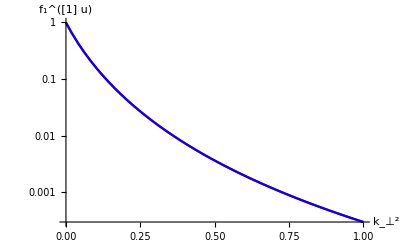

```mathematica
LogPlot[{xmf1u[y,delta]/xmf1u[0.,delta]/.delta->0,xmf1d[y,delta]/xmf1d[0.,delta]/.delta->0},{y,0.0,1},PlotStyle->{Red,Blue},PlotRange->All,AxesLabel->{"k_⊥^2","f_1^([1] u)"}]
```

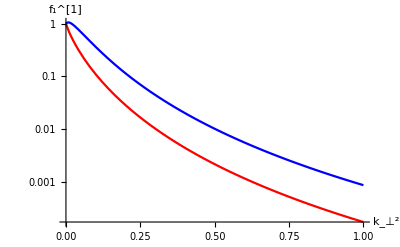

```mathematica
LogPlot[{xmf1u[y,delta]/xmf1u[0.,delta]/.delta->2.74,xmf1d[y,delta]/xmf1d[0.,delta]/.delta->2.74},{y,0.0,1},PlotStyle->{Red,Blue},PlotRange->All,AxesLabel->{"k_⊥^2","f_1^[1]"}]
```

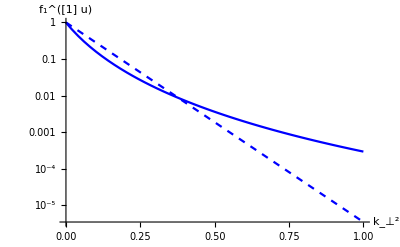

```mathematica
plot0=LogPlot[{xmf1u[y,0.]/xmf1u[0.,0.],xmf1ugauss[y,0]/xmf1ugauss[0.,0]},{y,0.0,1.},PlotStyle->{Blue,{Dashing[Small],Blue}},PlotRange->All,AxesLabel->{"k_⊥^2","f_1^([1] u)"}]
```

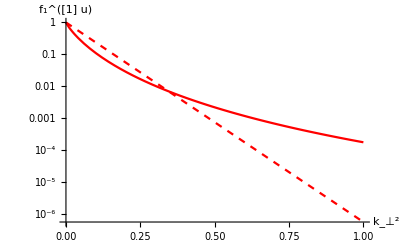

```mathematica
plot1=LogPlot[{xmf1u[y,2.74]/xmf1u[0.,2.74],xmf1ugauss[y,2.74]/xmf1ugauss[0.,2.74]},{y,0.0,1},PlotStyle->{Red,{Dashing[Small],Red}},PlotRange->All,AxesLabel->{"k_⊥^2","f_1^([1] u)"}]
```

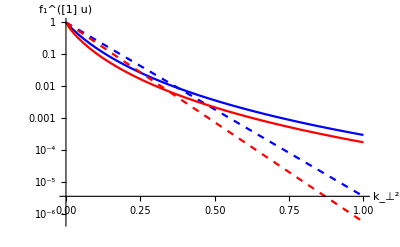

```mathematica
Show[plot0,plot1]
```

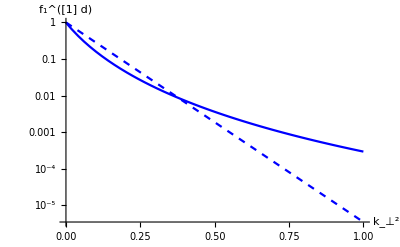

```mathematica
plot0d=LogPlot[{xmf1d[y,0.]/xmf1d[0.,0.],xmf1dgauss[y,0]/xmf1dgauss[0.,0]},{y,0.0,1.},PlotStyle->{Blue,{Dashing[Small],Blue}},PlotRange->All,AxesLabel->{"k_⊥^2","f_1^([1] d)"}]
```

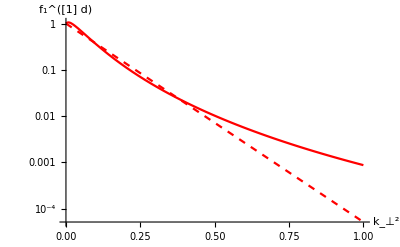

```mathematica
plot1d=LogPlot[{xmf1d[y,2.74]/xmf1d[0.,2.74],xmf1dgauss[y,2.74]/xmf1dgauss[0.,2.74]},{y,0.0,1},PlotStyle->{Red,{Dashing[Small],Red}},PlotRange->All,AxesLabel->{"k_⊥^2","f_1^([1] d)"}]
```

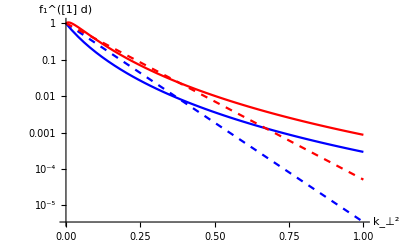

```mathematica
Show[plot0d,plot1d]
```

### TMD g_1

Calculation of <k_⊥^2>

```mathematica
kperpg1u[delta_]:=NIntegrate[(xmg1u[y^2,delta]*y^2*(2*Pi*y)),{y,0.,Sqrt[2.]},WorkingPrecision->6]/NIntegrate[(xmg1u[y^2,delta]*(2*Pi*y)),{y,0.,Sqrt[2.]},WorkingPrecision->6]
kperpg1d[delta_]:=NIntegrate[(xmg1d[y^2,delta]*y^2*(2*Pi*y)),{y,0.,Sqrt[2.]},WorkingPrecision->6]/NIntegrate[(xmg1d[y^2,delta]*(2*Pi*y)),{y,0.,Sqrt[2.]},WorkingPrecision->6]
```

SetDelayed::write: Tag InterpolatingFunction in «1» is Protected.

$Failed

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.,3.14159}},{5,7,0,{101},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,1,2,3,4,5,6,«38»,45,46,47,48,49,«52»},{0.0588919,0.0575267,0.0561496,0.0547501,«43»,0.0717455,0.070157,0.0686287,«51»}},{Automatic}]«1»«6»] is Protected.

$Failed

Reading the results for  <k_⊥^2> of g1 as function of delta:

```mathematica
kperpg1u:=Interpolation[{{0.,0.058891932314457905},{0.031415926535897934,0.060604272794717265},{0.06283185307179587,0.06233328062469728},{0.0942477796076938,0.06407729956736337},{0.12566370614359174,0.06583453386864004},{0.15707963267948966,0.06760299514780974},{0.1884955592153876,0.06938053480686059},{0.21991148575128555,0.07116462769688649},{0.25132741228718347,0.07295255139803683},{0.2827433388230814,0.07474119962466806},{0.3141592653589793,0.0765270911605215},{0.3455751918948773,0.0783062870465872},{0.3769911184307752,0.08007440674656995},{0.4084070449666731,0.08182647078449044},{0.4398229715025711,0.0835569423899335},{0.471238898038469,0.08525960196850693},{0.5026548245743669,0.08692753960144135},{0.5340707511102649,0.08855311919576439},{0.5654866776461628,0.0901277270188965},{0.5969026041820608,0.09164213927873192},{0.6283185307179586,0.09308606168666665},{0.6597344572538566,0.09444836648717703},{0.6911503837897546,0.09571697723056201},{0.7225663103256524,0.09687893031906936},{0.7539822368615504,0.09792046803948863},{0.7853981633974484,0.09882710567972322},{0.8168140899333463,0.09958367390399805},{0.8482300164692442,0.10017467714877115},{0.8796459430051422,0.10058434703661517},{0.9110618695410401,0.1007970658727549},{0.942477796076938,0.10079764318448284},{0.9738937226128359,0.100571831296057},{1.0053096491487339,0.1001066428666186},{1.0367255756846319,0.0993909896606528},{1.0681415022205298,0.09841615337494417},{1.0995574287564276,0.09717637033978146},{1.1309733552923256,0.09566931606359375},{1.1623892818282235,0.09389648623428216},{1.1938052083641215,0.09186371841712636},{1.2252211349000195,0.08958135848921564},{1.2566370614359172,0.08706429238800044},{1.2880529879718152,0.08433200806107033},{1.3194689145077132,0.08140814112425047},{1.3508848410436112,0.07832030863989126},{1.3823007675795091,0.075099063349981},{1.4137166941154071,0.07177743822323872},{1.4451326206513049,0.06838998227166286},{1.4765485471872029,0.0649718393730081},{1.5079644737231008,0.06155789311388145},{1.5393804002589988,0.05818150463633848},{1.5707963267948968,0.05487439809269346},{1.6022122533307945,0.05166538599114611},{1.6336281798666925,0.04858015506870383},{1.6650441064025905,0.04564088301659391},{1.6964600329384885,0.042866019706688074},{1.7278759594743864,0.04027026695330799},{1.7592918860102844,0.03786465642359233},{1.7907078125461822,0.03565677879779586},{1.8221237390820801,0.03365104029282456},{1.8535396656179781,0.03184900775482138},{1.884955592153876,0.03024975625819845},{1.916371518689774,0.02885027656178558},{1.9477874452256718,0.027645806500725394},{1.9792033717615698,0.026630239470677525},{2.0106192982974678,0.025796358833585702},{2.0420352248333655,0.02513626256048067},{2.0734511513692637,0.024641487907510726},{2.1048670779051615,0.024303219452267284},{2.1362830044410597,0.02411267792276061},{2.1676989309769574,0.024061029521488368},{2.199114857512855,0.024139615677005663},{2.2305307840487534,0.02434007487555307},{2.261946710584651,0.024654301992949542},{2.2933626371205493,0.02507461676741497},{2.324778563656447,0.025593740336415743},{2.356194490192345,0.026204819513967602},{2.387610416728243,0.026901439190931162},{2.419026343264141,0.027677595296200785},{2.450442269800039,0.028527790662100573},{2.4818581963359367,0.029446849611320332},{2.5132741228718345,0.030430054610013933},{2.5446900494077327,0.03147307902978517},{2.5761059759436304,0.03257187944376911},{2.6075219024795286,0.03372283172916},{2.6389378290154264,0.03492259289638863},{2.6703537555513246,0.036168126557184696},{2.7017696820872223,0.0374566252790684},{2.73318560862312,0.038785537776143436},{2.7646015351590183,0.04015260718210179},{2.796017461694916,0.041555659143356384},{2.8274333882308142,0.042992746188141265},{2.858849314766712,0.044462103779862046},{2.8902652413026098,0.045962059658226105},{2.921681167838508,0.04749107574844325},{2.9530970943744057,0.049047710845331716},{2.984513020910304,0.05063054300740654},{3.0159289474462017,0.05223827195991363},{3.0473448739820994,0.05386959230679031},{3.0787608005179976,0.0555231883551176},{3.1101767270538954,0.05719775918175913},{3.1415926535897936,0.05889193231445786}}]
```

```mathematica
kperpg1d:=Interpolation[{{0.,0.058891932314457905},{0.031415926535897934,0.057526696652534064},{0.06283185307179587,0.05614963406324218},{0.0942477796076938,0.054750115287667},{0.12566370614359174,0.053317033969496164},{0.15707963267948966,0.051838338646313084},{0.1884955592153876,0.050300753055696514},{0.21991148575128555,0.048689162344332904},{0.25132741228718347,0.04698604894953739},{0.2827433388230814,0.04517068137058967},{0.3141592653589793,0.04321800233196606},{0.3455751918948773,0.04109721746531046},{0.3769911184307752,0.03876966449691422},{0.4084070449666731,0.0361859263178245},{0.4398229715025711,0.03328154016993651},{0.471238898038469,0.029970338901274183},{0.5026548245743669,0.026134394080377838},{0.5340707511102649,0.02160746448582108},{0.5654866776461628,0.016147043254354912},{0.5969026041820608,0.009384610349680174},{0.6283185307179586,0.0007310524382230225},{0.6597344572538566,-0.010818024100694087},{0.6911503837897546,-0.027127184072835424},{0.7225663103256524,-0.05209441689929992},{0.7539822368615504,-0.09546343079353702},{0.7853981633974484,-0.1903610667466008},{0.8168140899333463,-0.5686615639242685},{0.8482300164692442,1.320500220498247},{0.8796459430051422,0.37521693997230515},{0.9110618695410401,0.23982138860733201},{0.942477796076938,0.1854062503421494},{0.9738937226128359,0.155905825439583},{1.0053096491487339,0.13730344991001187},{1.0367255756846319,0.12443468077065198},{1.0681415022205298,0.11495171651321538},{1.0995574287564276,0.10763310907298942},{1.1309733552923256,0.10178079603069741},{1.1623892818282235,0.09696639725762997},{1.1938052083641215,0.09291243261484057},{1.2252211349000195,0.08943102741492683},{1.2566370614359172,0.08639030240840112},{1.2880529879718152,0.08369477423560358},{1.3194689145077132,0.08127346068812256},{1.3508848410436112,0.07907230851123803},{1.3823007675795091,0.07704934735168179},{1.4137166941154071,0.07517109671291469},{1.4451326206513049,0.07341059436530364},{1.4765485471872029,0.07174550376244702},{1.5079644737231008,0.07015696377480864},{1.5393804002589988,0.0686287281117619},{1.5707963267948968,0.06714646905754025},{1.6022122533307945,0.06569716597446533},{1.6336281798666925,0.06426871609691166},{1.6650441064025905,0.06284947421316221},{1.6964600329384885,0.06142790665320804},{1.7278759594743864,0.05999218181616043},{1.7592918860102844,0.0585297636436544},{1.7907078125461822,0.05702695941419085},{1.8221237390820801,0.055468339191614355},{1.8535396656179781,0.053836100238662456},{1.884955592153876,0.05210895182884372},{1.916371518689774,0.05026104708841782},{1.9477874452256718,0.04825996818221641},{1.9792033717615698,0.04606424353040448},{2.0106192982974678,0.04361944336261148},{2.0420352248333655,0.040852149938215496},{2.0734511513692637,0.037660450047863954},{2.1048670779051615,0.033897972620133464},{2.1362830044410597,0.02934634069225364},{2.1676989309769574,0.0236634626693121},{2.199114857512855,0.016281253906509974},{2.2305307840487534,0.006180638604900928},{2.261946710584651,-0.008668321534992128},{2.2933626371205493,-0.03297540506706107},{2.324778563656447,-0.08073634354432782},{2.356194490192345,-0.22038202517302688},{2.387610416728243,-10.169525285672167},{2.419026343264141,0.3595049086433644},{2.450442269800039,0.2074994103061759},{2.4818581963359367,0.15745369680900845},{2.5132741228718345,0.13234994309567724},{2.5446900494077327,0.11713555449931308},{2.5761059759436304,0.10683993939895628},{2.6075219024795286,0.09934389783869621},{2.6389378290154264,0.09359109360648674},{2.6703537555513246,0.08899566880571026},{2.7017696820872223,0.08520632432153884},{2.73318560862312,0.08199936201982477},{2.7646015351590183,0.07922537015198805},{2.796017461694916,0.07678055879632593},{2.8274333882308142,0.07459033951960663},{2.858849314766712,0.07259956334643701},{2.8902652413026098,0.07076636610892306},{2.921681167838508,0.06905820724581478},{2.9530970943744057,0.06744916847725196},{2.984513020910304,0.06591811976072068},{3.0159289474462017,0.06444743902030027},{3.0473448739820994,0.06302203394546693},{3.0787608005179976,0.06162880404087483},{3.1101767270538954,0.06025576583139463},{3.1415926535897936,0.05889193231445787}}]
```

Gaussian Ansatz:

```mathematica
g1ugauss[x_,y_,delta_]:=1./(Pi*kperpg1u[delta])*g1u[x,delta]*Exp[-y/kperpg1u[delta]]
normu[delta_]:=NIntegrate[g1u[x,delta],{x,0,1}]
xmg1ugauss[y_,delta_]:=normu[delta]/(Pi*kperpg1u[delta])*Exp[-y/kperpg1u[delta]]
```

```mathematica
g1dgauss[x_,y_,delta_]:=1./(Pi*kperpg1d[delta])*g1d[x,delta]*Exp[-y/kperpg1d[delta]]
normd[delta_]:=NIntegrate[g1d[x,delta],{x,0,1}]
xmg1dgauss[y_,delta_]:=normd[delta]/(Pi*kperpg1d[delta])*Exp[-y/kperpg1d[delta]]
```

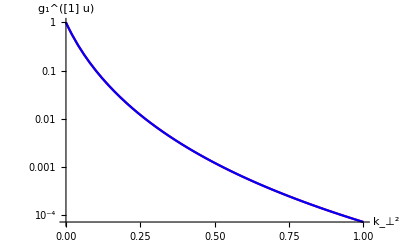

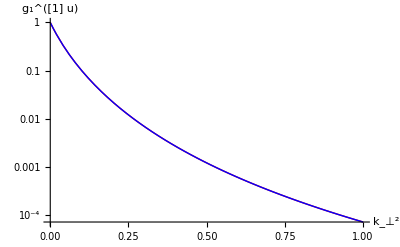

```mathematica
LogPlot[{xmg1u[y,delta]/xmg1u[0.,delta]/.delta->0,xmg1d[y,delta]/xmg1d[0.,delta]/.delta->0},{y,0.0,1},PlotStyle->{Red,Blue},PlotRange->All,AxesLabel->{"k_⊥^2","g_1^([1] u)"}]
```

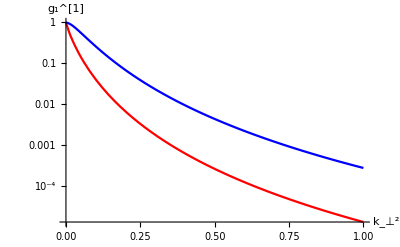

```mathematica
LogPlot[{xmg1u[y,delta]/xmg1u[0.,delta]/.delta->2.74,xmg1d[y,delta]/xmg1d[0.,delta]/.delta->2.74},{y,0.0,1},PlotStyle->{Red,Blue},PlotRange->All,AxesLabel->{"k_⊥^2","g_1^[1]"}]
```

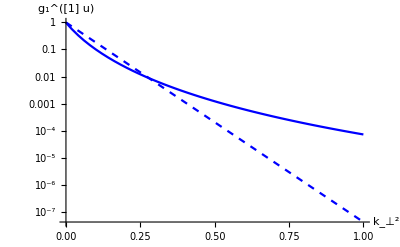

```mathematica
plot0=LogPlot[{xmg1u[y,0.]/xmg1u[0.,0.],xmg1ugauss[y,0]/xmg1ugauss[0.,0]},{y,0.0,1.},PlotStyle->{Blue,{Dashing[Small],Blue}},PlotRange->All,AxesLabel->{"k_⊥^2","g_1^([1] u)"}]
```

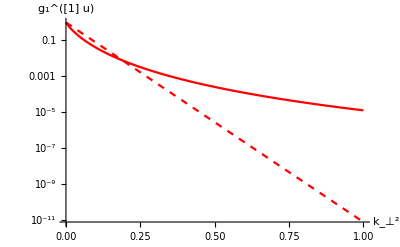

```mathematica
plot1=LogPlot[{xmg1u[y,2.74]/xmg1u[0.,2.74],xmg1ugauss[y,2.74]/xmg1ugauss[0.,2.74]},{y,0.0,1},PlotStyle->{Red,{Dashing[Small],Red}},PlotRange->All,AxesLabel->{"k_⊥^2","g_1^([1] u)"}]
```

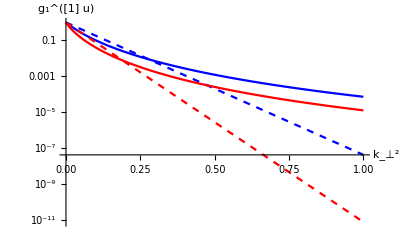

```mathematica
Show[plot0,plot1]
```

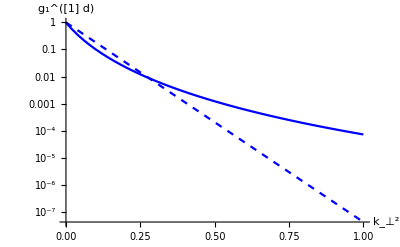

```mathematica
plot0d=LogPlot[{xmg1d[y,0.]/xmg1d[0.,0.],xmg1dgauss[y,0]/xmg1dgauss[0.,0]},{y,0.0,1.},PlotStyle->{Blue,{Dashing[Small],Blue}},PlotRange->All,AxesLabel->{"k_⊥^2","g_1^([1] d)"}]
```

```mathematica
plot1d=LogPlot[{xmg1d[y,2.74]/xmg1d[0.,2.74],xmg1dgauss[y,2.74]/xmg1dgauss[0.,2.74]},{y,0.0,1},PlotStyle->{Red,{Dashing[Small],Red}},PlotRange->All,AxesLabel->{"k_⊥^2","g_1^([1] d)"}]
```

$Aborted

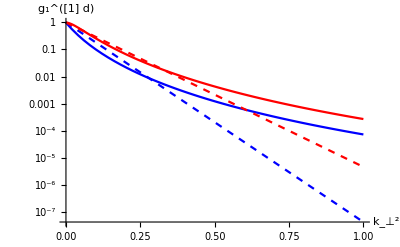

```mathematica
Show[plot0d,plot1d]
```

### TMD h_1

### TMD h_(1L) - -g_(1T)

### TMD h_(1T)^⊥